# Pruebas de caminatas cuánticas con una moneda de 4 dimensiones.

## DiscreteProbabilityPlot: estados, probabilidades y escalas de color

Evalúa las celdas en orden. Se carga QWMisc.wl desde la carpeta de este notebook y JA_libs desde el proyecto. VisualizeWalkerState permanece como interfaz de compatibilidad. Las probabilidades se representan sin renormalizarlas. La paleta predeterminada va de blanco (mínimo) a negro (máximo); ColorFunction permite elegir otra paleta.

## Llamar paquetes y ciertas funciones

```mathematica
root=NotebookDirectory[];Get[FileNameJoin[{root,"scripts","load_project.wl"}]];
```

```mathematica
Get[FileNameJoin[{root,"plot_entropia_monedas.wl"}]]
```

## Ejemplos de funciones, testeos y cosas similares.

## IPR espacial y densidad local I_n(x,y)

Se suma sobre la moneda antes de elevar al cuadrado. La densidad local I_n es una magnitud en posición, distinta de la distribución de Husimi en espacio de fases.

ComputeSpatialIPR[psi, d] devuelve un escalar; 
ComputeSpatialIPRDensity[psi, d] devuelve un valor por sitio, en el orden de grid["Coords"]. Ambas normalizan internamente y usan d = 4 por defecto. Los bloques consecutivos de d amplitudes corresponden a un sitio. La densidad se pasa a DiscreteProbabilityPlot como Probabilities, con escala Linear: Squared volvería a elevar I_n al cuadrado.

### 1. Estados localizado, uniforme y gaussiano

```mathematica
iprGrid=GenerateRectangleBasis[8,5];iprCoin=Normalize[{1,ⅈ,-1,0}];iprN=iprGrid["Dimension"];iprLocalized=LocalizedState[iprGrid,{2,3},iprCoin];iprUniform=Flatten[KroneckerProduct[ConstantArray[1/(√iprN),iprN],iprCoin]];iprGaussian=GaussianState[iprGrid,{2,3},iprCoin,1.2];iprStates={iprLocalized,iprUniform,iprGaussian};iprNames={"Localizado","Uniforme","Gaussiano"};iprProbabilities=(Total[Partition[Abs[Normal[#1]/Norm[#1]]^2,4],{2}]&)/@iprStates;iprDensities=ComputeSpatialIPRDensity/@iprStates;iprTotals=ComputeSpatialIPR/@iprStates;Grid[Prepend[MapThread[{#1,#2,Total[#3]}&,{iprNames,iprTotals,iprDensities}],{"Estado","IPR espacial","Suma de I_n"}],Frame->All]
```

El localizado tiene IPR = 1; el uniforme tiene IPR = 1/N y densidad 1/N^2 por sitio. El rectángulo incluye x = 0,...,8 e y = 0,...,5: N = 54. Cada mapa usa su propio rango de color para mostrar su estructura.

```mathematica
GraphicsGrid[Table[{DiscreteProbabilityPlot[iprGrid,iprProbabilities⟦j⟧,PlotLabel->iprNames⟦j⟧" : P_n(x,y)",ImageSize->420],DiscreteProbabilityPlot[iprGrid,iprDensities⟦j⟧,InputType->"Probabilities",ProbabilityScale->"Linear",PlotLabel->iprNames⟦j⟧" : I_n(x,y) = P_n(x,y)^2; IPR = "N[iprTotals⟦j⟧],PlotLegends->Placed[BarLegend[{GrayLevel[1-#1]&,{0,Max[iprDensities⟦j⟧]}},LegendLabel->"I_n = P_n^2"],Right],ImageSize->420]},{j,Length[iprStates]}],ImageSize->1100]
```

### 2. Ejemplo con un eigenvector del operador de evolución

```mathematica
iprEigenGrid=GenerateRectangleBasis[4,3];iprEigenCoin=N[FourierMatrix[4]];iprEvolution=QWEvolutionOperator[iprEigenGrid,iprEigenCoin];{iprEigenvalues,iprEigenvectors}=Eigensystem[N[Normal[iprEvolution]]];iprEigenOrder=Ordering[-Arg[iprEigenvalues]];iprEigenIndex=iprEigenOrder⟦Ceiling[Length[iprEigenOrder]/2]⟧;iprEigenstate=Normalize[iprEigenvectors⟦iprEigenIndex⟧];iprEigenP=Total[Partition[Abs[iprEigenstate]^2,4],{2}];iprEigenDensity=ComputeSpatialIPRDensity[iprEigenstate];iprEigenTotal=ComputeSpatialIPR[iprEigenstate];{"Eigenfase epsilon = -Arg(lambda)"->-Arg[iprEigenvalues⟦iprEigenIndex⟧],"IPR espacial"->iprEigenTotal,"Suma de I_n"->Total[iprEigenDensity],"Residuo del eigenvector"->Norm[iprEvolution.iprEigenstate-iprEigenvalues⟦iprEigenIndex⟧ iprEigenstate]}
```

```mathematica
GraphicsRow[{DiscreteProbabilityPlot[iprEigenGrid,iprEigenP,PlotLabel->"P_n(x,y) del eigenvector",ImageSize->420],DiscreteProbabilityPlot[iprEigenGrid,iprEigenDensity,ProbabilityScale->"Linear",PlotLabel->"Densidad local I_n(x,y)",PlotLegends->Placed[BarLegend[{GrayLevel[1-#1]&,{0,Max[iprEigenDensity]}},LegendLabel->"I_n = P_n^2"],Right],ImageSize->420]},ImageSize->1100]
```

### 3. Comprobaciones automáticas

```mathematica
TestReport[FileNameJoin[{root,"tests","NotebookTests.wlt"}]]
```

## Evolución de la IPR espacial

SpatialIPREvolutionPlot[operador, estadoInicial, pasos] grafica la IPR desde t = 0 hasta el paso indicado. CoinDimension -> 4 es el valor predeterminado. Se conserva solo el estado actual durante la evolución. La escala vertical es logarítmica y la línea discontinua indica 1/N, el mínimo de la IPR para N nodos; no es una predicción del valor final.

```mathematica
iprPlotGrid=GenerateRectangleBasis[12,8];iprPlotCoin=N[FourierMatrix[4]];iprPlotEvolution=QWEvolutionOperator[iprPlotGrid,SparseArray[iprPlotCoin]];iprPlotInitial=LocalizedState[iprPlotGrid,{6,4},Normalize[{1,ⅈ,-1,0}]];SpatialIPREvolutionPlot[iprPlotEvolution,iprPlotInitial,240]
```

Para el operador evolutionSep y el estado initialState de tu rutina, basta llamar SpatialIPREvolutionPlot[evolutionSep, initialState, steps]. No necesitas finalstates ni iprDat. Las opciones de ListLinePlot permiten cambiar etiquetas, tamaño, estilos y rango.

```mathematica
SpatialIPREvolutionPlot[iprPlotEvolution,iprPlotInitial,120,ScalingFunctions->None,ShowUniformReference->False,PlotLabel->"IPR espacial: escala lineal",ImageSize->650]
```

ComputeSpatialIPREvolution devuelve los pares {t, IPR(t)} si necesitas guardar o analizar los datos. Para cambiar la dimensión de moneda, usa CoinDimension -> 2 (o la dimensión correspondiente) en cualquiera de las dos funciones.

```mathematica
iprEvolutionData=ComputeSpatialIPREvolution[iprPlotEvolution,iprPlotInitial,120];{"Número de muestras"->Length[iprEvolutionData],"Primera muestra"->First[iprEvolutionData],"Última muestra"->Last[iprEvolutionData]}
```

### Comprobaciones de evolución

```mathematica
TestReport[FileNameJoin[{root,"tests","NotebookTests.wlt"}]]
```

## 1. Estado o probabilidades: misma imagen

```mathematica
grid=GenerateRectangleBasis[8,5];
coin=Normalize[{1,ⅈ,-1,0}];
psi=GaussianState[grid,{2,3},coin,1.2];
probabilities=Total[Partition[Abs[Normal[psi]]^2,4],{2}];
statePlot=DiscreteProbabilityPlot[grid,psi,InputType->"State",PlotLegends->None];
probabilityPlot=DiscreteProbabilityPlot[grid,probabilities,PlotLegends->None];
{statePlot===probabilityPlot,Total[probabilities]}
```

```mathematica
GraphicsRow[{DiscreteProbabilityPlot[grid,psi,InputType->"State",PlotLabel->"Desde amplitudes",ImageSize->360],DiscreteProbabilityPlot[grid,probabilities,PlotLabel->"Desde probabilidades",ColorFunction->"DarkRainbow",ImageSize->360]},ImageSize->900]
```

## 2. Escalas de color

```mathematica
grid=GenerateRectangleBasis[8,5];
coin=Normalize[{1,ⅈ,-1,0}];
psi=GaussianState[grid,{2,3},coin,1.2];
```

```mathematica
colores={"StarryNightColors","DarkRainbow","DeepSeaColors","AvocadoColors","FuchsiaTones"};
{DiscreteProbabilityPlot[grid,psi,InputType->"State",PlotLabel->"Default",ImageSize->360],Flatten[DiscreteProbabilityPlot[grid,psi,InputType->"State",PlotLabel->#,ColorFunction->#,ImageSize->360]&/@colores]}
```

## 3. Escala de probabilidad

Cada leyenda indica la cantidad transformada. ProbabilityRange siempre recibe probabilidades originales. Squared se conserva por compatibilidad; Sqrt y CubeRoot resaltan regiones de baja probabilidad.

```mathematica
grid=GenerateRectangleBasis[8,5];
coin=Normalize[{1,ⅈ,-1,0}];
psi=GaussianState[grid,{2,3},coin,1.2];

scales={"Linear","Sqrt","CubeRoot","Squared","Log"};
{DiscreteProbabilityPlot[grid,psi,InputType->"State",PlotLabel->"Default",ImageSize->360],Flatten[DiscreteProbabilityPlot[grid,psi,InputType->"State",PlotLabel->#,ProbabilityScale->#,ImageSize->360]&/@scales]}
```

## 4. Evolución con escala automática por estado

Cada cuadro ajusta la escala de color a su propia probabilidad máxima. Esto permite distinguir las variaciones espaciales aunque las probabilidades sean pequeñas. Un mismo color puede corresponder a probabilidades distintas entre cuadros; consulta la leyenda de cada uno.

```mathematica
SeedRandom[23];
Lx=20; Ly=20;
grid=GenerateRectangleBasis[Lx,Ly];
pos={6,6};
coin=N[HaarRandomState[4]//Normalize];
S=BuildShiftOperators[grid,CoinDimension->4];
steps=10;
stride=1;
coinSep=N[KroneckerProduct[RandomVariate[CircularOrthogonalMatrixDistribution[2]],RandomVariate[CircularOrthogonalMatrixDistribution[2]]]];
evolutionSep=QWEvolutionOperator[grid,SparseArray[coinSep//N]];
initialState=LocalizedState[grid,pos,coin];
QWAnimation[grid,evolutionSep,initialState,steps,"FrameStride"->stride,PlotLabel->"Separable",ImageSize->500,LabelStyle->Directive[Bold,17],AnimationRunning->True]
```

### VIendo moneda separable vs no separable

```mathematica
SeedRandom[13];
Lx=70; Ly=70;
grid=GenerateRectangleBasis[Lx,Ly];
pos={35,35};
coin=N[HaarRandomState[4]//Normalize];
S=BuildShiftOperators[grid,CoinDimension->4];

coinSep=N[KroneckerProduct[RandomVariate[CircularOrthogonalMatrixDistribution[2]],RandomVariate[CircularOrthogonalMatrixDistribution[2]]]];
evolutionSep=QWEvolutionOperator[grid,SparseArray[coinSep//N]];

coinNoSep=N[RandomVariate[CircularOrthogonalMatrixDistribution[4]]];
evolutionNoSep=QWEvolutionOperator[grid,SparseArray[coinNoSep//N]];

initialState=LocalizedState[grid,pos,coin];

steps=500;
stride=1;

Grid[{{QWAnimation[grid,evolutionSep,initialState,steps,"FrameStride"->stride,PlotLabel->"OO",ImageSize->500,LabelStyle->Directive[Bold,17],AnimationRunning->True],QWAnimation[grid,evolutionNoSep,initialState,steps,"FrameStride"->stride,PlotLabel->"O",ImageSize->500,LabelStyle->Directive[Bold,17],AnimationRunning->True]}},Alignment->{Center,Top},Spacings->{2,0}]
```

## 5. Distribución temporal promedio

```mathematica
SeedRandom[13];
Lx=70; Ly=70;
grid=GenerateRectangleBasis[Lx,Ly];
pos={35,35};
coin=N[HaarRandomState[4]//Normalize];
S=BuildShiftOperators[grid,CoinDimension->4];

coinSep=N[KroneckerProduct[RandomVariate[CircularOrthogonalMatrixDistribution[2]],RandomVariate[CircularOrthogonalMatrixDistribution[2]]]];
evolutionOp=QWEvolutionOperator[grid,SparseArray[coinSep//N]];

Tmax=9000;
initialState=LocalizedState[grid,pos,coin];
distribution=LimitDistribution[grid,evolutionOp,initialState,Tmax];
DiscreteProbabilityPlot[grid,distribution]
```

### Comparando diferentes monedas

```mathematica
RandomMatrixNames[]
```

```mathematica
Lx=70; Ly=70;
grid=GenerateRectangleBasis[Lx,Ly];
pos={35,35};
coin=N[HaarRandomState[4]//Normalize];
S=BuildShiftOperators[grid,CoinDimension->4];
initialState=LocalizedState[grid,pos,coin];
Tmax=9000;
Module[{c=RandomMatrix[#],evolutionOp,distribution},
evolutionOp=QWEvolutionOperator[grid,SparseArray[c//N]];
distribution=LimitDistribution[grid,evolutionOp,initialState,Tmax];
DiscreteProbabilityPlot[grid,distribution,PlotLabel->#,LabelStyle->Directive[Bold, 17],ImageSize->450]
]&/@RandomMatrixNames[]
```

## 6. Autovalores de tres rectangulos de distinto tamaño

### Preparar QuantumWalks en cada kernel

La ruta corresponde a la copia de QuantumWalks que ya existe en tu cuenta del cluster. PacletDirectoryLoad solo la hace visible durante la sesion temporal. Se carga ForScience y luego QuantumWalks en cada kernel del nodo. El bloque de FormatUsage evita un problema de formato de ayudas cuando no hay interfaz grafica en el nodo.

```mathematica
prepararQuantumWalks = Function[
  Module[{ruta = FileNameJoin[{Replace[Environment["QW_PROJECT_ROOT"],Except[_String]:>FileNameJoin[{$HomeDirectory,"QW"}]],"JA_libs","QuantumWalks"}]},
    If[DirectoryQ[ruta],
      PacletDirectoryLoad[ruta];
      Needs["ForScience`"];
      Block[{ForScience`PacletUtils`FormatUsage = Identity}, Needs["QuantumWalks`"]];
      MemberQ[$Packages, "ForScience`"] &&
        Length[DownValues[QuantumWalks`Billiards`GenerateRectangleBasis]] > 0,
      False
    ]
  ]
];
```

### Definir una diagonalizacion por cada rectangulo

Cada entrada {ancho, alto} cuenta posiciones, no indices maximos. GenerateRectangleBasis[ancho-1, alto-1] produce ancho x alto posiciones. Con cuatro estados de moneda, el operador U = S . (I KroneckerProduct C) tiene dimension 4 ancho alto. Se calculan todos los autovalores de la matriz densa; esta eleccion solo es razonable mientras quepa en la memoria del nodo.

```mathematica
calcularEspectro = Function[par,
  Module[{base, dim, s, moneda, u, vals},
    base = QuantumWalks`Billiards`GenerateRectangleBasis[par[[1]] - 1, par[[2]] - 1];
    dim = base["Dimension"];
    s = QuantumWalks`Billiards`BuildShiftOperators[base,
      QuantumWalks`Billiards`CoinDimension -> 4];
    moneda = QuantumWalks`Billiards`GeneralizedGroverCoin[Pi/4.];
    u = s . KroneckerProduct[IdentityMatrix[dim, SparseArray], SparseArray[moneda]];
    vals = Eigenvalues[Normal[u]];
    <|"Nodo" -> $MachineName, "Proceso" -> $ProcessID,
      "Tamano" -> par, "DimensionU" -> Dimensions[u],
      "Autovalores" -> vals, "ErrorModulo" -> Max[Abs[Abs[vals] - 1]]|>
  ]
];
```

### Ejecutar cuatro trabajos en dos kernels

```mathematica
resultados = EjecutarEnNodo["nodo1", 2, calcularEspectro,
  {{3, 2}, {4, 2}, {5, 2}, {6, 2}}, prepararQuantumWalks];
```

Cada entrada se calcula completa en un kernel. Los resultados regresan en el mismo orden de la lista de entradas. Los identificadores de proceso permiten comprobar que participaron dos kernels. ErrorModulo mide cuanto se aleja el modulo de cada autovalor de 1.

```mathematica
If[ListQ[resultados],
  resultados[[All, {"Tamano", "Nodo", "Proceso", "DimensionU", "ErrorModulo"}]],
  resultados
]
```

```mathematica
If[ListQ[resultados],
  {DeleteDuplicates[resultados[[All, "Proceso"]]],
   Length /@ resultados[[All, "Autovalores"]]},
  resultados
]
```

# Aplicaciones:

```mathematica
?ComputeTotalIPR
```

## IPR espacial

## Rectangulo

### Visualizando un caso particular. Graficando la densidad de ipr y checando un valor particular de la densidad según un nodo dado.

```mathematica
Lx=20;Ly=20;
grid=GenerateRectangleBasis[Lx,Ly];
pos={10,10};
coin=HaarRandomState[4];
initState=Normalize[LocalizedState[grid,pos,coin]+LocalizedState[grid,pos+{1,1},coin]];

iprdensity=ComputeSpatialIPRDensity[initState,4];

indexList=grid["Mapping"];
index=indexList[{10,10}];
iprlocal=iprdensity[[index]]
DiscreteProbabilityPlot[grid,iprdensity]
```

### Comparando IPRs

#### Para estados localizados

Para dimensiones comparables con el sinai

```mathematica
L1=140;R1=100;
GridDataSinai=GenerateSinaiBasis[L1,R1];
dim=GridDataSinai["Dimension"];
aurea=GoldenRatio//N;
Ly=Floor[Sqrt[dim/aurea]];
Lx=Floor[Ly*aurea];
Print["Las dimensiones del rectangulo serían:","Lx= ",Lx,", Ly= ",Ly]
```

```mathematica
SeedRandom[23];

(*Malla y estado inicial*)
Lx=97;
Ly=60;
grid=GenerateRectangleBasis[Lx,Ly];
pos={35,35};

coin=N[Normalize[HaarRandomState[4]]];
S=BuildShiftOperators[grid,CoinDimension->4];
initialState=LocalizedState[grid,pos,coin];

Tmax=2000;
nSites=grid["Dimension"];
names=RandomMatrixNames[];

(*Evolución de la IPR para cada tipo de moneda*)
iprDat=Module[{c=N[RandomMatrix[#]],evolutionOp},evolutionOp=QWEvolutionOperator[grid,SparseArray[c]];
ComputeSpatialIPREvolution[evolutionOp,initialState,Tmax,CoinDimension->4]]&/@names;
```

```mathematica
(*Clasificación:integrables hasta "gpg" inclusive*)cut=First[FirstPosition[names,"gpg"]];
nRegular=cut;
nChaotic=Length[names]-cut;

(*Colores individuales*)
regularColors={RGBColor["#0096B6"],(*p:turquesa*)RGBColor["#2878B5"],(*oo:azul*)RGBColor["#4650A4"],(*b:índigo*)RGBColor["#183153"]   (*gpg:azul marino*)};

chaoticColors={RGBColor["#D99A00"],(*o:ocre*)RGBColor["#E66B19"],(*uoou:naranja*)RGBColor["#C83F32"],(*ubu:rojo*)RGBColor["#84232E"],(*u:granate*)RGBColor["#A56832"]   (*upu:cobre*)};
(*Estilos de curvas y referencias*)
styles=Join[Directive[#,AbsoluteThickness[2.2]]&/@regularColors,Directive[#,AbsoluteThickness[2.2]]&/@chaoticColors,{Directive[GrayLevel[0.55],AbsoluteThickness[1.8],Dotted],Directive[RGBColor["#884DA7"],AbsoluteThickness[3],DotDashed],Directive[RGBColor["#368A56"],AbsoluteThickness[3],Dashed]}];

(*Referencias horizontales:1/N,2/N y 3/N*)
referenceValues={1/nSites,2/nSites,3/nSites};

references=Table[{{0,value},{Tmax,value}},{value,referenceValues}];

(*Inset:último 25 % del tiempo.Se supone que cada curva de iprDat contiene puntos {t,IPR}.*)
tInset=0.75 Tmax;

lateData=Select[#,First[#]>=tInset&]&/@iprDat;

lateReferences=Table[{{tInset,value},{Tmax,value}},{value,referenceValues}];

latePlot=ListLinePlot[Join[lateData,lateReferences],PlotStyle->styles,ScalingFunctions->{None,"Log"},PlotRange->{All,{0.00015,0.001}},Frame->True,Axes->False,LabelStyle->Directive[Black,9],Background->White,ImagePadding->35];

(*Leyenda agrupada*)
legend=Framed[Column[{Grid[{{Column[{Style["Integrables",14,Bold,RGBColor["#183153"]],LineLegend[Take[styles,cut],Take[names,cut],LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->0.7],Column[{Style["Caóticas",14,Bold,RGBColor["#84232E"]],LineLegend[Take[styles,{cut+1,Length[names]}],Drop[names,cut],LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->0.7]}},Alignment->Top,Spacings->{2,0}],Style["Referencias",14,Bold,GrayLevel[0.25]],LineLegend[Take[styles,-3],{"Uniforme: 1/N","GUE: 2/N","GOE: 3/N"},LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->1],Background->White,FrameStyle->GrayLevel[0.85],FrameMargins->12,RoundingRadius->5];

(*Gráfico final*)
Img=Legended[ListLinePlot[Join[iprDat,references],PlotStyle->styles,ScalingFunctions->{None,"Log"},Frame->True,Axes->False,FrameLabel->{"Paso t","IPR espacial"},PlotLabel->"IPR\nComparación de monedas: integrabilidad y caos",GridLines->Automatic,PlotRange->All,ImageSize->900,LabelStyle->Directive[Bold,17],Epilog->{Inset[latePlot,Scaled[{0.80,0.60}],Center,Scaled[{0.45,0.45}]]}],Placed[legend,Right]]
```

```mathematica
Export[FileNameJoin[{root,"Imgs/IPR_CompCoins_Localized_Rect.pdf"}],Img]
```

#### Para estados deslocalizados

Para dimensiones comparables con el sinai

```mathematica
L1=120;R1=90;
GridDataSinai=GenerateSinaiBasis[L1,R1];
dim=GridDataSinai["Dimension"];
aurea=GoldenRatio//N;
Ly=Floor[Sqrt[dim/aurea]];
Lx=Floor[Ly*aurea];
Print["Las dimensiones del rectangulo serían:","Lx= ",Lx,", Ly= ",Ly]
```

```mathematica
SeedRandom[23];

(*Malla y estado inicial*)
Lx=97;
Ly=60;
grid=GenerateRectangleBasis[Lx,Ly];
dim=grid["Dimension"];
S=BuildShiftOperators[grid,CoinDimension->4];
initialState=RandomDelocalizedState[dim,4,RandomSeed->7];

Tmax=2000;
nSites=grid["Dimension"];
names=RandomMatrixNames[];

(*Evolución de la IPR para cada tipo de moneda*)
iprDat=Module[{c=N[RandomMatrix[#]],evolutionOp},evolutionOp=QWEvolutionOperator[grid,SparseArray[c]];
ComputeSpatialIPREvolution[evolutionOp,initialState,Tmax,CoinDimension->4]]&/@names;
```

```mathematica
(*Clasificación:integrables hasta "gpg" inclusive*)cut=First[FirstPosition[names,"gpg"]];
nRegular=cut;
nChaotic=Length[names]-cut;

(*Colores individuales*)
regularColors={RGBColor["#0096B6"],(*p:turquesa*)RGBColor["#2878B5"],(*oo:azul*)RGBColor["#4650A4"],(*b:índigo*)RGBColor["#183153"]   (*gpg:azul marino*)};

chaoticColors={RGBColor["#D99A00"],(*o:ocre*)RGBColor["#E66B19"],(*uoou:naranja*)RGBColor["#C83F32"],(*ubu:rojo*)RGBColor["#84232E"],(*u:granate*)RGBColor["#A56832"]   (*upu:cobre*)};
(*Estilos de curvas y referencias*)
styles=Join[Directive[#,AbsoluteThickness[2.2]]&/@regularColors,Directive[#,AbsoluteThickness[2.2]]&/@chaoticColors,{Directive[GrayLevel[0.55],AbsoluteThickness[1.8],Dotted],Directive[RGBColor["#884DA7"],AbsoluteThickness[3],DotDashed],Directive[RGBColor["#368A56"],AbsoluteThickness[3],Dashed]}];

(*Referencias horizontales:1/N,2/N y 3/N*)
referenceValues={1/nSites,2/nSites,3/nSites};

references=Table[{{0,value},{Tmax,value}},{value,referenceValues}];

(*Inset:último 25 % del tiempo.Se supone que cada curva de iprDat contiene puntos {t,IPR}.*)
tInset=0.75 Tmax;

lateData=Select[#,First[#]>=tInset&]&/@iprDat;

lateReferences=Table[{{tInset,value},{Tmax,value}},{value,referenceValues}];

latePlot=ListLinePlot[Join[lateData,lateReferences],PlotStyle->styles,ScalingFunctions->{None,"Log"},PlotRange->{All,{0.00015,0.0006}},Frame->True,Axes->False,LabelStyle->Directive[Black,9],Background->White,ImagePadding->35];

(*Leyenda agrupada*)
legend=Framed[Column[{Grid[{{Column[{Style["Integrables",14,Bold,RGBColor["#183153"]],LineLegend[Take[styles,cut],Take[names,cut],LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->0.7],Column[{Style["Caóticas",14,Bold,RGBColor["#84232E"]],LineLegend[Take[styles,{cut+1,Length[names]}],Drop[names,cut],LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->0.7]}},Alignment->Top,Spacings->{2,0}],Style["Referencias",14,Bold,GrayLevel[0.25]],LineLegend[Take[styles,-3],{"Uniforme: 1/N","GUE: 2/N","GOE: 3/N"},LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->1],Background->White,FrameStyle->GrayLevel[0.85],FrameMargins->12,RoundingRadius->5];

(*Gráfico final*)
Img=Legended[ListLinePlot[Join[iprDat,references],PlotStyle->styles,ScalingFunctions->{None,"Log"},Frame->True,Axes->False,FrameLabel->{"Paso t","IPR espacial"},PlotLabel->"IPR\nComparación de monedas: integrabilidad y caos",GridLines->Automatic,PlotRange->All,ImageSize->900,LabelStyle->Directive[Bold,17],Epilog->{Inset[latePlot,Scaled[{0.6,0.75}],Center,Scaled[{0.35,0.35}]]}],Placed[legend,Right]]
```

```mathematica
Export[FileNameJoin[{root,"Imgs/IPR_CompCoins_DeLocalized_Rect.pdf"}],Img]
```

### Densidad de IPR (Matrices Grandes)

#### Para eigenestados alrededor de un valor dado

Veamos la DoS y ver si cambio mucho con el tamaño

```mathematica
Lx=30;
Ly=30;
grid=GenerateRectangleBasis[Lx,Ly];

(*grid debe ser la malla del estadio*)
coinMatrix=N[RandomMatrix["upu"]];

S=BuildShiftOperators[grid,CoinDimension->4];

U=QWEvolutionOperator[grid,SparseArray[coinMatrix]];
eigenvals=U//Eigenvalues;
eigenphases=-Arg[eigenvals];

Histogram[eigenphases,Automatic,"PDF"]
```

```mathematica
Lx=80;
Ly=60;
grid=GenerateRectangleBasis[Lx,Ly];

coinMatrix=N[RandomMatrix["b"]];
S=BuildShiftOperators[grid,CoinDimension->4];

U=N[QWEvolutionOperator[grid,SparseArray[coinMatrix]]];

(*Parámetros ajustables*)
k=10;
columns=3;
epsilon0=0.4;

sigma=1.001 Exp[-I epsilon0];

(*Ajustar la base de Arnoldi al número solicitado*)
basisSize=Min[Length[U],Max[60,2 k+10]];

{eigenvalues,eigenvectors}=Eigensystem[U,-k,Method->{"Arnoldi","Shift"->sigma,"BasisSize"->basisSize,"MaxIterations"->5000,"Tolerance"->10^-10}];

eigenvectors=Normalize/@eigenvectors;
eigenphases=-Arg[eigenvalues];

(*Ordenar por eigenfase*)
order=Ordering[eigenphases];
eigenvalues=eigenvalues[[order]];
eigenvectors=eigenvectors[[order]];
eigenphases=eigenphases[[order]];

residuals=MapThread[Norm[U.#2-#1 #2]&,{eigenvalues,eigenvectors}];

nFound=Length[eigenvectors];

densities=ComputeSpatialIPRDensity[#,4]&/@eigenvectors;
iprValues=Total/@densities;

(*Resumen*)
summary=Grid[Prepend[Table[{j,NumberForm[eigenphases[[j]],{6,4}],ScientificForm[residuals[[j]],3],ScientificForm[iprValues[[j]],3]},{j,nFound}],{"Estado","ε","Residuo","IPR"}],Frame->All];

(*Un panel por eigenestado*)
plots=Table[DiscreteProbabilityPlot[grid,densities[[j]],ProbabilityScale->"Linear",PlotLabel->Column[{Row[{"Estado ",j,"; ε = ",NumberForm[eigenphases[[j]],{6,4}]}],Row[{"IPR = ",ScientificForm[iprValues[[j]],3]}]},Alignment->Center],ImageSize->350],{j,nFound}];

(*Completar únicamente los espacios vacíos de la última fila*)
rows=Ceiling[nFound/columns];

Column[{summary,GraphicsGrid[Partition[PadRight[plots,rows columns,Null],columns],Spacings->{0.4,0.6},ImageSize->400 columns]}]

GraphicsGrid[Partition[PadRight[plots,6,Null],3],Spacings->{0.4,0.6},ImageSize->1200]
```

#### Tomando eigenestados en puntos distintos del espectro de energías

```mathematica
(*Malla y operador de evolución*)Lx=80;
Ly=80;
grid=GenerateRectangleBasis[Lx,Ly];

coinMatrix=N[RandomMatrix["upu"]];
S=BuildShiftOperators[grid,CoinDimension->4];

U=N[QWEvolutionOperator[grid,SparseArray[coinMatrix]]];

(*Seis intervalos y sus centros*)
k=10;
edges=Subdivide[-Pi,Pi,k];
intervals=Partition[edges,2,1];
targets=Mean/@intervals;

(*Un eigenestado próximo al centro de cada intervalo*)
eigenData=Table[Module[{sigma,vals,vecs,psi,phase,residual},sigma=1.001 Exp[-I targets[[j]]];
{vals,vecs}=Check[Eigensystem[U,-1,Method->{"Arnoldi","Shift"->sigma,"BasisSize"->60,"MaxIterations"->5000,"Tolerance"->10^-10}],Print["No convergió la búsqueda del intervalo ",j];
Abort[]];
psi=Normalize[First[vecs]];
phase=-Arg[First[vals]];
residual=Norm[U.psi-First[vals] psi];
(*No asignar a un intervalo un estado que quedó fuera*)If[!TrueQ[intervals[[j,1]]<=phase<=intervals[[j,2]]],Print["El eigenestado encontrado para el intervalo ",j," quedó fuera: ε = ",phase,". Revisa la búsqueda o si hay espectro en ese intervalo."];
Abort[]];
If[residual>10^-8,Print["Residuo demasiado grande en el intervalo ",j,": ",residual];
Abort[]];
{First[vals],psi,phase,residual}],{j,k}];

eigenvalues=eigenData[[All,1]];
eigenvectors=eigenData[[All,2]];
eigenphases=eigenData[[All,3]];
residuals=eigenData[[All,4]];

densities=ComputeSpatialIPRDensity[#,4]&/@eigenvectors;
iprValues=Total/@densities;

(*Resumen:objetivo,eigenfase encontrada,residuo e IPR*)
summary=Grid[Prepend[Table[{j,NumberForm[N[targets[[j]]],{6,4}],NumberForm[eigenphases[[j]],{6,4}],ScientificForm[residuals[[j]],3],ScientificForm[iprValues[[j]],3]},{j,k}],{"Intervalo","ε objetivo","ε encontrada","Residuo","IPR"}],Frame->All];
```

```mathematica
(*Configuración de la visualización*)columns=3;
nPlots=Length[eigenvectors];

(*Mapas con títulos externos y leyendas normalizadas*)
plots=Table[Module[{density,dmax,header,graphic},density=densities[[j]];
dmax=Max[density];
header=Row[{"Intervalo ",j,": ",NumberForm[N[intervals[[j,1]]],{4,2}]," a ",NumberForm[N[intervals[[j,2]]],{4,2}]}];
graphic=DiscreteProbabilityPlot[grid,density,ProbabilityScale->"Linear",ProbabilityRange->{0,dmax},ColorFunction->(GrayLevel[1-#]&),PlotLabel->None,FrameLabel->{"x","y"},LabelStyle->Directive[Black,11],ImagePadding->{{45,15},{45,15}},ImageSize->320,PlotLegends->With[{upper=dmax},Placed[BarLegend[{Function[value,GrayLevel[1-Clip[value/upper,{0,1}]]],{0,upper}},LegendLabel->"Iₙ",LegendMarkerSize->{18,180},LabelStyle->Directive[Black,10]],Right]]];
Column[{Style[header,12,Bold],Style[Row[{"ε = ",NumberForm[eigenphases[[j]],{6,4}],"   IPR = ",ScientificForm[iprValues[[j]],3]}],11],Style[Row[{"Residuo = ",ScientificForm[residuals[[j]],2]}],10,GrayLevel[0.35]],graphic},Alignment->Center,Spacings->0.4]],{j,nPlots}];

(*Completar la última fila sin perder paneles*)
panel=Grid[Partition[PadRight[plots,columns Ceiling[nPlots/columns],""],columns],Alignment->{Center,Top},Spacings->{2,2}];

(*Una única imagen con todos los mapas*)
imagen=Rasterize[panel,"Image",ImageResolution->200];

imagen
```

### Densidad de IPR (Matrices Pequeñas)

```mathematica
(*Malla y operador*)
Lx=30;
Ly=30;
grid=GenerateRectangleBasis[Lx,Ly];

coinMatrix=N[RandomMatrix["o"]];
S=BuildShiftOperators[grid,CoinDimension->4];

U=N[QWEvolutionOperator[grid,SparseArray[coinMatrix]]];

(*Espectro completo:eigenvalores y vectores correspondientes*)
{eigenvalues,eigenvectors}=Eigensystem[Normal[U]];
eigenvectors=Normalize/@eigenvectors;
eigenphases=-Arg[eigenvalues];
```

```mathematica
(*Dividir las eigenfases en subintervalos*)nIntervals=15;
columns=3;

edges=N[Subdivide[-Pi,Pi,nIntervals]];
intervals=Partition[edges,2,1];
centers=Mean/@intervals;

(*Seleccionar un eigenestado cercano al centro de cada intervalo*)
selectedIndices=Table[Module[{candidates},candidates=Select[Range[Length[eigenphases]],Function[index,intervals[[j,1]]<=eigenphases[[index]]&&If[j==nIntervals,eigenphases[[index]]<=intervals[[j,2]],eigenphases[[index]]<intervals[[j,2]]]]];
If[candidates==={},Missing["EmptyInterval"],First[MinimalBy[candidates,Abs[eigenphases[[#]]-centers[[j]]]&]]]],{j,nIntervals}];

(*Construir cada panel*)
plots=Table[Module[{index,density,residual,header,graphic,dmax},index=selectedIndices[[j]];
header=Row[{"Intervalo ",j,": ",NumberForm[intervals[[j,1]],{4,2}]," a ",NumberForm[intervals[[j,2]],{4,2}]}];
If[MissingQ[index],Column[{Style[header,12,Bold],"Sin eigenestados"},Alignment->Center],density=ComputeSpatialIPRDensity[eigenvectors[[index]],4];
dmax=Max[density];
residual=Norm[U.eigenvectors[[index]]-eigenvalues[[index]] eigenvectors[[index]]];
graphic=DiscreteProbabilityPlot[grid,density,ProbabilityScale->"Linear",ProbabilityRange->{0,dmax},ColorFunction->(GrayLevel[1-#]&),PlotLabel->None,FrameLabel->{"x","y"},LabelStyle->Directive[Black,11],ImagePadding->{{45,15},{45,15}},ImageSize->320,(*Leyenda:normalizar la densidad para asignar el color*)PlotLegends->With[{upper=dmax},Placed[BarLegend[{Function[value,GrayLevel[1-Clip[value/upper,{0,1}]]],{0,upper}},LegendLabel->"Iₙ",LegendMarkerSize->{18,180},LabelStyle->Directive[Black,10]],Right]]];
Column[{Style[header,12,Bold],Style[Row[{"ε = ",NumberForm[eigenphases[[index]],{6,4}],"   IPR = ",ScientificForm[Total[density],3]}],11],Style[Row[{"Residuo = ",ScientificForm[residual,2]}],10,GrayLevel[0.35]],graphic},Alignment->Center,Spacings->0.4]]],{j,nIntervals}];

(*Organizar los paneles*)
panel=Grid[Partition[PadRight[plots,columns Ceiling[nIntervals/columns],""],columns],Alignment->{Center,Top},Spacings->{2,2}];

(*Convertir el conjunto en una única imagen*)
imagen=Rasterize[panel,"Image",ImageResolution->200];

imagen
```

-Graphics-

### Tratando de hallar estados de borde mediante a IPR

```mathematica
SeedRandom[23];
Lx=10;
Ly=10;
grid=GenerateRectangleBasis[Lx,Ly];
S=BuildShiftOperators[grid,CoinDimension->4];
nSites=grid["Dimension"];
c=N[RandomMatrix["oo"]];
evolutionOp=QWEvolutionOperator[grid,SparseArray[c]];

(*Eigenvalores y eigenvectores,en el mismo orden*)
{eigenvals,eigenvecs}=Eigensystem[Normal[evolutionOp]];
```

#### Chequeando IPR vs cuasiEnergía

{-3.13675,-3.08952,-3.08046,-3.06629,-3.05028,-3.02957,-2.99769,-2.96818,-2.93267,-2.89045,-2.84669,-2.80112,-2.75737,-2.71515,-2.67964,-2.65013,-2.61824,-2.59754,-2.58152,-2.56736,-2.5583,-2.51107,-2.47147,-2.42067,-2.41758,-2.31879,-2.31578,-2.31169,-2.28008,-2.25809,-2.13897,-2.13822,-2.13461,-2.11382,-2.07465,-2.04056,-2.00778,-2.00742,-1.96448,-1.9225,-1.90991,-1.86519,-1.8353,-1.82347,-1.72877,-1.68724,-1.66213,-1.65936,-1.63086,-1.57353,-1.55338,-1.51597,-1.48902,-1.48224,-1.4774,-1.45966,-1.42165,-1.39582,-1.39452,-1.36328,-1.33078,-1.32351,-1.31436,-1.2833,-1.28255,-1.22748,-1.21661,-1.17952,-1.17787,-1.15492,-1.13207,-1.11399,-1.10833,-1.08838,-1.04485,-1.02992,-1.02165,-1.02114,-1.00082,-0.96225,-0.934822,-0.880583,-0.849097,-0.846568,-0.829511,-0.765982,-0.690594,-0.670199,-0.657416,-0.649602,-0.606105,-0.57623,-0.568576,-0.533716,-0.499645,-0.496893,-0.474641,-0.433887,-0.395173,-0.375126,-0.369737,-0.249242,-0.246797,-0.196914,-0.196546,-0.190828,-0.188208,-0.0896787,-0.0894302,-0.0594076,-0.0517809,-0.0379601,0.012195,0.0228789,0.0366673,0.0446507,0.0581414,0.0827117,0.113205,0.153552,0.193576,0.24182,0.291716,0.343651,0.393547,0.441791,0.481816,0.522162,0.552656,0.577226,0.590717,0.5987,0.612488,0.623172,0.673327,0.687148,0.694775,0.724797,0.725046,0.823575,0.826195,0.831914,0.832281,0.882164,0.88461,1.0051,1.01049,1.03054,1.06925,1.11001,1.13226,1.13501,1.16908,1.20394,1.2116,1.24147,1.28497,1.29278,1.30557,1.32596,1.40135,1.46488,1.48194,1.48446,1.51595,1.57019,1.59762,1.63619,1.6565,1.65702,1.66529,1.68022,1.72375,1.7437,1.74935,1.76744,1.79029,1.81323,1.81489,1.85198,1.86285,1.91792,1.91867,1.94972,1.95888,1.96614,1.99865,2.02989,2.03119,2.05702,2.09503,2.11277,2.11761,2.12439,2.15133,2.18875,2.20889,2.26623,2.29473,2.2975,2.32261,2.36414,2.45884,2.47066,2.50056,2.54527,2.55787,2.59985,2.64278,2.64315,2.67593,2.71001,2.74919,2.76998,2.77359,2.77434,2.89345,2.91545,2.94706,2.95115,2.95415,3.05295,3.05604,3.10684}

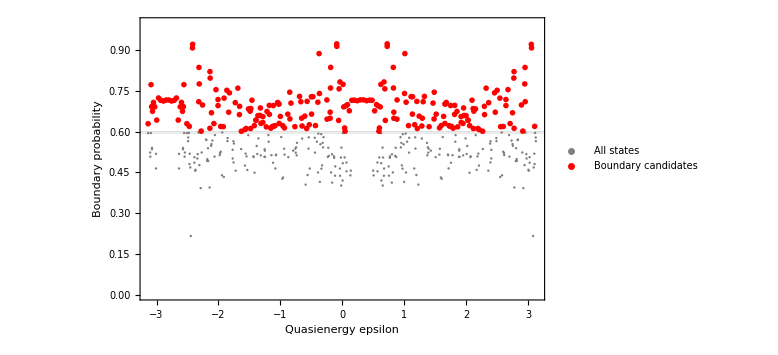

```mathematica
eigenenergies=-Arg[eigenvals];
borde=AnalyzeBoundaryEigenstates[grid,eigenvals,eigenvecs,BoundaryWidth->2,BoundaryThreshold->0.6];
Dataset[borde["Candidates"]]
borde["CandidateEnergies"]
PlotBoundarySpectrum[borde]
```

#### Chequeando Histograma

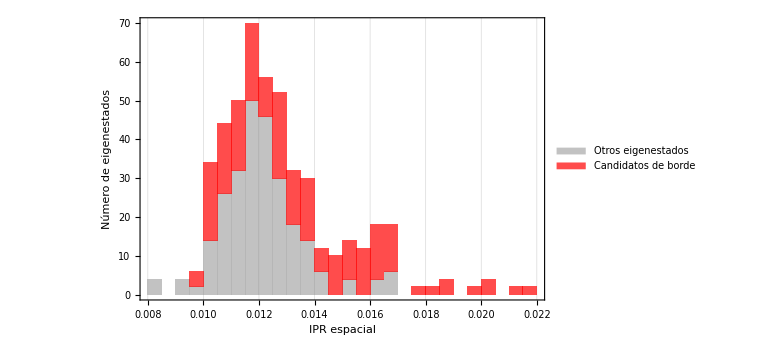

```mathematica
IPRdat=ComputeSpatialIPR[#,4]&/@eigenvecs;

indicesBorde=borde["CandidateIndices"];
indicesOtros=Complement[Range[Length[IPRdat]],indicesBorde];

iprBorde=IPRdat[[indicesBorde]];
iprOtros=IPRdat[[indicesOtros]];

(*Los mismos intervalos del histograma original*)
limites=First[HistogramList[IPRdat,"FreedmanDiaconis"]];
Histogram[{iprOtros,iprBorde},{limites},"Count",ChartLayout->"Stacked",ChartStyle->{Directive[GrayLevel[0.7],EdgeForm[None]],Directive[Red,EdgeForm[None]]},ChartLegends->{"Otros eigenestados","Candidatos de borde"},GridLines->{DeleteDuplicates[iprBorde],None},GridLinesStyle->Directive[Red,Opacity[0.6],Dotted,AbsoluteThickness[1.5]],Frame->True,Axes->False,FrameLabel->{"IPR espacial","Número de eigenestados"},PlotRange->All,ImageSize->Large]
```

#### visualizando los candidatos

```mathematica
candidatos=borde["CandidateEnergies"];
Module[{result},result=EigenstateAtEnergy[candidatos[[#]],eigenvals,eigenvecs];
DiscreteProbabilityPlot[grid,result["State"],InputType->"State",PlotLabel->"Desde amplitudes",ImageSize->200]]&/@Range[1,candidatos//Length]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Sinai

### Visualizando un caso particular. Graficando la densidad de ipr y checando un valor particular de la densidad según un nodo dado.

```mathematica
Lx=105;Ly=65;
grid=GenerateSinaiBasis[Lx,Ly];
pos={70,30};
coin=HaarRandomState[4];
initState=Normalize[LocalizedState[grid,pos,coin]+LocalizedState[grid,pos+{1,1},coin]];

iprdensity=ComputeSpatialIPRDensity[initState,4];

indexList=grid["Mapping"];
index=indexList[pos];
iprlocal=iprdensity[[index]]
DiscreteProbabilityPlot[grid,iprdensity]
```

### Comparando IPRs

#### Para estados localizados

```mathematica
SeedRandom[23];

(*Malla y estado inicial*)
Lx=140;
Ly=100;
grid=GenerateSinaiBasis[Lx,Ly];
pos={115,45};

coin=N[Normalize[HaarRandomState[4]]];
S=BuildShiftOperators[grid,CoinDimension->4];
initialState=LocalizedState[grid,pos,coin];

Tmax=2000;
nSites=grid["Dimension"];
names=RandomMatrixNames[];

(*Evolución de la IPR para cada tipo de moneda*)
iprDat=Module[{c=N[RandomMatrix[#]],evolutionOp},evolutionOp=QWEvolutionOperator[grid,SparseArray[c]];
ComputeSpatialIPREvolution[evolutionOp,initialState,Tmax,CoinDimension->4]]&/@names;
```

```mathematica
(*Clasificación:integrables hasta "gpg" inclusive*)cut=First[FirstPosition[names,"gpg"]];
nRegular=cut;
nChaotic=Length[names]-cut;

(*Colores individuales*)
regularColors={RGBColor["#0096B6"],(*p:turquesa*)RGBColor["#2878B5"],(*oo:azul*)RGBColor["#4650A4"],(*b:índigo*)RGBColor["#183153"]   (*gpg:azul marino*)};

chaoticColors={RGBColor["#D99A00"],(*o:ocre*)RGBColor["#E66B19"],(*uoou:naranja*)RGBColor["#C83F32"],(*ubu:rojo*)RGBColor["#84232E"],(*u:granate*)RGBColor["#A56832"]   (*upu:cobre*)};
(*Estilos de curvas y referencias*)
styles=Join[Directive[#,AbsoluteThickness[2.2]]&/@regularColors,Directive[#,AbsoluteThickness[2.2]]&/@chaoticColors,{Directive[GrayLevel[0.55],AbsoluteThickness[1.8],Dotted],Directive[RGBColor["#884DA7"],AbsoluteThickness[3],DotDashed],Directive[RGBColor["#368A56"],AbsoluteThickness[3],Dashed]}];

(*Referencias horizontales:1/N,2/N y 3/N*)
referenceValues={1/nSites,2/nSites,3/nSites};

references=Table[{{0,value},{Tmax,value}},{value,referenceValues}];

(*Inset:último 25 % del tiempo.Se supone que cada curva de iprDat contiene puntos {t,IPR}.*)
tInset=0.75 Tmax;

lateData=Select[#,First[#]>=tInset&]&/@iprDat;

lateReferences=Table[{{tInset,value},{Tmax,value}},{value,referenceValues}];

latePlot=ListLinePlot[Join[lateData,lateReferences],PlotStyle->styles,ScalingFunctions->{None,"Log"},PlotRange->{All,{0.00015,0.00035}},Frame->True,Axes->False,LabelStyle->Directive[Black,9],Background->White,ImagePadding->35];

(*Leyenda agrupada*)
legend=Framed[Column[{Grid[{{Column[{Style["Integrables",14,Bold,RGBColor["#183153"]],LineLegend[Take[styles,cut],Take[names,cut],LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->0.7],Column[{Style["Caóticas",14,Bold,RGBColor["#84232E"]],LineLegend[Take[styles,{cut+1,Length[names]}],Drop[names,cut],LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->0.7]}},Alignment->Top,Spacings->{2,0}],Style["Referencias",14,Bold,GrayLevel[0.25]],LineLegend[Take[styles,-3],{"Uniforme: 1/N","GUE: 2/N","GOE: 3/N"},LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->1],Background->White,FrameStyle->GrayLevel[0.85],FrameMargins->12,RoundingRadius->5];

(*Gráfico final*)
Img=Legended[ListLinePlot[Join[iprDat,references],PlotStyle->styles,ScalingFunctions->{None,"Log"},Frame->True,Axes->False,FrameLabel->{"Paso t","IPR espacial"},PlotLabel->"IPR\nComparación de monedas: integrabilidad y caos",GridLines->Automatic,PlotRange->All,ImageSize->900,LabelStyle->Directive[Bold,17],Epilog->{Inset[latePlot,Scaled[{0.7,0.6}],Center,Scaled[{0.35,0.35}]]}],Placed[legend,Right]]
```

```mathematica
Export[FileNameJoin[{root,"Imgs/IPR_CompCoins_Localized_Sinai.pdf"}],Img]
```

#### Para estados deslocalizados

Para dimensiones comparables con el sinai

```mathematica
L1=140;R1=100;
GridDataSinai=GenerateSinaiBasis[L1,R1];
dim=GridDataSinai["Dimension"];
aurea=GoldenRatio//N;
Ly=Floor[Sqrt[dim/aurea]];
Lx=Floor[Ly*aurea];
Print["Las dimensiones del rectangulo serían:","Lx= ",Lx,", Ly= ",Ly]
```

```mathematica
(*Malla y estado inicial*)
Lx=140;
Ly=100;
grid=GenerateSinaiBasis[Lx,Ly];
dim=grid["Dimension"];
S=BuildShiftOperators[grid,CoinDimension->4];
initialState=RandomDelocalizedState[dim,4,RandomSeed->7];

Tmax=2000;
nSites=grid["Dimension"];
names=RandomMatrixNames[];

(*Evolución de la IPR para cada tipo de moneda*)
iprDat=Module[{c=N[RandomMatrix[#]],evolutionOp},evolutionOp=QWEvolutionOperator[grid,SparseArray[c]];
ComputeSpatialIPREvolution[evolutionOp,initialState,Tmax,CoinDimension->4]]&/@names;
```

```mathematica
(*Clasificación:integrables hasta "gpg" inclusive*)cut=First[FirstPosition[names,"gpg"]];
nRegular=cut;
nChaotic=Length[names]-cut;

(*Colores individuales*)
regularColors={RGBColor["#0096B6"],(*p:turquesa*)RGBColor["#2878B5"],(*oo:azul*)RGBColor["#4650A4"],(*b:índigo*)RGBColor["#183153"]   (*gpg:azul marino*)};

chaoticColors={RGBColor["#D99A00"],(*o:ocre*)RGBColor["#E66B19"],(*uoou:naranja*)RGBColor["#C83F32"],(*ubu:rojo*)RGBColor["#84232E"],(*u:granate*)RGBColor["#A56832"]   (*upu:cobre*)};
(*Estilos de curvas y referencias*)
styles=Join[Directive[#,AbsoluteThickness[2.2]]&/@regularColors,Directive[#,AbsoluteThickness[2.2]]&/@chaoticColors,{Directive[GrayLevel[0.55],AbsoluteThickness[1.8],Dotted],Directive[RGBColor["#884DA7"],AbsoluteThickness[3],DotDashed],Directive[RGBColor["#368A56"],AbsoluteThickness[3],Dashed]}];

(*Referencias horizontales:1/N,2/N y 3/N*)
referenceValues={1/nSites,2/nSites,3/nSites};

references=Table[{{0,value},{Tmax,value}},{value,referenceValues}];

(*Inset:último 25 % del tiempo.Se supone que cada curva de iprDat contiene puntos {t,IPR}.*)
tInset=0.75 Tmax;

lateData=Select[#,First[#]>=tInset&]&/@iprDat;

lateReferences=Table[{{tInset,value},{Tmax,value}},{value,referenceValues}];

latePlot=ListLinePlot[Join[lateData,lateReferences],PlotStyle->styles,ScalingFunctions->{None,"Log"},PlotRange->{All,{0.00015,0.00035}},Frame->True,Axes->False,LabelStyle->Directive[Black,9],Background->White,ImagePadding->35];

(*Leyenda agrupada*)
legend=Framed[Column[{Grid[{{Column[{Style["Integrables",14,Bold,RGBColor["#183153"]],LineLegend[Take[styles,cut],Take[names,cut],LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->0.7],Column[{Style["Caóticas",14,Bold,RGBColor["#84232E"]],LineLegend[Take[styles,{cut+1,Length[names]}],Drop[names,cut],LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->0.7]}},Alignment->Top,Spacings->{2,0}],Style["Referencias",14,Bold,GrayLevel[0.25]],LineLegend[Take[styles,-3],{"Uniforme: 1/N","GUE: 2/N","GOE: 3/N"},LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->1],Background->White,FrameStyle->GrayLevel[0.85],FrameMargins->12,RoundingRadius->5];

(*Gráfico final*)
Img=Legended[ListLinePlot[Join[iprDat,references],PlotStyle->styles,ScalingFunctions->{None,"Log"},Frame->True,Axes->False,FrameLabel->{"Paso t","IPR espacial"},PlotLabel->"IPR\nComparación de monedas: integrabilidad y caos",GridLines->Automatic,PlotRange->All,ImageSize->900,LabelStyle->Directive[Bold,17],Epilog->{Inset[latePlot,Scaled[{0.6,0.75}],Center,Scaled[{0.35,0.35}]]}],Placed[legend,Right]]
```

```mathematica
Export[FileNameJoin[{root,"Imgs/IPR_CompCoins_DeLocalized_Sinai.pdf"}],Img]
```

### Densidad de IPR (Matrices Grandes)

#### Para eigenestados alrededor de un valor dado

Veamos la DoS y ver si cambio mucho con el tamaño

```mathematica
Lx=30;
Ly=30;
grid=GenerateRectangleBasis[Lx,Ly];

(*grid debe ser la malla del estadio*)
coinMatrix=N[RandomMatrix["upu"]];

S=BuildShiftOperators[grid,CoinDimension->4];

U=QWEvolutionOperator[grid,SparseArray[coinMatrix]];
eigenvals=U//Eigenvalues;
eigenphases=-Arg[eigenvals];

Histogram[eigenphases,Automatic,"PDF"]
```

```mathematica
Lx=80;
Ly=60;
grid=GenerateRectangleBasis[Lx,Ly];

coinMatrix=N[RandomMatrix["b"]];
S=BuildShiftOperators[grid,CoinDimension->4];

U=N[QWEvolutionOperator[grid,SparseArray[coinMatrix]]];

(*Parámetros ajustables*)
k=10;
columns=3;
epsilon0=0.4;

sigma=1.001 Exp[-I epsilon0];

(*Ajustar la base de Arnoldi al número solicitado*)
basisSize=Min[Length[U],Max[60,2 k+10]];

{eigenvalues,eigenvectors}=Eigensystem[U,-k,Method->{"Arnoldi","Shift"->sigma,"BasisSize"->basisSize,"MaxIterations"->5000,"Tolerance"->10^-10}];

eigenvectors=Normalize/@eigenvectors;
eigenphases=-Arg[eigenvalues];

(*Ordenar por eigenfase*)
order=Ordering[eigenphases];
eigenvalues=eigenvalues[[order]];
eigenvectors=eigenvectors[[order]];
eigenphases=eigenphases[[order]];

residuals=MapThread[Norm[U.#2-#1 #2]&,{eigenvalues,eigenvectors}];

nFound=Length[eigenvectors];

densities=ComputeSpatialIPRDensity[#,4]&/@eigenvectors;
iprValues=Total/@densities;

(*Resumen*)
summary=Grid[Prepend[Table[{j,NumberForm[eigenphases[[j]],{6,4}],ScientificForm[residuals[[j]],3],ScientificForm[iprValues[[j]],3]},{j,nFound}],{"Estado","ε","Residuo","IPR"}],Frame->All];

(*Un panel por eigenestado*)
plots=Table[DiscreteProbabilityPlot[grid,densities[[j]],ProbabilityScale->"Linear",PlotLabel->Column[{Row[{"Estado ",j,"; ε = ",NumberForm[eigenphases[[j]],{6,4}]}],Row[{"IPR = ",ScientificForm[iprValues[[j]],3]}]},Alignment->Center],ImageSize->350],{j,nFound}];

(*Completar únicamente los espacios vacíos de la última fila*)
rows=Ceiling[nFound/columns];

Column[{summary,GraphicsGrid[Partition[PadRight[plots,rows columns,Null],columns],Spacings->{0.4,0.6},ImageSize->400 columns]}]

GraphicsGrid[Partition[PadRight[plots,6,Null],3],Spacings->{0.4,0.6},ImageSize->1200]
```

#### Tomando eigenestados en puntos distintos del espectro de energías

```mathematica
(*Malla y operador de evolución*)
Lx=100;
Ly=75;
grid=GenerateSinaiBasis[Lx,Ly];

coinMatrix=N[RandomMatrix["oo"]];
S=BuildShiftOperators[grid,CoinDimension->4];

U=N[QWEvolutionOperator[grid,SparseArray[coinMatrix]]];

(*Seis intervalos y sus centros*)
k=10;
edges=Subdivide[-Pi,Pi,k];
intervals=Partition[edges,2,1];
targets=Mean/@intervals;

(*Un eigenestado próximo al centro de cada intervalo*)
eigenData=Table[Module[{sigma,vals,vecs,psi,phase,residual},sigma=1.001 Exp[-I targets[[j]]];
{vals,vecs}=Check[Eigensystem[U,-1,Method->{"Arnoldi","Shift"->sigma,"BasisSize"->60,"MaxIterations"->5000,"Tolerance"->10^-10}],Print["No convergió la búsqueda del intervalo ",j];
Abort[]];
psi=Normalize[First[vecs]];
phase=-Arg[First[vals]];
residual=Norm[U.psi-First[vals] psi];
(*No asignar a un intervalo un estado que quedó fuera*)If[!TrueQ[intervals[[j,1]]<=phase<=intervals[[j,2]]],Print["El eigenestado encontrado para el intervalo ",j," quedó fuera: ε = ",phase,". Revisa la búsqueda o si hay espectro en ese intervalo."];
Abort[]];
If[residual>10^-8,Print["Residuo demasiado grande en el intervalo ",j,": ",residual];
Abort[]];
{First[vals],psi,phase,residual}],{j,k}];

eigenvalues=eigenData[[All,1]];
eigenvectors=eigenData[[All,2]];
eigenphases=eigenData[[All,3]];
residuals=eigenData[[All,4]];

densities=ComputeSpatialIPRDensity[#,4]&/@eigenvectors;
iprValues=Total/@densities;

(*Resumen:objetivo,eigenfase encontrada,residuo e IPR*)
summary=Grid[Prepend[Table[{j,NumberForm[N[targets[[j]]],{6,4}],NumberForm[eigenphases[[j]],{6,4}],ScientificForm[residuals[[j]],3],ScientificForm[iprValues[[j]],3]},{j,k}],{"Intervalo","ε objetivo","ε encontrada","Residuo","IPR"}],Frame->All];
(*Configuración de la visualización*)columns=3;
nPlots=Length[eigenvectors];

(*Mapas con títulos externos y leyendas normalizadas*)
plots=Table[Module[{density,dmax,header,graphic},density=densities[[j]];
dmax=Max[density];
header=Row[{"Intervalo ",j,": ",NumberForm[N[intervals[[j,1]]],{4,2}]," a ",NumberForm[N[intervals[[j,2]]],{4,2}]}];
graphic=DiscreteProbabilityPlot[grid,density,ProbabilityScale->"Linear",ProbabilityRange->{0,dmax},ColorFunction->(GrayLevel[1-#]&),PlotLabel->None,FrameLabel->{"x","y"},LabelStyle->Directive[Black,11],ImagePadding->{{45,15},{45,15}},ImageSize->320,PlotLegends->With[{upper=dmax},Placed[BarLegend[{Function[value,GrayLevel[1-Clip[value/upper,{0,1}]]],{0,upper}},LegendLabel->"Iₙ",LegendMarkerSize->{18,180},LabelStyle->Directive[Black,10]],Right]]];
Column[{Style[header,12,Bold],Style[Row[{"ε = ",NumberForm[eigenphases[[j]],{6,4}],"   IPR = ",ScientificForm[iprValues[[j]],3]}],11],Style[Row[{"Residuo = ",ScientificForm[residuals[[j]],2]}],10,GrayLevel[0.35]],graphic},Alignment->Center,Spacings->0.4]],{j,nPlots}];

(*Completar la última fila sin perder paneles*)
panel=Grid[Partition[PadRight[plots,columns Ceiling[nPlots/columns],""],columns],Alignment->{Center,Top},Spacings->{2,2}];

(*Una única imagen con todos los mapas*)
imagen=Rasterize[panel,"Image",ImageResolution->200];

imagen
```

### Densidad de IPR (Matrices Pequeñas)

```mathematica
(*Malla y operador*)
Lx=60;
Ly=25;
grid=GenerateSinaiBasis[Lx,Ly];

coinMatrix=N[RandomMatrix["b"]];
S=BuildShiftOperators[grid,CoinDimension->4];

U=N[QWEvolutionOperator[grid,SparseArray[coinMatrix]]];

(*Espectro completo:eigenvalores y vectores correspondientes*)
{eigenvalues,eigenvectors}=Eigensystem[Normal[U]];
eigenvectors=Normalize/@eigenvectors;
eigenphases=-Arg[eigenvalues];
```

```mathematica
(*Dividir las eigenfases en subintervalos*)
nIntervals=8;
columns=4;

edges=N[Subdivide[-Pi,Pi,nIntervals]];
intervals=Partition[edges,2,1];
centers=Mean/@intervals;

(*Seleccionar un eigenestado cercano al centro de cada intervalo*)
selectedIndices=Table[Module[{candidates},candidates=Select[Range[Length[eigenphases]],Function[index,intervals[[j,1]]<=eigenphases[[index]]&&If[j==nIntervals,eigenphases[[index]]<=intervals[[j,2]],eigenphases[[index]]<intervals[[j,2]]]]];
If[candidates==={},Missing["EmptyInterval"],First[MinimalBy[candidates,Abs[eigenphases[[#]]-centers[[j]]]&]]]],{j,nIntervals}];

(*Construir cada panel*)
plots=Table[Module[{index,density,residual,header,graphic,dmax},index=selectedIndices[[j]];
header=Row[{"Intervalo ",j,": ",NumberForm[intervals[[j,1]],{4,2}]," a ",NumberForm[intervals[[j,2]],{4,2}]}];
If[MissingQ[index],Column[{Style[header,12,Bold],"Sin eigenestados"},Alignment->Center],density=ComputeSpatialIPRDensity[eigenvectors[[index]],4];
dmax=Max[density];
residual=Norm[U.eigenvectors[[index]]-eigenvalues[[index]] eigenvectors[[index]]];
graphic=DiscreteProbabilityPlot[grid,density,ProbabilityScale->"Linear",ProbabilityRange->{0,dmax},ColorFunction->(GrayLevel[1-#]&),PlotLabel->None,FrameLabel->{"x","y"},LabelStyle->Directive[Black,11],ImagePadding->{{45,15},{45,15}},ImageSize->320,(*Leyenda:normalizar la densidad para asignar el color*)PlotLegends->With[{upper=dmax},Placed[BarLegend[{Function[value,GrayLevel[1-Clip[value/upper,{0,1}]]],{0,upper}},LegendLabel->"Iₙ",LegendMarkerSize->{18,180},LabelStyle->Directive[Black,10]],Right]]];
Column[{Style[header,12,Bold],Style[Row[{"ε = ",NumberForm[eigenphases[[index]],{6,4}],"   IPR = ",ScientificForm[Total[density],3]}],11],Style[Row[{"Residuo = ",ScientificForm[residual,2]}],10,GrayLevel[0.35]],graphic},Alignment->Center,Spacings->0.4]]],{j,nIntervals}];

(*Organizar los paneles*)
panel=Grid[Partition[PadRight[plots,columns Ceiling[nIntervals/columns],""],columns],Alignment->{Center,Top},Spacings->{2,2}];

(*Convertir el conjunto en una única imagen*)
imagen=Rasterize[panel,"Image",ImageResolution->200];

imagen
```

R=25

R=0

### Tratando de hallar estados de borde mediante a IPR

```mathematica
SeedRandom[23];
Lx=60;
Ly=45;
grid=GenerateSinaiBasis[Lx,Ly];
S=BuildShiftOperators[grid,CoinDimension->4];
nSites=grid["Dimension"];
c=N[RandomMatrix["oo"]];
evolutionOp=QWEvolutionOperator[grid,SparseArray[c]];
(*Eigenvalores y eigenvectores,en el mismo orden*)
{eigenvals,eigenvecs}=Eigensystem[Normal[evolutionOp]];
```

#### IPR vs cuasiEnergías

```mathematica
eigenenergies=-Arg[eigenvals];
borde=AnalyzeBoundaryEigenstates[grid,eigenvals,eigenvecs,BoundaryWidth->2,BoundaryThreshold->0.6];

Dataset[borde["Candidates"]]
borde["CandidateEnergies"]
PlotBoundarySpectrum[borde]
```

```mathematica
candidatos=borde["CandidateEnergies"];
imgs=Module[{result},result=EigenstateAtEnergy[candidatos[[#]],eigenvals,eigenvecs];
DiscreteProbabilityPlot[grid,result["State"],InputType->"State",PlotLabel->"Desde amplitudes",ImageSize->200]]&/@Range[1,candidatos//Length]
```

#### Chequeando Histograma

```mathematica
IPRdat=ComputeSpatialIPR[#,4]&/@eigenvecs;

indicesBorde=borde["CandidateIndices"];
indicesOtros=Complement[Range[Length[IPRdat]],indicesBorde];

iprBorde=IPRdat[[indicesBorde]];
iprOtros=IPRdat[[indicesOtros]];

(*Los mismos intervalos del histograma original*)
limites=First[HistogramList[IPRdat,"FreedmanDiaconis"]];
Histogram[{iprOtros,iprBorde},{limites},"Count",ChartLayout->"Stacked",ChartStyle->{Directive[GrayLevel[0.7],EdgeForm[None]],Directive[Red,EdgeForm[None]]},ChartLegends->{"Otros eigenestados","Candidatos de borde"},GridLines->{DeleteDuplicates[iprBorde],None},GridLinesStyle->Directive[Red,Opacity[0.6],Dotted,AbsoluteThickness[1.5]],Frame->True,Axes->False,FrameLabel->{"IPR espacial","Número de eigenestados"},PlotRange->All,ImageSize->Large]
```

## IPR Total

## Rectangulo

### Comparando IPRs

#### Para estados localizados

Para dimensiones comparables con el sinai

```mathematica
L1=140;R1=100;
GridDataSinai=GenerateSinaiBasis[L1,R1];
dim=GridDataSinai["Dimension"];
aurea=GoldenRatio//N;
Ly=Floor[Sqrt[dim/aurea]];
Lx=Floor[Ly*aurea];
Print["Las dimensiones del rectangulo serían:","Lx= ",Lx,", Ly= ",Ly]
```

Las dimensiones del rectangulo serían:Lx= 97, Ly= 60

```mathematica
SeedRandom[23];

(*Malla y estado inicial*)
Lx=97;
Ly=60;
grid=GenerateRectangleBasis[Lx,Ly];
pos={35,35};

coin=N[Normalize[HaarRandomState[4]]];
initialState=LocalizedState[grid,pos,coin];

Tmax=2000;
names=RandomMatrixNames[];
(*Evolución de la IPR para cada tipo de moneda*)
iprTotDat=Table[Module[{c=N[RandomMatrix[name]],evolutionOp,state=N[Normal[initialState]],ipr},evolutionOp=QWEvolutionOperator[grid,c];
Table[ipr=ComputeTotalIPR[state];
If[t<Tmax,state=evolutionOp.state];
ipr,{t,0,Tmax}]],{name,names}];
```

```mathematica
(*Dimensión completa:posición y moneda*)dimTotal=Length[initialState];

(*Convertir listas de valores a puntos {t,IPR}.También admite series que ya contienen esos puntos.*)
iprTotPoints=Map[If[VectorQ[#,NumericQ],Transpose[{Range[0,Length[#]-1],#}],#]&,iprTotDat];

tMaxPlot=Max[iprTotPoints[[All,-1,1]]];

(*Conservar tu clasificación de monedas*)
cut=First[FirstPosition[names,"gpg"]];
nRegular=cut;
nChaotic=Length[names]-cut;

(*Colores individuales*)
regularColors={RGBColor["#0096B6"],(*p:turquesa*)RGBColor["#2878B5"],(*oo:azul*)RGBColor["#4650A4"],(*b:índigo*)RGBColor["#183153"]  (*gpg:azul marino*)};

chaoticColors={RGBColor["#D99A00"],(*o:ocre*)RGBColor["#E66B19"],(*uoou:naranja*)RGBColor["#C83F32"],(*ubu:rojo*)RGBColor["#84232E"],(*u:granate*)RGBColor["#A56832"]  (*upu:cobre*)};

(*Estilos de curvas y referencias*)
styles=Join[Directive[#,AbsoluteThickness[2.2]]&/@regularColors,Directive[#,AbsoluteThickness[2.2]]&/@chaoticColors,{Directive[GrayLevel[0.55],AbsoluteThickness[1.8],Dotted],Directive[RGBColor["#884DA7"],AbsoluteThickness[3],DotDashed],Directive[RGBColor["#368A56"],AbsoluteThickness[3],Dashed]}];

(*Referencias para estados que exploran toda la base*)
referenceValues={1/dimTotal,2/(dimTotal+1),3/(dimTotal+2)};

referenceLabels={"Uniforme: 1/D","Haar complejo: 2/(D+1)","Haar real: 3/(D+2)"};

references=Table[{{0,value},{tMaxPlot,value}},{value,referenceValues}];

(*Inset:último 25 % del tiempo*)
tInset=0.75 tMaxPlot;

lateData=Select[#,First[#]>=tInset&]&/@iprTotPoints;

lateReferences=Table[{{tInset,value},{tMaxPlot,value}},{value,referenceValues}];

(*Ajustar el rango vertical a las curvas del grupo Caóticas y las referencias.También se dibujan las curvas Integrables.*)
insetValues=Join[Flatten[lateData[[cut+1;;,All,2]]],N[referenceValues]];

insetRange={Min[insetValues]/1.15,1.15 Max[insetValues]};

latePlot=ListLinePlot[Join[lateData,lateReferences],PlotStyle->styles,ScalingFunctions->{None,"Log"},PlotRange->{{tInset,tMaxPlot},insetRange},Frame->True,Axes->False,LabelStyle->Directive[Black,9],Background->White,ImagePadding->{{55,10},{35,10}},ImageSize->400];

(*Leyenda agrupada*)
legend=Framed[Column[{Grid[{{Column[{Style["Integrables",14,Bold,RGBColor["#183153"]],LineLegend[Take[styles,cut],Take[names,cut],LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->0.7],Column[{Style["Caóticas",14,Bold,RGBColor["#84232E"]],LineLegend[Take[styles,{cut+1,Length[names]}],Drop[names,cut],LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->0.7]}},Alignment->Top,Spacings->{2,0}],Style["Referencias (D = "<>ToString[dimTotal]<>")",14,Bold,GrayLevel[0.25]],LineLegend[Take[styles,-3],referenceLabels,LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->1],Background->White,FrameStyle->GrayLevel[0.85],FrameMargins->12,RoundingRadius->5];

(*Gráfico final*)
Img=Legended[ListLinePlot[Join[iprTotPoints,references],PlotStyle->styles,ScalingFunctions->{None,"Log"},Frame->True,Axes->False,FrameLabel->{"Paso t","IPR total (posición y moneda)"},PlotLabel->"IPR total\nComparación de monedas",GridLines->Automatic,PlotRange->All,ImageSize->900,LabelStyle->Directive[Bold,17],Epilog->{Inset[latePlot,Scaled[{0.80,0.60}],Center,Scaled[{0.45,0.45}]]}],Placed[legend,Right]];

Img
```

-Graphics-

```mathematica
Export[FileNameJoin[{root,"Imgs/IPRTotal_CompCoins_Localized_Rect.pdf"}],Img]
```

/Users/saul/Desktop/ChatGPT/QWProgramming/Imgs/IPRTotal_CompCoins_Localized_Rect.pdf

#### Para estados deslocalizados

Para dimensiones comparables con el sinai

```mathematica
L1=140;R1=100;
GridDataSinai=GenerateSinaiBasis[L1,R1];
dim=GridDataSinai["Dimension"];
aurea=GoldenRatio//N;
Ly=Floor[Sqrt[dim/aurea]];
Lx=Floor[Ly*aurea];
Print["Las dimensiones del rectangulo serían:","Lx= ",Lx,", Ly= ",Ly]
```

Las dimensiones del rectangulo serían:Lx= 97, Ly= 60

```mathematica
SeedRandom[23];

(*Malla y estado inicial*)
Lx=97;
Ly=60;
grid=GenerateRectangleBasis[Lx,Ly];

dim=grid["Dimension"];
initialState=RandomDelocalizedState[dim,4,RandomSeed->7];
Tmax=2000;
names=RandomMatrixNames[];
(*Evolución de la IPR para cada tipo de moneda*)
iprTotDat=Table[Module[{c=N[RandomMatrix[name]],evolutionOp,state=N[Normal[initialState]],ipr},evolutionOp=QWEvolutionOperator[grid,c];
Table[ipr=ComputeTotalIPR[state];
If[t<Tmax,state=evolutionOp.state];
ipr,{t,0,Tmax}]],{name,names}];
```

```mathematica
(*Dimensión completa:posición y moneda*)dimTotal=Length[initialState];

(*Convertir listas de valores a puntos {t,IPR}.También admite series que ya contienen esos puntos.*)
iprTotPoints=Map[If[VectorQ[#,NumericQ],Transpose[{Range[0,Length[#]-1],#}],#]&,iprTotDat];

tMaxPlot=Max[iprTotPoints[[All,-1,1]]];

(*Conservar tu clasificación de monedas*)
cut=First[FirstPosition[names,"gpg"]];
nRegular=cut;
nChaotic=Length[names]-cut;

(*Colores individuales*)
regularColors={RGBColor["#0096B6"],(*p:turquesa*)RGBColor["#2878B5"],(*oo:azul*)RGBColor["#4650A4"],(*b:índigo*)RGBColor["#183153"]  (*gpg:azul marino*)};

chaoticColors={RGBColor["#D99A00"],(*o:ocre*)RGBColor["#E66B19"],(*uoou:naranja*)RGBColor["#C83F32"],(*ubu:rojo*)RGBColor["#84232E"],(*u:granate*)RGBColor["#A56832"]  (*upu:cobre*)};

(*Estilos de curvas y referencias*)
styles=Join[Directive[#,AbsoluteThickness[2.2]]&/@regularColors,Directive[#,AbsoluteThickness[2.2]]&/@chaoticColors,{Directive[GrayLevel[0.55],AbsoluteThickness[1.8],Dotted],Directive[RGBColor["#884DA7"],AbsoluteThickness[3],DotDashed],Directive[RGBColor["#368A56"],AbsoluteThickness[3],Dashed]}];

(*Referencias para estados que exploran toda la base*)
referenceValues={1/dimTotal,2/(dimTotal+1),3/(dimTotal+2)};

referenceLabels={"Uniforme: 1/D","Haar complejo: 2/(D+1)","Haar real: 3/(D+2)"};

references=Table[{{0,value},{tMaxPlot,value}},{value,referenceValues}];

(*Inset:último 25 % del tiempo*)
tInset=0.75 tMaxPlot;

lateData=Select[#,First[#]>=tInset&]&/@iprTotPoints;

lateReferences=Table[{{tInset,value},{tMaxPlot,value}},{value,referenceValues}];

(*Ajustar el rango vertical a las curvas del grupo Caóticas y las referencias.También se dibujan las curvas Integrables.*)
insetValues=Join[Flatten[lateData[[cut+1;;,All,2]]],N[referenceValues]];

insetRange={Min[insetValues]/1.15,1.15 Max[insetValues]};

latePlot=ListLinePlot[Join[lateData,lateReferences],PlotStyle->styles,ScalingFunctions->{None,"Log"},PlotRange->{{tInset,tMaxPlot},insetRange},Frame->True,Axes->False,LabelStyle->Directive[Black,9],Background->White,ImagePadding->{{55,10},{35,10}},ImageSize->400];

(*Leyenda agrupada*)
legend=Framed[Column[{Grid[{{Column[{Style["Integrables",14,Bold,RGBColor["#183153"]],LineLegend[Take[styles,cut],Take[names,cut],LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->0.7],Column[{Style["Caóticas",14,Bold,RGBColor["#84232E"]],LineLegend[Take[styles,{cut+1,Length[names]}],Drop[names,cut],LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->0.7]}},Alignment->Top,Spacings->{2,0}],Style["Referencias (D = "<>ToString[dimTotal]<>")",14,Bold,GrayLevel[0.25]],LineLegend[Take[styles,-3],referenceLabels,LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->1],Background->White,FrameStyle->GrayLevel[0.85],FrameMargins->12,RoundingRadius->5];

(*Gráfico final*)
Img=Legended[ListLinePlot[Join[iprTotPoints,references],PlotStyle->styles,ScalingFunctions->{None,"Log"},Frame->True,Axes->False,FrameLabel->{"Paso t","IPR total (posición y moneda)"},PlotLabel->"IPR total\nComparación de monedas",GridLines->Automatic,PlotRange->All,ImageSize->900,LabelStyle->Directive[Bold,17],Epilog->{Inset[latePlot,Scaled[{0.5,0.25}],Center,Scaled[{0.4,0.4}]]}],Placed[legend,Right]];

Img
```

-Graphics-

```mathematica
Export[FileNameJoin[{root,"Imgs/IPRTotal_CompCoins_DeLocalized_Rect.pdf"}],Img]
```

/Users/saul/Desktop/ChatGPT/QWProgramming/Imgs/IPRTotal_CompCoins_DeLocalized_Rect.pdf

## Sinai

### Comparando IPRs

#### Para estados localizados

Para dimensiones comparables con el sinai

```mathematica
L1=140;R1=100;
GridDataSinai=GenerateSinaiBasis[L1,R1];
dim=GridDataSinai["Dimension"];
aurea=GoldenRatio//N;
Ly=Floor[Sqrt[dim/aurea]];
Lx=Floor[Ly*aurea];
Print["Las dimensiones del rectangulo serían:","Lx= ",Lx,", Ly= ",Ly]
```

Las dimensiones del rectangulo serían:Lx= 97, Ly= 60

```mathematica
SeedRandom[23];

(*Malla y estado inicial*)
Lx=140;
Ly=100;
grid=GenerateSinaiBasis[Lx,Ly];
pos={115,45};

coin=N[Normalize[HaarRandomState[4]]];
initialState=LocalizedState[grid,pos,coin];

Tmax=2000;
names=RandomMatrixNames[];
(*Evolución de la IPR para cada tipo de moneda*)
iprTotDat=Table[Module[{c=N[RandomMatrix[name]],evolutionOp,state=N[Normal[initialState]],ipr},evolutionOp=QWEvolutionOperator[grid,c];
Table[ipr=ComputeTotalIPR[state];
If[t<Tmax,state=evolutionOp.state];
ipr,{t,0,Tmax}]],{name,names}];
```

```mathematica
(*Dimensión completa:posición y moneda*)dimTotal=Length[initialState];

(*Convertir listas de valores a puntos {t,IPR}.También admite series que ya contienen esos puntos.*)
iprTotPoints=Map[If[VectorQ[#,NumericQ],Transpose[{Range[0,Length[#]-1],#}],#]&,iprTotDat];

tMaxPlot=Max[iprTotPoints[[All,-1,1]]];

(*Conservar tu clasificación de monedas*)
cut=First[FirstPosition[names,"gpg"]];
nRegular=cut;
nChaotic=Length[names]-cut;

(*Colores individuales*)
regularColors={RGBColor["#0096B6"],(*p:turquesa*)RGBColor["#2878B5"],(*oo:azul*)RGBColor["#4650A4"],(*b:índigo*)RGBColor["#183153"]  (*gpg:azul marino*)};

chaoticColors={RGBColor["#D99A00"],(*o:ocre*)RGBColor["#E66B19"],(*uoou:naranja*)RGBColor["#C83F32"],(*ubu:rojo*)RGBColor["#84232E"],(*u:granate*)RGBColor["#A56832"]  (*upu:cobre*)};

(*Estilos de curvas y referencias*)
styles=Join[Directive[#,AbsoluteThickness[2.2]]&/@regularColors,Directive[#,AbsoluteThickness[2.2]]&/@chaoticColors,{Directive[GrayLevel[0.55],AbsoluteThickness[1.8],Dotted],Directive[RGBColor["#884DA7"],AbsoluteThickness[3],DotDashed],Directive[RGBColor["#368A56"],AbsoluteThickness[3],Dashed]}];

(*Referencias para estados que exploran toda la base*)
referenceValues={1/dimTotal,2/(dimTotal+1),3/(dimTotal+2)};

referenceLabels={"Uniforme: 1/D","Haar complejo: 2/(D+1)","Haar real: 3/(D+2)"};

references=Table[{{0,value},{tMaxPlot,value}},{value,referenceValues}];

(*Inset:último 25 % del tiempo*)
tInset=0.75 tMaxPlot;

lateData=Select[#,First[#]>=tInset&]&/@iprTotPoints;

lateReferences=Table[{{tInset,value},{tMaxPlot,value}},{value,referenceValues}];

(*Ajustar el rango vertical a las curvas del grupo Caóticas y las referencias.También se dibujan las curvas Integrables.*)
insetValues=Join[Flatten[lateData[[cut+1;;,All,2]]],N[referenceValues]];

insetRange={Min[insetValues]/1.15,1.15 Max[insetValues]};

latePlot=ListLinePlot[Join[lateData,lateReferences],PlotStyle->styles,ScalingFunctions->{None,"Log"},PlotRange->{{tInset,tMaxPlot},insetRange},Frame->True,Axes->False,LabelStyle->Directive[Black,9],Background->White,ImagePadding->{{55,10},{35,10}},ImageSize->400];

(*Leyenda agrupada*)
legend=Framed[Column[{Grid[{{Column[{Style["Integrables",14,Bold,RGBColor["#183153"]],LineLegend[Take[styles,cut],Take[names,cut],LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->0.7],Column[{Style["Caóticas",14,Bold,RGBColor["#84232E"]],LineLegend[Take[styles,{cut+1,Length[names]}],Drop[names,cut],LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->0.7]}},Alignment->Top,Spacings->{2,0}],Style["Referencias (D = "<>ToString[dimTotal]<>")",14,Bold,GrayLevel[0.25]],LineLegend[Take[styles,-3],referenceLabels,LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->1],Background->White,FrameStyle->GrayLevel[0.85],FrameMargins->12,RoundingRadius->5];

(*Gráfico final*)
Img=Legended[ListLinePlot[Join[iprTotPoints,references],PlotStyle->styles,ScalingFunctions->{None,"Log"},Frame->True,Axes->False,FrameLabel->{"Paso t","IPR total (posición y moneda)"},PlotLabel->"IPR total\nComparación de monedas",GridLines->Automatic,PlotRange->All,ImageSize->900,LabelStyle->Directive[Bold,17],Epilog->{Inset[latePlot,Scaled[{0.80,0.60}],Center,Scaled[{0.45,0.45}]]}],Placed[legend,Right]];

Img
```

-Graphics-

```mathematica
Export[FileNameJoin[{root,"Imgs/IPRTot_CompCoins_Localized_Sinai.pdf"}],Img]
```

/Users/saul/Desktop/ChatGPT/QWProgramming/Imgs/IPRTot_CompCoins_Localized_Sinai.pdf

#### Para estados deslocalizados

Para dimensiones comparables con el sinai

```mathematica
L1=140;R1=100;
GridDataSinai=GenerateSinaiBasis[L1,R1];
dim=GridDataSinai["Dimension"];
aurea=GoldenRatio//N;
Ly=Floor[Sqrt[dim/aurea]];
Lx=Floor[Ly*aurea];
Print["Las dimensiones del rectangulo serían:","Lx= ",Lx,", Ly= ",Ly]
```

Las dimensiones del rectangulo serían:Lx= 97, Ly= 60

```mathematica
SeedRandom[23];

(*Malla y estado inicial*)
Lx=140;
Ly=100;
grid=GenerateSinaiBasis[Lx,Ly];
dim=grid["Dimension"];
initialState=RandomDelocalizedState[dim,4,RandomSeed->7];
Tmax=2000;
names=RandomMatrixNames[];
(*Evolución de la IPR para cada tipo de moneda*)
iprTotDat=Table[Module[{c=N[RandomMatrix[name]],evolutionOp,state=N[Normal[initialState]],ipr},evolutionOp=QWEvolutionOperator[grid,c];
Table[ipr=ComputeTotalIPR[state];
If[t<Tmax,state=evolutionOp.state];
ipr,{t,0,Tmax}]],{name,names}];
```

```mathematica
(*Dimensión completa:posición y moneda*)dimTotal=Length[initialState];

(*Convertir listas de valores a puntos {t,IPR}.También admite series que ya contienen esos puntos.*)
iprTotPoints=Map[If[VectorQ[#,NumericQ],Transpose[{Range[0,Length[#]-1],#}],#]&,iprTotDat];

tMaxPlot=Max[iprTotPoints[[All,-1,1]]];

(*Conservar tu clasificación de monedas*)
cut=First[FirstPosition[names,"gpg"]];
nRegular=cut;
nChaotic=Length[names]-cut;

(*Colores individuales*)
regularColors={RGBColor["#0096B6"],(*p:turquesa*)RGBColor["#2878B5"],(*oo:azul*)RGBColor["#4650A4"],(*b:índigo*)RGBColor["#183153"]  (*gpg:azul marino*)};

chaoticColors={RGBColor["#D99A00"],(*o:ocre*)RGBColor["#E66B19"],(*uoou:naranja*)RGBColor["#C83F32"],(*ubu:rojo*)RGBColor["#84232E"],(*u:granate*)RGBColor["#A56832"]  (*upu:cobre*)};

(*Estilos de curvas y referencias*)
styles=Join[Directive[#,AbsoluteThickness[2.2]]&/@regularColors,Directive[#,AbsoluteThickness[2.2]]&/@chaoticColors,{Directive[GrayLevel[0.55],AbsoluteThickness[1.8],Dotted],Directive[RGBColor["#884DA7"],AbsoluteThickness[3],DotDashed],Directive[RGBColor["#368A56"],AbsoluteThickness[3],Dashed]}];

(*Referencias para estados que exploran toda la base*)
referenceValues={1/dimTotal,2/(dimTotal+1),3/(dimTotal+2)};

referenceLabels={"Uniforme: 1/D","Haar complejo: 2/(D+1)","Haar real: 3/(D+2)"};

references=Table[{{0,value},{tMaxPlot,value}},{value,referenceValues}];

(*Inset:último 25 % del tiempo*)
tInset=0.75 tMaxPlot;

lateData=Select[#,First[#]>=tInset&]&/@iprTotPoints;

lateReferences=Table[{{tInset,value},{tMaxPlot,value}},{value,referenceValues}];

(*Ajustar el rango vertical a las curvas del grupo Caóticas y las referencias.También se dibujan las curvas Integrables.*)
insetValues=Join[Flatten[lateData[[cut+1;;,All,2]]],N[referenceValues]];

insetRange={Min[insetValues]/1.15,1.15 Max[insetValues]};

latePlot=ListLinePlot[Join[lateData,lateReferences],PlotStyle->styles,ScalingFunctions->{None,"Log"},PlotRange->{{tInset,tMaxPlot},insetRange},Frame->True,Axes->False,LabelStyle->Directive[Black,9],Background->White,ImagePadding->{{55,10},{35,10}},ImageSize->400];

(*Leyenda agrupada*)
legend=Framed[Column[{Grid[{{Column[{Style["Integrables",14,Bold,RGBColor["#183153"]],LineLegend[Take[styles,cut],Take[names,cut],LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->0.7],Column[{Style["Caóticas",14,Bold,RGBColor["#84232E"]],LineLegend[Take[styles,{cut+1,Length[names]}],Drop[names,cut],LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->0.7]}},Alignment->Top,Spacings->{2,0}],Style["Referencias (D = "<>ToString[dimTotal]<>")",14,Bold,GrayLevel[0.25]],LineLegend[Take[styles,-3],referenceLabels,LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->1],Background->White,FrameStyle->GrayLevel[0.85],FrameMargins->12,RoundingRadius->5];

(*Gráfico final*)
Img=Legended[ListLinePlot[Join[iprTotPoints,references],PlotStyle->styles,ScalingFunctions->{None,"Log"},Frame->True,Axes->False,FrameLabel->{"Paso t","IPR total (posición y moneda)"},PlotLabel->"IPR total\nComparación de monedas",GridLines->Automatic,PlotRange->All,ImageSize->900,LabelStyle->Directive[Bold,17],Epilog->{Inset[latePlot,Scaled[{0.60,0.75}],Center,Scaled[{0.4,0.4}]]}],Placed[legend,Right]];

Img
```

-Graphics-

```mathematica
Export[FileNameJoin[{root,"Imgs/IPRTot_CompCoins_DeLocalized_Sinai.pdf"}],Img]
```

/Users/saul/Desktop/ChatGPT/QWProgramming/Imgs/IPRTot_CompCoins_DeLocalized_Sinai.pdf

## Entropía de entrelazamiento

## Rectangulo

### Un caso particular

```mathematica
SeedRandom[23];

(*Malla y estado inicial*)
Lx=80;
Ly=50;
grid=GenerateRectangleBasis[Lx,Ly];
pos={35,35};

coin=N[Normalize[HaarRandomState[4]]];
S=BuildShiftOperators[grid,CoinDimension->4];
initialState=LocalizedState[grid,pos,coin];

Tmax=100;
c=N[RandomMatrix["oo"]];
evolutionOp=QWEvolutionOperator[grid,SparseArray[c]];
```

```mathematica
entropyDat1=ComputeEntanglementEntropyEvolution[evolutionOp,initialState,Tmax];
ListPlot[entropyDat1]
```

### Comparando Monedas

#### Para un estado localizado

Para dimensiones comparables con el sinai

```mathematica
L1=120;R1=90;
GridDataSinai=GenerateSinaiBasis[L1,R1];
dim=GridDataSinai["Dimension"];
aurea=GoldenRatio//N;
Ly=Floor[Sqrt[dim/aurea]];
Lx=Floor[Ly*aurea];
Print["Las dimensiones del rectangulo serían:","Lx= ",Lx,", Ly= ",Ly]
```

```mathematica
SeedRandom[23];

(*Malla y estado inicial*)
Lx=80;
Ly=50;
grid=GenerateRectangleBasis[Lx,Ly];
pos={35,35};

coin=N[Normalize[HaarRandomState[4]]];
S=BuildShiftOperators[grid,CoinDimension->4];
initialState=LocalizedState[grid,pos,coin];

Tmax=1000;
nSites=grid["Dimension"];
names=RandomMatrixNames[];

(*Evolución de la IPR para cada tipo de moneda*)
EntropyDat=Module[{c=N[RandomMatrix[#]],evolutionOp},evolutionOp=QWEvolutionOperator[grid,SparseArray[c]];
ComputeEntanglementEntropyEvolution[evolutionOp,initialState,Tmax]]&/@names;
```

```mathematica
PlotEntropiaMonedas[EntropyDat,names,20]
```

#### Para estados deslocalizados

Para dimensiones comparables con el sinai

```mathematica
L1=120;R1=90;
GridDataSinai=GenerateSinaiBasis[L1,R1];
dim=GridDataSinai["Dimension"];
aurea=GoldenRatio//N;
Ly=Floor[Sqrt[dim/aurea]];
Lx=Floor[Ly*aurea];
Print["Las dimensiones del rectangulo serían:","Lx= ",Lx,", Ly= ",Ly]
```

```mathematica
Lx=80;
Ly=50;
grid=GenerateRectangleBasis[Lx,Ly];
dim=grid["Dimension"];
S=BuildShiftOperators[grid,CoinDimension->4];
initialState=RandomDelocalizedState[dim,4,RandomSeed->7];

Tmax=1000;
nSites=grid["Dimension"];
names=RandomMatrixNames[];

(*Evolución de la IPR para cada tipo de moneda*)
entropyDat=Module[{c=N[RandomMatrix[#]],evolutionOp},evolutionOp=QWEvolutionOperator[grid,SparseArray[c]];
ComputeEntanglementEntropyEvolution[evolutionOp,initialState,Tmax]]&/@names;
```

```mathematica
PlotEntropiaMonedas[entropyDat,names,20]
```

#### rutina de visualización

```mathematica
(*Entropía de entrelazamiento:vista completa y detalle por grupo*)cut=First@FirstPosition[names,"gpg"];
sMax=Log[4];                 (*Cota para una moneda de dimensión 4*)
tZoom=20;                   (*Inicio de los paneles de detalle*)

palette[endpoints_List,n_Integer]:=Blend[endpoints,#]&/@If[n==1,{0.5},Subdivide[0,1,n-1]];

regularColors=palette[{RGBColor[0.22,0.67,0.83],RGBColor[0.06,0.22,0.53]},cut];

chaoticColors=palette[{RGBColor[0.96,0.57,0.13],RGBColor[0.68,0.12,0.13]},Length[names]-cut];

regularStyles=Directive[#,AbsoluteThickness[2]]&/@regularColors;

chaoticStyles=Directive[#,AbsoluteThickness[2],Dashed]&/@chaoticColors;

styles=Join[regularStyles,chaoticStyles];

labels=Join[(#<>" · integrable"&)/@Take[names,cut],(#<>" · caótica"&)/@Drop[names,cut]];

(*Rango vertical común para ambos acercamientos*)
lateValues=Flatten[entropyDat[[All,tZoom+1;;,2]]];
{yMin,yMax}=MinMax[lateValues];
margin=Max[0.02 sMax,0.12 (yMax-yMin)];
zoomY={Max[0,yMin-margin],Min[1.05 sMax,yMax+margin]};

fullPlot=ListLinePlot[entropyDat,PlotStyle->styles,PlotLegends->Placed[LineLegend[styles,labels,LegendLabel->"Moneda"],Right],ScalingFunctions->None,Frame->True,Axes->False,FrameLabel->{"Paso t","S(t) [nats]"},PlotLabel->"Entropía de entrelazamiento moneda–posición",PlotRange->{{0,Tmax},{0,1.05 sMax}},GridLines->{Automatic,{Log[2]}},GridLinesStyle->Directive[GrayLevel[0.85],Dashed],Epilog->{Directive[GrayLevel[0.4],Dotted,AbsoluteThickness[1.5]],Line[{{0,sMax},{Tmax,sMax}}],Inset[Style["máximo = ln 4",12,GrayLevel[0.35]],{0.98 Tmax,sMax},{Right,Bottom}]},ImageSize->950,LabelStyle->Directive[14]];

regularZoom=ListLinePlot[Take[entropyDat,cut],PlotStyle->regularStyles,PlotLegends->Placed[LineLegend[regularStyles,Take[names,cut]],Below],ScalingFunctions->None,Frame->True,Axes->False,FrameLabel->{"Paso t","S(t) [nats]"},PlotLabel->"Integrables: detalle",PlotRange->{{tZoom,Tmax},zoomY},GridLines->Automatic,ImageSize->460];

chaoticZoom=ListLinePlot[Drop[entropyDat,cut],PlotStyle->chaoticStyles,PlotLegends->Placed[LineLegend[chaoticStyles,Drop[names,cut]],Below],ScalingFunctions->None,Frame->True,Axes->False,FrameLabel->{"Paso t","S(t) [nats]"},PlotLabel->"Caóticas: detalle",PlotRange->{{tZoom,Tmax},zoomY},GridLines->Automatic,ImageSize->460];

Column[{fullPlot,GraphicsRow[{regularZoom,chaoticZoom},Spacings->15]},Center,2]
```

## Sinai

### Un caso particular

```mathematica
SeedRandom[23];

(*Malla y estado inicial*)
Lx=80;
Ly=50;
grid=GenerateRectangleBasis[Lx,Ly];
pos={35,35};

coin=N[Normalize[HaarRandomState[4]]];
S=BuildShiftOperators[grid,CoinDimension->4];
initialState=LocalizedState[grid,pos,coin];

Tmax=100;
c=N[RandomMatrix["oo"]];
evolutionOp=QWEvolutionOperator[grid,SparseArray[c]];
```

```mathematica
entropyDat1=ComputeEntanglementEntropyEvolution[evolutionOp,initialState,Tmax];
ListPlot[entropyDat1]
```

### Comparando Monedas

#### Para un estado localizado

Para dimensiones comparables con el sinai

```mathematica
L1=120;R1=90;
GridDataSinai=GenerateSinaiBasis[L1,R1];
dim=GridDataSinai["Dimension"];
aurea=GoldenRatio//N;
Ly=Floor[Sqrt[dim/aurea]];
Lx=Floor[Ly*aurea];
Print["Las dimensiones del rectangulo serían:","Lx= ",Lx,", Ly= ",Ly]
```

```mathematica
SeedRandom[23];

(*Malla y estado inicial*)
Lx=120;
Ly=90;
grid=GenerateSinaiBasis[Lx,Ly];
pos={105,45};

coin=N[Normalize[HaarRandomState[4]]];
S=BuildShiftOperators[grid,CoinDimension->4];
initialState=LocalizedState[grid,pos,coin];

Tmax=1000;
nSites=grid["Dimension"];
names=RandomMatrixNames[];

(*Evolución de la IPR para cada tipo de moneda*)
EntropyDat=Module[{c=N[RandomMatrix[#]],evolutionOp},evolutionOp=QWEvolutionOperator[grid,SparseArray[c]];
ComputeEntanglementEntropyEvolution[evolutionOp,initialState,Tmax]]&/@names;
```

```mathematica
PlotEntropiaMonedas[EntropyDat,names,20]
```

#### Para estados deslocalizados

Para dimensiones comparables con el sinai

```mathematica
L1=120;R1=90;
GridDataSinai=GenerateSinaiBasis[L1,R1];
dim=GridDataSinai["Dimension"];
aurea=GoldenRatio//N;
Ly=Floor[Sqrt[dim/aurea]];
Lx=Floor[Ly*aurea];
Print["Las dimensiones del rectangulo serían:","Lx= ",Lx,", Ly= ",Ly]
```

```mathematica
Lx=120;
Ly=90;
grid=GenerateSinaiBasis[Lx,Ly];
dim=grid["Dimension"];
S=BuildShiftOperators[grid,CoinDimension->4];
initialState=RandomDelocalizedState[dim,4,RandomSeed->7];

Tmax=1000;
nSites=grid["Dimension"];
names=RandomMatrixNames[];

(*Evolución de la IPR para cada tipo de moneda*)
entropyDat=Module[{c=N[RandomMatrix[#]],evolutionOp},evolutionOp=QWEvolutionOperator[grid,SparseArray[c]];
ComputeEntanglementEntropyEvolution[evolutionOp,initialState,Tmax]]&/@names;
```

```mathematica
PlotEntropiaMonedas[entropyDat,names,20]
```

#### rutina de visualización

```mathematica
(*Entropía de entrelazamiento:vista completa y detalle por grupo*)cut=First@FirstPosition[names,"gpg"];
sMax=Log[4];                 (*Cota para una moneda de dimensión 4*)
tZoom=20;                   (*Inicio de los paneles de detalle*)

palette[endpoints_List,n_Integer]:=Blend[endpoints,#]&/@If[n==1,{0.5},Subdivide[0,1,n-1]];

regularColors=palette[{RGBColor[0.22,0.67,0.83],RGBColor[0.06,0.22,0.53]},cut];

chaoticColors=palette[{RGBColor[0.96,0.57,0.13],RGBColor[0.68,0.12,0.13]},Length[names]-cut];

regularStyles=Directive[#,AbsoluteThickness[2]]&/@regularColors;

chaoticStyles=Directive[#,AbsoluteThickness[2],Dashed]&/@chaoticColors;

styles=Join[regularStyles,chaoticStyles];

labels=Join[(#<>" · integrable"&)/@Take[names,cut],(#<>" · caótica"&)/@Drop[names,cut]];

(*Rango vertical común para ambos acercamientos*)
lateValues=Flatten[entropyDat[[All,tZoom+1;;,2]]];
{yMin,yMax}=MinMax[lateValues];
margin=Max[0.02 sMax,0.12 (yMax-yMin)];
zoomY={Max[0,yMin-margin],Min[1.05 sMax,yMax+margin]};

fullPlot=ListLinePlot[entropyDat,PlotStyle->styles,PlotLegends->Placed[LineLegend[styles,labels,LegendLabel->"Moneda"],Right],ScalingFunctions->None,Frame->True,Axes->False,FrameLabel->{"Paso t","S(t) [nats]"},PlotLabel->"Entropía de entrelazamiento moneda–posición",PlotRange->{{0,Tmax},{0.5,1.05 sMax}},GridLines->{Automatic,{Log[2]}},GridLinesStyle->Directive[GrayLevel[0.85],Dashed],Epilog->{Directive[GrayLevel[0.4],Dotted,AbsoluteThickness[1.5]],Line[{{0,sMax},{Tmax,sMax}}],Inset[Style["máximo = ln 4",12,GrayLevel[0.35]],{0.98 Tmax,sMax},{Right,Bottom}]},ImageSize->950,LabelStyle->Directive[14]];

regularZoom=ListLinePlot[Take[entropyDat,cut],PlotStyle->regularStyles,PlotLegends->Placed[LineLegend[regularStyles,Take[names,cut]],Below],ScalingFunctions->None,Frame->True,Axes->False,FrameLabel->{"Paso t","S(t) [nats]"},PlotLabel->"Integrables: detalle",PlotRange->{{tZoom,Tmax},zoomY},GridLines->Automatic,ImageSize->460];

chaoticZoom=ListLinePlot[Drop[entropyDat,cut],PlotStyle->chaoticStyles,PlotLegends->Placed[LineLegend[chaoticStyles,Drop[names,cut]],Below],ScalingFunctions->None,Frame->True,Axes->False,FrameLabel->{"Paso t","S(t) [nats]"},PlotLabel->"Caóticas: detalle",PlotRange->{{tZoom,Tmax},zoomY},GridLines->Automatic,ImageSize->460];

Column[{fullPlot,GraphicsRow[{regularZoom,chaoticZoom},Spacings->15]},Center,2]
```

## Estadística Espectral

## Rectángulo

### Para un caso particular

```mathematica
coinDiag=DiagonalMatrix[Exp[I({0.1,0.2,0.3,0.4}+1)]];
v=RandomVariate[CircularOrthogonalMatrixDistribution[4]];
coinOp=v.coinDiag.ConjugateTranspose[v];
```

```mathematica
Ly=20;Lx=Floor[GoldenRatio*Ly];
GridData=GenerateRectangleBasis[Lx,Ly];
dim=GridData["Dimension"];
S=BuildShiftOperators[GridData,CoinDimension->4];
c=coinOp;
EvolOp=QWEvolutionOperator[GridData,c];
eigenvals=Normal[EvolOp]//Eigenvalues;
eigenphases=-Arg[eigenvals];
```

```mathematica
GraphicsRow[{Histogram[eigenphases,Automatic,"PDF",PlotLabel->"DoS\n"<>RandomMatrixNames[][[1]]],Histogram[UnfoldCircular[eigenphases]["UnfoldedLevels"],Automatic,"PDF",PlotLabel->"Unfold"]},ImageSize->Large]
```

#### Ps

```mathematica
QWPs[eigenphases]
```

Por si hay muchas degeneracione, rutina a mano

```mathematica
unfold=UnfoldCircular[eigenphases]["UnfoldedLevels"];
spacings=Differences[unfold//Sort,1];
EnsemblesList={"Poisson","GOE/COE","GUE/CUE"};
BetaValues={0,1,2};
PlotColors={Black,Red,Blue};
TheoreticalCurves=Plot[Evaluate[LevelSpacingDistribution[SVar,#]&/@BetaValues],{SVar,0,4},PlotStyle->(Directive[Thickness[0.006],#]&/@PlotColors),PlotLegends->Placed[LineLegend[PlotColors,EnsemblesList,LegendFunction->"Frame",LabelStyle->16],{0.8,0.75}]];
  EmpiricalHistogram=Histogram[spacings, Automatic, "PDF",  
        PlotRange -> {{0, 4}, {0, 1}}, 
        Frame -> True, 
        FrameLabel -> {"s", "P(s)"},
        ImageSize->500,
        LabelStyle->Directive[Black, 24]];
(*6. Combine and display*)
Img=Show[EmpiricalHistogram,TheoreticalCurves]
```

#### P(r)

```mathematica
QWPr[eigenphases]
```

```mathematica
u=UnfoldCircular[eigenphases];
orden=Ordering[Mod[N[eigenphases]+Pi,2 Pi]];
niveles=N[u["UnfoldedLevels"]][[orden]];
sPs=Differences[Append[niveles,First[niveles]+Length[niveles]]];

angulos=Sort[Mod[N[eigenphases]+Pi,2 Pi]];
sPr=Differences[Append[angulos,First[angulos]+2 Pi]];

<|"Espaciamientos P(s) no positivos"->Count[sPs,x_/;x<=0],"Espaciamientos P(r) no positivos"->Count[sPr,x_/;x<=0],"Espaciamientos P(r) casi nulos"->Count[sPr,x_/;x<=10^-12]|>
```

### Para calcular un monton de monedas

Primero la data

```mathematica
Ly=20;Lx=Floor[GoldenRatio*Ly];
GridData=GenerateRectangleBasis[Lx,Ly];
dim=GridData["Dimension"];
S=BuildShiftOperators[GridData,CoinDimension->4];
```

### DoS

```mathematica
GraphicsRow[{Histogram[eigenvalData[[#]],Automatic,"PDF",PlotLabel->"DoS\n"<>RandomMatrixNames[][[#]]],Histogram[UnfoldCircular[eigenvalData[[#]]]["UnfoldedLevels"],Automatic,"PDF",PlotLabel->"Unfold"]},ImageSize->Large]&/@Range[RandomMatrixNames[]//Length]
```

#### P(s)

```mathematica
QWPs[eigenvalData[[#]],LabelStyle->Directive[Bold, 17],PlotLabel->RandomMatrixNames[][[#]]]&/@Range[RandomMatrixNames[]//Length]
```

#### SFF

```mathematica
QWSFF[eigenvalData[[#]],LabelStyle->Directive[Bold, 17],PlotLabel->RandomMatrixNames[][[#]]]&/@Range[RandomMatrixNames[]//Length]
```

#### P(r)

```mathematica
QWPr[eigenvalData[[#]],LabelStyle->Directive[Bold, 17],PlotLabel->RandomMatrixNames[][[#]]]&/@Range[RandomMatrixNames[]//Length]
```

### P(s)

#### Un solo caso

```mathematica
Ly=25;Lx=Floor[GoldenRatio*Ly];
GridData=GenerateRectangleBasis[Lx,Ly];
dim=GridData["Dimension"];
c=RandomMatrix["o"]//N;
S=BuildShiftOperators[GridData,CoinDimension->4];
EvolOp=QWEvolutionOperator[GridData,c];
eigenvals=EvolOp//Eigenvalues;
eigenphases=-Arg[eigenvals];
```

```mathematica
QWPs[eigenphases]
QWSFF[eigenphases]
QWPr[eigenphases]
```

```mathematica
?QWSpectralData
```

```mathematica
QWSpectralData[GridData,c]
```

#### Viendo todas las monedas

```mathematica
Ly=19;Lx=Floor[GoldenRatio*Ly];
GridData=GenerateRectangleBasis[Lx,Ly];
dim=GridData["Dimension"];
c=RandomMatrix["o"]//N;
S=BuildShiftOperators[GridData,CoinDimension->4];
```

```mathematica
test=Module[{c=RandomMatrix["o"]//N,EvolOp,eigenvals,eigenphases},
EvolOp=QWEvolutionOperator[GridData,c];
eigenvals=Normal[EvolOp]//Eigenvalues;
eigenphases=-Arg[eigenvals]];
```

```mathematica
QWPs[test,PlotLabel->"o"]
```

## Sinaí

### Para calcular un monton de monedas

Primero la data

```mathematica
L1=49;R1=37;
GridData=GenerateSinaiBasis[L1,R1];
dim=GridData["Dimension"];
S=BuildShiftOperators[GridData,CoinDimension->4];
```

```mathematica
eigenvalData=Module[{c=RandomMatrix[#]//N,EvolOp,eigenvals,eigenphases},
EvolOp=QWEvolutionOperator[GridData,c];
eigenvals=Normal[EvolOp]//Eigenvalues;
eigenphases=-Arg[eigenvals]]&/@RandomMatrixNames[];
```

### DoS

```mathematica
GraphicsRow[{Histogram[eigenvalData[[#]],Automatic,"PDF",PlotLabel->"DoS\n"<>RandomMatrixNames[][[#]]],Histogram[UnfoldCircular[eigenvalData[[#]]]["UnfoldedLevels"],Automatic,"PDF",PlotLabel->"Unfold"]},ImageSize->Large]&/@Range[RandomMatrixNames[]//Length]
```

#### P(s)

```mathematica
QWPs[eigenvalData[[#]],LabelStyle->Directive[Bold, 17],PlotLabel->RandomMatrixNames[][[#]]]&/@Range[RandomMatrixNames[]//Length]
```

#### SFF

```mathematica
QWSFF[eigenvalData[[#]],LabelStyle->Directive[Bold, 17],PlotLabel->RandomMatrixNames[][[#]]]&/@Range[RandomMatrixNames[]//Length]
```

#### P(r)

```mathematica
QWPr[eigenvalData[[#]],LabelStyle->Directive[Bold, 17],PlotLabel->RandomMatrixNames[][[#]]]&/@Range[RandomMatrixNames[]//Length]
```

#### P(s)

```mathematica
QWPs[eigenvalData[[#]],LabelStyle->Directive[Bold, 17],PlotLabel->RandomMatrixNames[][[#]]]&/@Range[RandomMatrixNames[]//Length]
```

#### SFF

```mathematica
QWSFF[eigenvalData[[#]],LabelStyle->Directive[Bold, 17],PlotLabel->RandomMatrixNames[][[#]]]&/@Range[RandomMatrixNames[]//Length]
```

#### P(r)

```mathematica
QWPr[eigenvalData[[#]],LabelStyle->Directive[Bold, 17],PlotLabel->RandomMatrixNames[][[#]]]&/@Range[RandomMatrixNames[]//Length]
```

### P(s)

#### Un solo caso

```mathematica
Ly=25;Lx=Floor[GoldenRatio*Ly];
GridData=GenerateRectangleBasis[Lx,Ly];
dim=GridData["Dimension"];
c=RandomMatrix["o"]//N;
S=BuildShiftOperators[GridData,CoinDimension->4];
EvolOp=QWEvolutionOperator[GridData,c];
eigenvals=EvolOp//Eigenvalues;
eigenphases=-Arg[eigenvals];
```

```mathematica
QWPs[eigenphases]
QWSFF[eigenphases]
QWPr[eigenphases]
```

```mathematica
?QWSpectralData
```

```mathematica
QWSpectralData[GridData,c]
```

#### Viendo todas las monedas

```mathematica
Ly=19;Lx=Floor[GoldenRatio*Ly];
GridData=GenerateRectangleBasis[Lx,Ly];
dim=GridData["Dimension"];
c=RandomMatrix["o"]//N;
S=BuildShiftOperators[GridData,CoinDimension->4];
```

```mathematica
test=Module[{c=RandomMatrix["o"]//N,EvolOp,eigenvals,eigenphases},
EvolOp=QWEvolutionOperator[GridData,c];
eigenvals=Normal[EvolOp]//Eigenvalues;
eigenphases=-Arg[eigenvals]];
```

```mathematica
QWPr[eigenvalData]
```

## Revisando si quitando las energías de estado de borde se mejora la estadística espectral (No hay cambio significativo)

### Rectangulo

```mathematica
SeedRandom[23];
Lx=30;
Ly=25;
grid=GenerateRectangleBasis[Lx,Ly];
S=BuildShiftOperators[grid,CoinDimension->4];
nSites=grid["Dimension"];
c=N[RandomMatrix["o"]];
evolutionOp=QWEvolutionOperator[grid,SparseArray[c]];

(*Eigenvalores y eigenvectores,en el mismo orden*)
{eigenvals,eigenvecs}=Eigensystem[Normal[evolutionOp]];
```

#### Chequeando IPR vs cuasiEnergía para detectar las energías candidato a remover

```mathematica
eigenenergies=-Arg[eigenvals];
borde=AnalyzeBoundaryEigenstates[grid,eigenvals,eigenvecs,BoundaryWidth->2,BoundaryThreshold->0.6];
Dataset[borde["Candidates"]]
borde["CandidateEnergies"];
PlotBoundarySpectrum[borde]
```

-Graphics-

```mathematica
candidatos=borde["CandidateEnergies"];
Module[{result},result=EigenstateAtEnergy[candidatos[[#]],eigenvals,eigenvecs];
DiscreteProbabilityPlot[grid,result["State"],InputType->"State",PlotLabel->"Desde amplitudes",ImageSize->200]]&/@Range[1,candidatos//Length]
```

#### Una vez chequeado, remuevo los candidatos de la lista original de eigenfases

```mathematica
eigenenergies=-Arg[eigenvals];
candidatos=borde["CandidateEnergies"];
tol=10^-8;
restantes=Select[eigenenergies,Function[e,AllTrue[candidatos,Abs[e-#]>tol&]]];
```

```mathematica
Grid[({QWPs[#],QWPr[#],QWSFF[#]}&/@{restantes,eigenenergies}),Frame->All]
```

### Flujo general:

```mathematica
SeedRandom[23];
Lx=30;
Ly=25;
grid=GenerateRectangleBasis[Lx,Ly];
S=BuildShiftOperators[grid,CoinDimension->4];
nSites=grid["Dimension"];
c=N[RandomMatrix["o"]];
evolutionOp=QWEvolutionOperator[grid,SparseArray[c]];

(*Eigenvalores y eigenvectores,en el mismo orden*)
{eigenvals,eigenvecs}=Eigensystem[Normal[evolutionOp]];
eigenenergies=-Arg[eigenvals];
borde=AnalyzeBoundaryEigenstates[grid,eigenvals,eigenvecs,BoundaryWidth->2,BoundaryThreshold->0.4];
candidatos=borde["CandidateEnergies"];
tol=10^-8;
restantes=Select[eigenenergies,Function[e,AllTrue[candidatos,Abs[e-#]>tol&]]];
```

$Aborted

```mathematica
Grid[({QWPs[#],QWPr[#],QWSFF[#]}&/@{restantes,eigenenergies}),Frame->All]
```

## Visualización

## Animación de un estado dado sobre un estadio dado

### Para estado gaussiano

```mathematica
SeedRandom[9];
Lx=120; Ly=80;
grid=GenerateRectangleBasis[Lx,Ly];
dim=grid["Dimension"];
S=BuildShiftOperators[grid,CoinDimension->4];
pos={60,40};
coin=HaarRandomState[4]//Normalize;
steps=500;
stride=2;
coinOp=RandomMatrix["b"];
evolution=QWEvolutionOperator[grid,SparseArray[coinOp//N]];
initialState=GaussianState[grid,pos,coin,4];
QWAnimation[grid,evolution,initialState,steps,"FrameStride"->stride,PlotLabel->"b",ImageSize->500,LabelStyle->Directive[Bold,17],AnimationRunning->True]
```

### Para estado deslocalizado

```mathematica
Lx=120; Ly=80;
grid=GenerateRectangleBasis[Lx,Ly];
dim=grid["Dimension"];
S=BuildShiftOperators[grid,CoinDimension->4];
steps=120;
stride=1;
coinOp=RandomMatrix["o"];
evolution=QWEvolutionOperator[grid,SparseArray[coinOp//N]];
initialState=RandomDelocalizedState[dim,4,RandomSeed->7];
QWAnimation[grid,evolution,initialState,steps,"FrameStride"->stride,PlotLabel->"o",ImageSize->500,LabelStyle->Directive[Bold,17],AnimationRunning->True]
```

```mathematica
Lx=120; Ly=80;
grid=GenerateRectangleBasis[Lx,Ly];
dim=grid["Dimension"];
S=BuildShiftOperators[grid,CoinDimension->4];
steps=120;
stride=1;
coinOp=RandomMatrix["oo"];
evolution=QWEvolutionOperator[grid,SparseArray[coinOp//N]];
initialState=RandomDelocalizedState[dim,4,RandomSeed->7];
QWAnimation[grid,evolution,initialState,steps,"FrameStride"->stride,PlotLabel->"oo",ImageSize->500,PlotLabel->"oo",LabelStyle->Directive[Bold,17],AnimationRunning->True]
```

### Para ver varias animaciones al mismo tiempo

#### DeLocalizedStates

```mathematica
Lx=120;
Ly=80;

grid=GenerateRectangleBasis[Lx,Ly];
dim=grid["Dimension"];
pos={60,40};

coin=Normalize@N@HaarRandomState[4];
S=BuildShiftOperators[grid,CoinDimension->4];

steps=800;
stride=5;

coinOp=N@RandomMatrix["oo"];

evolution=QWEvolutionOperator[grid,SparseArray[coinOp]];

sigmaList=Range[4];
states=RandomDelocalizedState[dim,4]&/@sigmaList;

frames=Module[{currentStates=states},Reap[Do[If[Mod[t,stride]==0||t==steps,Sow@Labeled[Grid[Partition[MapThread[Labeled[DiscreteProbabilityPlot[grid,#1,InputType->"State",ProbabilityScale->"Sqrt",PlotLegends->Automatic,LabelStyle->Directive[Bold,15],ImageSize->450],Style[Row[{"σ = ",#2}],Bold,17],Top]&,{currentStates,sigmaList}],2],Spacings->{2,2},Alignment->Center],Style[Column[{Row[{"t = ",t}],"oo"},Alignment->Center,Spacings->0.2],Bold,20],Top]];
If[t<steps,currentStates=(evolution.#)&/@currentStates],{t,0,steps}]][[2,1]]];

ListAnimate[frames,ImageSize->All]
```

#### GaussianStates Sigma

```mathematica
Lx=120;
Ly=80;

grid=GenerateRectangleBasis[Lx,Ly];
pos={60,40};

coin=Normalize@N@HaarRandomState[4];
S=BuildShiftOperators[grid,CoinDimension->4];

steps=800;
stride=5;

coinOp=N@RandomMatrix["oo"];

evolution=QWEvolutionOperator[grid,SparseArray[coinOp]];

sigmaList={0.01,2.5,4.5,6.5};
states=GaussianState[grid,pos,coin,#]&/@sigmaList;

frames=Module[{currentStates=states},Reap[Do[If[Mod[t,stride]==0||t==steps,Sow@Labeled[Grid[Partition[MapThread[Labeled[DiscreteProbabilityPlot[grid,#1,InputType->"State",ProbabilityScale->"Sqrt",PlotLegends->Automatic,LabelStyle->Directive[Bold,15],ImageSize->450],Style[Row[{"σ = ",#2}],Bold,17],Top]&,{currentStates,sigmaList}],2],Spacings->{2,2},Alignment->Center],Style[Column[{Row[{"t = ",t}],"oo"},Alignment->Center,Spacings->0.2],Bold,20],Top]];
If[t<steps,currentStates=(evolution.#)&/@currentStates],{t,0,steps}]][[2,1]]];

ListAnimate[frames,ImageSize->All]
```

## P(s)

### Rectangulo

```mathematica
Ly=10;Lx=Floor[GoldenRatio*Ly];
GridData=GenerateRectangleBasis[Lx,Ly];
dim=GridData["Dimension"];
S=BuildShiftOperators[GridData,CoinDimension->4];
c=RandomMatrix["o"]//N;
EvolOp=QWEvolutionOperator[GridData,c];
eigenvals=Normal[EvolOp]//Eigenvalues;
eigenphases=-Arg[eigenvals];
```

```mathematica
QWPs[eigenphases]
```

```mathematica
test=Module[{c=RandomVariate[CircularOrthogonalMatrixDistribution[4]],EvolOp,eigenvals,eigenphases},
EvolOp=QWEvolutionOperator[GridData,c];
eigenvals=Normal[EvolOp]//Eigenvalues;
eigenphases=-Arg[eigenvals];
spacings=QWPs[eigenphases,ReturnData->True]];
```

```mathematica
QWPs[test]
```

```mathematica
?ChoiPurityTrajectory
```

## Choi echo

## Distribución temporal promedio

## Rectángulo

### Para un caso particular

```mathematica
SeedRandom[13];
Lx=80; Ly=80;
grid=GenerateRectangleBasis[Lx,Ly];
pos={35,60};
coin=N[HaarRandomState[4]//Normalize];
S=BuildShiftOperators[grid,CoinDimension->4];
c=RandomMatrix["oo"];
evolutionOp=QWEvolutionOperator[grid,SparseArray[c//N]];

Tmax=9000;
initialState=LocalizedState[grid,pos,coin];
distribution=LimitDistribution[grid,evolutionOp,initialState,Tmax];
DiscreteProbabilityPlot[grid,distribution]
```

-Graphics-

### Comparando diferentes monedas

```mathematica
RandomMatrixNames[]
```

```mathematica
Lx=100; Ly=100;
grid=GenerateRectangleBasis[Lx,Ly];
pos={50,50};
coin=N[HaarRandomState[4]//Normalize];
S=BuildShiftOperators[grid,CoinDimension->4];
initialState=LocalizedState[grid,pos,coin];
Tmax=15000;
Module[{c=RandomMatrix[#],evolutionOp,distribution},
evolutionOp=QWEvolutionOperator[grid,SparseArray[c//N]];
distribution=LimitDistribution[grid,evolutionOp,initialState,Tmax];
DiscreteProbabilityPlot[grid,distribution,PlotLabel->#,LabelStyle->Directive[Bold, 17],ImageSize->450]
]&/@RandomMatrixNames[]
```

```mathematica
SeedRandom[13];
Lx=70; Ly=70;
grid=GenerateRectangleBasis[Lx,Ly];
pos={35,35};
coin=N[HaarRandomState[4]//Normalize];
S=BuildShiftOperators[grid,CoinDimension->4];

coinSep=N[KroneckerProduct[RandomVariate[CircularOrthogonalMatrixDistribution[2]],RandomVariate[CircularOrthogonalMatrixDistribution[2]]]];
evolutionOp=QWEvolutionOperator[grid,SparseArray[coinSep//N]];

Tmax=9000;
initialState=LocalizedState[grid,pos,coin];
distribution=LimitDistribution[grid,evolutionOp,initialState,Tmax];
DiscreteProbabilityPlot[grid,distribution]
```

## Sinai

### Para un caso particular

```mathematica
SeedRandom[13];
Lx=120; Ly=90;
grid=GenerateSinaiBasis[Lx,Ly];
pos={105,35};
coin=N[HaarRandomState[4]//Normalize];
S=BuildShiftOperators[grid,CoinDimension->4];

coinSep=N[KroneckerProduct[RandomVariate[CircularOrthogonalMatrixDistribution[2]],RandomVariate[CircularOrthogonalMatrixDistribution[2]]]];
evolutionOp=QWEvolutionOperator[grid,SparseArray[coinSep//N]];

Tmax=9000;
initialState=LocalizedState[grid,pos,coin];
distribution=LimitDistribution[grid,evolutionOp,initialState,Tmax];
DiscreteProbabilityPlot[grid,distribution]
```

### Comparando diferentes monedas

```mathematica
RandomMatrixNames[]
```

```mathematica
Lx=120; Ly=90;
grid=GenerateSinaiBasis[Lx,Ly];
pos={105,35};
coin=N[HaarRandomState[4]//Normalize];
S=BuildShiftOperators[grid,CoinDimension->4];
initialState=LocalizedState[grid,pos,coin];
Tmax=15000;
Module[{c=RandomMatrix[#],evolutionOp,distribution},
evolutionOp=QWEvolutionOperator[grid,SparseArray[c//N]];
distribution=LimitDistribution[grid,evolutionOp,initialState,Tmax];
DiscreteProbabilityPlot[grid,distribution,PlotLabel->#,LabelStyle->Directive[Bold, 17],ImageSize->450]
]&/@RandomMatrixNames[]
```

```mathematica
SeedRandom[13];
Lx=70; Ly=70;
grid=GenerateRectangleBasis[Lx,Ly];
pos={35,35};
coin=N[HaarRandomState[4]//Normalize];
S=BuildShiftOperators[grid,CoinDimension->4];

coinSep=N[KroneckerProduct[RandomVariate[CircularOrthogonalMatrixDistribution[2]],RandomVariate[CircularOrthogonalMatrixDistribution[2]]]];
evolutionOp=QWEvolutionOperator[grid,SparseArray[coinSep//N]];

Tmax=9000;
initialState=LocalizedState[grid,pos,coin];
distribution=LimitDistribution[grid,evolutionOp,initialState,Tmax];
DiscreteProbabilityPlot[grid,distribution]
```

# Cálculos independientes en Mazinger

## Rectangulo

## Preparar los datos y la función

Estos tamaños y cantidades son un ejemplo para 235 monedas. Puedes conservar los valores y funciones que ya definiste en FunctionsTester.nb. PrepararQuantumWalks carga las dependencias en cada trabajador remoto.

```mathematica
n1=50;n2=50;n3=75;n4=60;SeedRandom[115];monedas=Table[N[RandomMatrix["p"]],{n1+n2+n3+n4}];calcularEspectro=Function[moneda,Module[{grid,dim,s,u},grid=GenerateRectangleBasis[35,25];dim=grid["Dimension"];s=BuildShiftOperators[grid,CoinDimension->4];u=s.KroneckerProduct[IdentityMatrix[dim,SparseArray],SparseArray[moneda]];Eigenvalues[Normal[u]]]];prepararQuantumWalks=Module[{path=FileNameJoin[{Replace[Environment["QW_PROJECT_ROOT"],Except[_String]:>FileNameJoin[{$HomeDirectory,"QW"}]],"JA_libs","QuantumWalks"}]},PacletDirectoryLoad[path];Needs["ForScience`"];Block[{FormatUsage=Identity},Needs["QuantumWalks`"]];Length[DownValues[GenerateRectangleBasis]]>0]&;trabajos={{"nodo1",15,monedas⟦1;;n1⟧},{"nodo2",10,monedas⟦n1+1;;n1+n2⟧},{"nodo3",12,monedas⟦n1+n2+1;;n1+n2+n3⟧},{"nodo4",6,monedas⟦n1+n2+n3+1;;n1+n2+n3+n4⟧}};
```

## 3. Enviar los cuatro trabajos

La celda termina cuando los nodos aceptan los trabajos. Después puedes usar o cerrar la Mac. No vuelvas a ejecutar esta celda para consultar el avance: cada envío crea un trabajo nuevo.

```mathematica
jobs=(SubmitNodeJob[#1⟦1⟧,#1⟦2⟧,calcularEspectro,#1⟦3⟧,prepararQuantumWalks]&)/@trabajos
```

Submitting independent job: nodo1-39fc7a89-3bd4-4420-87d4-f17bd869e68c

Submitting independent job: nodo2-def9e864-0966-4904-bc2c-8aaea2724fc1

Submitting independent job: nodo3-a99cb830-0790-4d8b-a2b7-21126a9dce68

Submitting independent job: nodo4-1c2e9358-4dd1-4a1d-8d2a-60d08a45f46e

{<|JobID→nodo1-39fc7a89-3bd4-4420-87d4-f17bd869e68c,Node→nodo1,Directory→/home/saul/QW/results/NodeJobs/nodo1-39fc7a89-3bd4-4420-87d4-f17bd869e68c,KernelCount→15,InputCount→50,CloseTimeConstraint→15.,Submitted→2026-10-05T01:03:47Z,SupervisorPID→2865292,Status→Submitted|>,<|JobID→nodo2-def9e864-0966-4904-bc2c-8aaea2724fc1,Node→nodo2,Directory→/home/saul/QW/results/NodeJobs/nodo2-def9e864-0966-4904-bc2c-8aaea2724fc1,KernelCount→10,InputCount→50,CloseTimeConstraint→15.,Submitted→2026-10-05T01:03:49Z,SupervisorPID→1336755,Status→Submitted|>,<|JobID→nodo3-a99cb830-0790-4d8b-a2b7-21126a9dce68,Node→nodo3,Directory→/home/saul/QW/results/NodeJobs/nodo3-a99cb830-0790-4d8b-a2b7-21126a9dce68,KernelCount→12,InputCount→75,CloseTimeConstraint→15.,Submitted→2026-10-05T01:03:50Z,SupervisorPID→1643825,Status→Submitted|>,<|JobID→nodo4-1c2e9358-4dd1-4a1d-8d2a-60d08a45f46e,Node→nodo4,Directory→/home/saul/QW/results/NodeJobs/nodo4-1c2e9358-4dd1-4a1d-8d2a-60d08a45f46e,KernelCount→6,InputCount→60,CloseTimeConstraint→15.,Submitted→2026-10-05T01:03:51Z,SupervisorPID→551834,Status→Submitted|>}

Conserva estos identificadores pequeños para recuperar los trabajos después de limpiar el kernel. Este archivo local contiene identificadores y rutas, no los espectros.

```mathematica
If[AllTrue[jobs,AssociationQ],Export[FileNameJoin[{NotebookDirectory[],"NodeJobs-current-handles.wxf"}],jobs,"WXF"]]
```

/Users/saul/Desktop/ChatGPT/QWProgramming/NodeJobs-current-handles.wxf

## 4. Consultar el avance

CompletedInputs cuenta las monedas cuyos resultados ya están guardados. ResultReady indica que el lote completo está listo para descargar. Finished indica que además terminó el cierre de los procesos. Failed o Cancelled requieren revisar el registro indicado en LogFile.

```mathematica
jobs=Import[FileNameJoin[{NotebookDirectory[],"NodeJobs-current-handles.wxf"}],"WXF"];
estados=NodeJobStatus/@jobs;Dataset[(KeyTake[#1,{"Node","JobID","Status","Stage","CompletedInputs","InputCount","ResultReady"}]&)/@Select[estados,AssociationQ]]
```

Si limpiaste el kernel, recarga primero el proyecto y recupera los identificadores con esta celda. No reenvíes los cálculos.

```mathematica
jobs=Import[FileNameJoin[{NotebookDirectory[],"NodeJobs-current-handles.wxf"}],"WXF"]
```

{<|JobID→nodo1-2686bba7-813b-410c-a29b-c90535d94719,Node→nodo1,Directory→/home/saul/QW/results/NodeJobs/nodo1-2686bba7-813b-410c-a29b-c90535d94719,KernelCount→15,InputCount→50,CloseTimeConstraint→15.,Submitted→2026-10-03T22:18:46Z,SupervisorPID→2846194,Status→Submitted|>,<|JobID→nodo2-c7384563-630b-4424-b815-4c78f72121a2,Node→nodo2,Directory→/home/saul/QW/results/NodeJobs/nodo2-c7384563-630b-4424-b815-4c78f72121a2,KernelCount→10,InputCount→50,CloseTimeConstraint→15.,Submitted→2026-10-03T22:18:48Z,SupervisorPID→1320659,Status→Submitted|>,<|JobID→nodo3-b68d9802-7fed-42fb-9441-8d6e3fd5cb68,Node→nodo3,Directory→/home/saul/QW/results/NodeJobs/nodo3-b68d9802-7fed-42fb-9441-8d6e3fd5cb68,KernelCount→12,InputCount→75,CloseTimeConstraint→15.,Submitted→2026-10-03T22:18:49Z,SupervisorPID→1628006,Status→Submitted|>,<|JobID→nodo4-ac20d59e-0558-4f88-bcf0-9e7d9de1260d,Node→nodo4,Directory→/home/saul/QW/results/NodeJobs/nodo4-ac20d59e-0558-4f88-bcf0-9e7d9de1260d,KernelCount→6,InputCount→60,CloseTimeConstraint→15.,Submitted→2026-10-03T22:18:50Z,SupervisorPID→537765,Status→Submitted|>}

## 5. Descargar y analizar

Ejecuta cuando todos los ResultReady sean True. Los resultados vuelven por SCP; si falla la descarga, puedes repetirla sin recalcular. Los originales permanecen en el disco de Mazinger.

```mathematica
estados=NodeJobStatus/@jobs;If[AllTrue[estados,AssociationQ[#1]&&TrueQ[#1["ResultReady"]]&],resultadosPorNodo=FetchNodeJobResults/@jobs;If[AllTrue[resultadosPorNodo,ListQ],espectros=Join@@resultadosPorNodo;Print["Espectros recuperados: ",Length[espectros]],Print["Una descarga falló. Revisa resultadosPorNodo y repite esta celda."]],Print["Aún no están listos todos los lotes. Revisa estados."]]
```

Espectros recuperados: 235

### P(s)

```mathematica
phasesDat=phasesDat=Arg/@espectros;
psDat=QWPs[#,"AllowDegeneracies"->True,ReturnData->True]["Spacings"]&/@phasesDat;
```

```mathematica
totalPs=psDat//Flatten;
Img=Module[{dataStyle,styles,histogram,curves,s},dataStyle=Directive[RGBColor[0.93,0.63,0.19],Opacity[0.85]];
styles={Directive[Black,Dashed,Thick],Directive[Red,Thick],Directive[Blue,Thick]};
histogram=Histogram[totalPs,"FreedmanDiaconis","PDF",ChartStyle->dataStyle];
curves=Plot[{Exp[-s],(Pi/2) s Exp[-Pi s^2/4],(32/Pi^2) s^2 Exp[-4 s^2/Pi]},{s,0,4},PlotStyle->styles];
Legended[Show[histogram,curves,Frame->True,Axes->False,FrameLabel->{"s","P(s)"},PlotRange->{{0,4},All},LabelStyle->Directive[Bold, 17],ImageSize->Large],Placed[Column[{SwatchLegend[{dataStyle},{"Datos"}],LineLegend[styles,{"Poisson","GOE/COE","GUE/CUE"}]}],Right]]]
```

-Graphics-

```mathematica
Export[FileNameJoin[{root,"Imgs/Ps_p_Rect.pdf"}],Img]
```

/Users/saul/Desktop/ChatGPT/QWProgramming/Imgs/Ps_p_Rect.pdf

#### para Poisson

```mathematica
totalPs=Flatten[psDat];

(*Borde derecho del primer bin*)
corte=HistogramList[totalPs,"FreedmanDiaconis","PDF"][[1,2]];

sFiltrado=Select[totalPs,#>=corte&];
fraccionExcluida=N[1-Length[sFiltrado]/Length[totalPs]];

(*Nueva escala:media de los datos retenidos igual a 1*)
sVis=sFiltrado/Mean[sFiltrado];

histograma=Histogram[sVis,"FreedmanDiaconis","PDF",ChartStyle->Directive[Orange,Opacity[0.65]]];

curvas=Plot[{Exp[-s],(Pi/2) s Exp[-Pi s^2/4],(32/Pi^2) s^2 Exp[-4 s^2/Pi]},{s,0,4},PlotStyle->{Directive[Black,Dashed],Red,Blue}];

Img=Show[histograma,curvas,Frame->True,Axes->False,FrameLabel->{"s+ (media 1)","P(s+), datos filtrados"},PlotLabel->Row[{"Primer bin excluido: ",NumberForm[100 fraccionExcluida,{5,2}],"%"}],PlotRange->{{0,4},All},ImageSize->Large]
```

-Graphics-

```mathematica
Export[FileNameJoin[{root,"Imgs/Ps_pModif_Rect.pdf"}],Img]
```

/Users/saul/Desktop/ChatGPT/QWProgramming/Imgs/Ps_pModif_Rect.pdf

```mathematica
"/Users/saul/Desktop/ChatGPT/QWProgramming/Imgs/Ps_pModif_Rect.pdf"
```

### P(r)

```mathematica
phasesDat=phasesDat=Arg/@espectros;
prDat=QWPr[#,"AllowDegeneracies"->True,ReturnData->True]["Ratios"]&/@phasesDat;
totalPr=Flatten[prDat];

Img=Module[{dataStyle,styles,histogram,curves,r},dataStyle=Directive[GrayLevel[0.7],Opacity[0.6]];
styles={Directive[Black,Dashed,Thick],Directive[Blue,Thick],Directive[Red,Thick],Directive[Purple,Thick]};
histogram=Histogram[totalPr,"FreedmanDiaconis","PDF",ChartStyle->dataStyle];
curves=Plot[{2/(1+r)^2,(27/4) (r+r^2)/(1+r+r^2)^(5/2),(81 Sqrt[3]/(2 Pi)) (r+r^2)^2/(1+r+r^2)^4,(729 Sqrt[3]/(2 Pi)) (r+r^2)^4/(1+r+r^2)^7},{r,0,1},PlotStyle->styles];
Legended[Show[histogram,curves,Frame->True,Axes->False,FrameLabel->{"r restringido","P(r)"},PlotRange->{{0,1},All},ImageSize->Large,LabelStyle->Directive[Bold, 17]],Placed[Column[{SwatchLegend[{dataStyle},{"Datos"}],LineLegend[styles,{"Poisson","GOE/COE","GUE/CUE","GSE/CSE"}]}],Right]]]
```

-Graphics-

```mathematica
Export[FileNameJoin[{root,"Imgs/Pr_p_Rect.pdf"}],Img]
```

/Users/saul/Desktop/ChatGPT/QWProgramming/Imgs/Pr_p_Rect.pdf

#### Para poisson

```mathematica
totalPr=Flatten[prDat];

corteR=HistogramList[totalPr,"FreedmanDiaconis","PDF"][[1,2]];

rFiltrado=Select[totalPr,#>=corteR&];
fraccionExcluidaR=N[1-Length[rFiltrado]/Length[totalPr]];

ImgPrFiltrado=Module[{dataStyle,styles,histograma,curvas,r},dataStyle=Directive[GrayLevel[0.7],Opacity[0.6]];
styles={Directive[Black,Dashed,Thick],Directive[Blue,Thick],Directive[Red,Thick],Directive[Purple,Thick]};
histograma=Histogram[rFiltrado,"FreedmanDiaconis","PDF",ChartStyle->dataStyle];
curvas=Plot[{2/(1+r)^2,(27/4) (r+r^2)/(1+r+r^2)^(5/2),(81 Sqrt[3]/(2 Pi)) (r+r^2)^2/(1+r+r^2)^4,(729 Sqrt[3]/(2 Pi)) (r+r^2)^4/(1+r+r^2)^7},{r,0,1},PlotStyle->styles];
Legended[Show[histograma,curvas,Frame->True,Axes->False,FrameLabel->{"r restringido","P(r | r >= corte)"},PlotLabel->Row[{"Primer bin excluido: ",NumberForm[100 fraccionExcluidaR,{5,2}],"%"}],PlotRange->{{0,1},All},ImageSize->Large,LabelStyle->Directive[Bold,17]],Placed[Column[{SwatchLegend[{dataStyle},{"Datos filtrados"}],LineLegend[styles,{"Poisson","GOE/COE","GUE/CUE","GSE/CSE"}]}],Right]]]
```

-Graphics-

```mathematica
Export[FileNameJoin[{root,"Imgs/Pr_pModif_Sinai.pdf"}],Img]
```

/Users/saul/Desktop/ChatGPT/QWProgramming/Imgs/Pr_pModif_Sinai.pdf

### SFF

```mathematica
phasesDat=phasesDat=Arg/@espectros;
SFFDat=QWSFF[#,ReturnData->True]&/@phasesDat;
```

```mathematica
Img=Module[{raw,tau,kMean,meanData,smoothData,rmt,windowSize,window,series,styles,labels},(*1 desactiva el suavizado;prueba también 5 o 10*)
windowSize=150;

If[Length[SFFDat]==0||!AllTrue[SFFDat,AssociationQ],Print["Revisa SFFDat: faltan datos o alguna realización falló."];
Return[$Failed]];
raw=Lookup[SFFDat,"Raw"];
tau=raw[[1,All,1]];
If[!AllTrue[raw,(#[[All,1]]===tau)&],Print["Las realizaciones tienen distintas mallas de tiempos."];
Return[$Failed]];
(*Promedio entre realizaciones para cada tau*)kMean=Mean[raw[[All,All,2]]];
meanData=Transpose[{tau,kMean}];
(*Misma referencia teórica que QWSFF*)rmt=SFFDat[[1]]["RMT"];
series={meanData};
styles={Directive[Blue,Thick]};
labels={"Promedio entre realizaciones"};
If[windowSize>1,window=Min[windowSize,Length[tau]];
smoothData=Transpose[{MovingAverage[tau,window],MovingAverage[kMean,window]}];
styles={Directive[GrayLevel[0.6],Thin],Directive[Blue,Thick]};
AppendTo[series,smoothData];
AppendTo[labels,"Promedio + ventana ("<>ToString[window]<>" puntos)"];];
AppendTo[series,rmt];
AppendTo[styles,Directive[Black,Dashed,Thick]];
AppendTo[labels,"COE (RMT)"];
ListLinePlot[series,PlotStyle->styles,PlotLegends->Placed[labels,Right],Frame->True,Axes->False,FrameLabel->{"τ = t/N","K(τ)"},PlotRange->{{0,Last[tau]},Automatic},ImageSize->Large,LabelStyle->Directive[Bold, 17]]]
```

-Graphics-

```mathematica
Export[FileNameJoin[{root,"Imgs/SFF_p_Rect.pdf"}],Img]
```

/Users/saul/Desktop/ChatGPT/QWProgramming/Imgs/SFF_p_Rect.pdf

Envía un lote a cada nodo, consulta el estado y descarga los resultados cuando estén listos. La Mac no mantiene una conexión durante el cálculo. Ejecuta las secciones por separado.

## Cancelar un trabajo, si lo necesitas

Abortar una celda de la Mac no detiene un trabajo independiente. Para solicitar cancelar únicamente el cuarto trabajo, evalúa CancelNodeJob[jobs[[4]]] en una celda nueva y consulta después su estado. Los archivos que ya se guardaron se conservan.

## Sinai

## Preparar los datos y la función

Estos tamaños y cantidades son un ejemplo para 235 monedas. Puedes conservar los valores y funciones que ya definiste en FunctionsTester.nb. PrepararQuantumWalks carga las dependencias en cada trabajador remoto.

```mathematica
n1=60;n2=60;n3=80;n4=35;

L1=49;
R1=37;
ensamble="p";

SeedRandom[115];
monedas=Table[N[RandomMatrix[ensamble]],{n1+n2+n3+n4}];

calcularEspectro=With[{L=L1,R=R1},Function[moneda,Module[{grid,dim,s,u},grid=GenerateSinaiBasis[L,R];
dim=grid["Dimension"];
s=BuildShiftOperators[grid,CoinDimension->4];
u=s.KroneckerProduct[IdentityMatrix[dim,SparseArray],SparseArray[moneda]];
Eigenvalues[Normal[u]]]]];

prepararQuantumWalks=Function[Module[{path},path=FileNameJoin[{Replace[Environment["QW_PROJECT_ROOT"],Except[_String]:>FileNameJoin[{$HomeDirectory,"QW"}]],"JA_libs","QuantumWalks"}];
PacletDirectoryLoad[path];
Needs["ForScience`"];
Block[{ForScience`PacletUtils`FormatUsage=Identity},Needs["QuantumWalks`"]];
Length[DownValues[QuantumWalks`Billiards`GenerateSinaiBasis]]>0]];

trabajos={{"nodo1",15,monedas[[1;;n1]]},{"nodo2",10,monedas[[n1+1;;n1+n2]]},{"nodo3",12,monedas[[n1+n2+1;;n1+n2+n3]]},{"nodo4",6,monedas[[n1+n2+n3+1;;n1+n2+n3+n4]]}};
```

## 3. Enviar los cuatro trabajos

La celda termina cuando los nodos aceptan los trabajos. Después puedes usar o cerrar la Mac. No vuelvas a ejecutar esta celda para consultar el avance: cada envío crea un trabajo nuevo.

```mathematica
jobs=(SubmitNodeJob[#1⟦1⟧,#1⟦2⟧,calcularEspectro,#1⟦3⟧,prepararQuantumWalks]&)/@trabajos
```

Submitting independent job: nodo1-57e60e63-8fa3-44ae-affa-f19e0c87866d

Submitting independent job: nodo2-aef782f4-54b2-4f22-92c4-f24d77b9597d

Submitting independent job: nodo3-fc62b60e-d943-431f-816d-b45b7281ea04

Submitting independent job: nodo4-66959330-b754-45b3-b0b6-23702a6667f6

{<|JobID→nodo1-57e60e63-8fa3-44ae-affa-f19e0c87866d,Node→nodo1,Directory→/home/saul/QW/results/NodeJobs/nodo1-57e60e63-8fa3-44ae-affa-f19e0c87866d,KernelCount→15,InputCount→60,CloseTimeConstraint→15.,Submitted→2026-10-05T00:28:46Z,SupervisorPID→2864367,Status→Submitted|>,<|JobID→nodo2-aef782f4-54b2-4f22-92c4-f24d77b9597d,Node→nodo2,Directory→/home/saul/QW/results/NodeJobs/nodo2-aef782f4-54b2-4f22-92c4-f24d77b9597d,KernelCount→10,InputCount→60,CloseTimeConstraint→15.,Submitted→2026-10-05T00:28:47Z,SupervisorPID→1335969,Status→Submitted|>,<|JobID→nodo3-fc62b60e-d943-431f-816d-b45b7281ea04,Node→nodo3,Directory→/home/saul/QW/results/NodeJobs/nodo3-fc62b60e-d943-431f-816d-b45b7281ea04,KernelCount→12,InputCount→80,CloseTimeConstraint→15.,Submitted→2026-10-05T00:28:49Z,SupervisorPID→1643033,Status→Submitted|>,<|JobID→nodo4-66959330-b754-45b3-b0b6-23702a6667f6,Node→nodo4,Directory→/home/saul/QW/results/NodeJobs/nodo4-66959330-b754-45b3-b0b6-23702a6667f6,KernelCount→6,InputCount→35,CloseTimeConstraint→15.,Submitted→2026-10-05T00:28:50Z,SupervisorPID→551252,Status→Submitted|>}

Conserva estos identificadores pequeños para recuperar los trabajos después de limpiar el kernel. Este archivo local contiene identificadores y rutas, no los espectros.

```mathematica
If[AllTrue[jobs,AssociationQ],Export[FileNameJoin[{NotebookDirectory[],"NodeJobs-current-handles.wxf"}],jobs,"WXF"]]
```

/Users/saul/Desktop/ChatGPT/QWProgramming/NodeJobs-current-handles.wxf

## 4. Consultar el avance

CompletedInputs cuenta las monedas cuyos resultados ya están guardados. ResultReady indica que el lote completo está listo para descargar. Finished indica que además terminó el cierre de los procesos. Failed o Cancelled requieren revisar el registro indicado en LogFile.

```mathematica
jobs=Import[FileNameJoin[{NotebookDirectory[],"NodeJobs-current-handles.wxf"}],"WXF"];
estados=NodeJobStatus/@jobs;Dataset[(KeyTake[#1,{"Node","JobID","Status","Stage","CompletedInputs","InputCount","ResultReady"}]&)/@Select[estados,AssociationQ]]
```

Si limpiaste el kernel, recarga primero el proyecto y recupera los identificadores con esta celda. No reenvíes los cálculos.

```mathematica
jobs=Import[FileNameJoin[{NotebookDirectory[],"NodeJobs-current-handles.wxf"}],"WXF"]
```

{<|JobID→nodo1-2686bba7-813b-410c-a29b-c90535d94719,Node→nodo1,Directory→/home/saul/QW/results/NodeJobs/nodo1-2686bba7-813b-410c-a29b-c90535d94719,KernelCount→15,InputCount→50,CloseTimeConstraint→15.,Submitted→2026-10-03T22:18:46Z,SupervisorPID→2846194,Status→Submitted|>,<|JobID→nodo2-c7384563-630b-4424-b815-4c78f72121a2,Node→nodo2,Directory→/home/saul/QW/results/NodeJobs/nodo2-c7384563-630b-4424-b815-4c78f72121a2,KernelCount→10,InputCount→50,CloseTimeConstraint→15.,Submitted→2026-10-03T22:18:48Z,SupervisorPID→1320659,Status→Submitted|>,<|JobID→nodo3-b68d9802-7fed-42fb-9441-8d6e3fd5cb68,Node→nodo3,Directory→/home/saul/QW/results/NodeJobs/nodo3-b68d9802-7fed-42fb-9441-8d6e3fd5cb68,KernelCount→12,InputCount→75,CloseTimeConstraint→15.,Submitted→2026-10-03T22:18:49Z,SupervisorPID→1628006,Status→Submitted|>,<|JobID→nodo4-ac20d59e-0558-4f88-bcf0-9e7d9de1260d,Node→nodo4,Directory→/home/saul/QW/results/NodeJobs/nodo4-ac20d59e-0558-4f88-bcf0-9e7d9de1260d,KernelCount→6,InputCount→60,CloseTimeConstraint→15.,Submitted→2026-10-03T22:18:50Z,SupervisorPID→537765,Status→Submitted|>}

## 5. Descargar y analizar

Ejecuta cuando todos los ResultReady sean True. Los resultados vuelven por SCP; si falla la descarga, puedes repetirla sin recalcular. Los originales permanecen en el disco de Mazinger.

```mathematica
estados=NodeJobStatus/@jobs;If[AllTrue[estados,AssociationQ[#1]&&TrueQ[#1["ResultReady"]]&],resultadosPorNodo=FetchNodeJobResults/@jobs;If[AllTrue[resultadosPorNodo,ListQ],espectros=Join@@resultadosPorNodo;Print["Espectros recuperados: ",Length[espectros]],Print["Una descarga falló. Revisa resultadosPorNodo y repite esta celda."]],Print["Aún no están listos todos los lotes. Revisa estados."]]
```

Espectros recuperados: 235

### P(s)

```mathematica
phasesDat=Arg/@espectros;
psDat=QWPs[Sort[#],ReturnData->True,"AllowDegeneracies"->True]["Spacings"]&/@phasesDat;
```

```mathematica
totalPs=psDat//Flatten;
Img=Module[{dataStyle,styles,histogram,curves,s},dataStyle=Directive[RGBColor[0.93,0.63,0.19],Opacity[0.85]];
styles={Directive[Black,Dashed,Thick],Directive[Red,Thick],Directive[Blue,Thick]};
histogram=Histogram[totalPs,"FreedmanDiaconis","PDF",ChartStyle->dataStyle];
curves=Plot[{Exp[-s],(Pi/2) s Exp[-Pi s^2/4],(32/Pi^2) s^2 Exp[-4 s^2/Pi]},{s,0,4},PlotStyle->styles];
Legended[Show[histogram,curves,Frame->True,Axes->False,FrameLabel->{"s","P(s)"},PlotRange->{{0,4},All},LabelStyle->Directive[Bold, 17],ImageSize->Large],Placed[Column[{SwatchLegend[{dataStyle},{"Datos"}],LineLegend[styles,{"Poisson","GOE/COE","GUE/CUE"}]}],Right]]]
```

-Graphics-

```mathematica
Export[FileNameJoin[{root,"Imgs/Ps_p_Sinai.pdf"}],Img]
```

/Users/saul/Desktop/ChatGPT/QWProgramming/Imgs/Ps_p_Sinai.pdf

#### para Poisson

```mathematica
totalPs=Flatten[psDat];

(*Borde derecho del primer bin*)
corte=HistogramList[totalPs,"FreedmanDiaconis","PDF"][[1,2]];

sFiltrado=Select[totalPs,#>=corte&];
fraccionExcluida=N[1-Length[sFiltrado]/Length[totalPs]];

(*Nueva escala:media de los datos retenidos igual a 1*)
sVis=sFiltrado/Mean[sFiltrado];

histograma=Histogram[sVis,"FreedmanDiaconis","PDF",ChartStyle->Directive[Orange,Opacity[0.65]]];

curvas=Plot[{Exp[-s],(Pi/2) s Exp[-Pi s^2/4],(32/Pi^2) s^2 Exp[-4 s^2/Pi]},{s,0,4},PlotStyle->{Directive[Black,Dashed],Red,Blue}];

Img=Show[histograma,curvas,Frame->True,Axes->False,FrameLabel->{"s+ (media 1)","P(s+), datos filtrados"},PlotLabel->Row[{"Primer bin excluido: ",NumberForm[100 fraccionExcluida,{5,2}],"%"}],PlotRange->{{0,4},All},ImageSize->Large]
```

-Graphics-

```mathematica
Export[FileNameJoin[{root,"Imgs/Ps_pModif_Sinai.pdf"}],Img]
```

/Users/saul/Desktop/ChatGPT/QWProgramming/Imgs/Ps_pModif_Sinai.pdf

### P(r)

```mathematica
phasesDat=phasesDat=Arg/@espectros;
prDat=QWPr[#,ReturnData->True,"AllowDegeneracies"->True]["Ratios"]&/@phasesDat;
totalPr=Flatten[prDat];

Img=Module[{dataStyle,styles,histogram,curves,r},dataStyle=Directive[GrayLevel[0.7],Opacity[0.6]];
styles={Directive[Black,Dashed,Thick],Directive[Blue,Thick],Directive[Red,Thick],Directive[Purple,Thick]};
histogram=Histogram[totalPr,"FreedmanDiaconis","PDF",ChartStyle->dataStyle];
curves=Plot[{2/(1+r)^2,(27/4) (r+r^2)/(1+r+r^2)^(5/2),(81 Sqrt[3]/(2 Pi)) (r+r^2)^2/(1+r+r^2)^4,(729 Sqrt[3]/(2 Pi)) (r+r^2)^4/(1+r+r^2)^7},{r,0,1},PlotStyle->styles];
Legended[Show[histogram,curves,Frame->True,Axes->False,FrameLabel->{"r restringido","P(r)"},PlotRange->{{0,1},All},ImageSize->Large,LabelStyle->Directive[Bold, 17]],Placed[Column[{SwatchLegend[{dataStyle},{"Datos"}],LineLegend[styles,{"Poisson","GOE/COE","GUE/CUE","GSE/CSE"}]}],Right]]]
```

-Graphics-

```mathematica
Export[FileNameJoin[{root,"Imgs/Pr_p_Sinai.pdf"}],Img]
```

/Users/saul/Desktop/ChatGPT/QWProgramming/Imgs/Pr_p_Sinai.pdf

#### Para poisson

```mathematica
totalPr=Flatten[prDat];

corteR=HistogramList[totalPr,"FreedmanDiaconis","PDF"][[1,2]];

rFiltrado=Select[totalPr,#>=corteR&];
fraccionExcluidaR=N[1-Length[rFiltrado]/Length[totalPr]];

ImgPrFiltrado=Module[{dataStyle,styles,histograma,curvas,r},dataStyle=Directive[GrayLevel[0.7],Opacity[0.6]];
styles={Directive[Black,Dashed,Thick],Directive[Blue,Thick],Directive[Red,Thick],Directive[Purple,Thick]};
histograma=Histogram[rFiltrado,"FreedmanDiaconis","PDF",ChartStyle->dataStyle];
curvas=Plot[{2/(1+r)^2,(27/4) (r+r^2)/(1+r+r^2)^(5/2),(81 Sqrt[3]/(2 Pi)) (r+r^2)^2/(1+r+r^2)^4,(729 Sqrt[3]/(2 Pi)) (r+r^2)^4/(1+r+r^2)^7},{r,0,1},PlotStyle->styles];
Legended[Show[histograma,curvas,Frame->True,Axes->False,FrameLabel->{"r restringido","P(r | r >= corte)"},PlotLabel->Row[{"Primer bin excluido: ",NumberForm[100 fraccionExcluidaR,{5,2}],"%"}],PlotRange->{{0,1},All},ImageSize->Large,LabelStyle->Directive[Bold,17]],Placed[Column[{SwatchLegend[{dataStyle},{"Datos filtrados"}],LineLegend[styles,{"Poisson","GOE/COE","GUE/CUE","GSE/CSE"}]}],Right]]]
```

-Graphics-

```mathematica
Export[FileNameJoin[{root,"Imgs/Pr_pModif_Sinai.pdf"}],Img]
```

/Users/saul/Desktop/ChatGPT/QWProgramming/Imgs/Pr_pModif_Sinai.pdf

### SFF

```mathematica
phasesDat=phasesDat=Arg/@espectros;
SFFDat=QWSFF[#,ReturnData->True]&/@phasesDat;
```

```mathematica
Img=Module[{raw,tau,kMean,meanData,smoothData,rmt,windowSize,window,series,styles,labels},(*1 desactiva el suavizado;prueba también 5 o 10*)
windowSize=150;

If[Length[SFFDat]==0||!AllTrue[SFFDat,AssociationQ],Print["Revisa SFFDat: faltan datos o alguna realización falló."];
Return[$Failed]];
raw=Lookup[SFFDat,"Raw"];
tau=raw[[1,All,1]];
If[!AllTrue[raw,(#[[All,1]]===tau)&],Print["Las realizaciones tienen distintas mallas de tiempos."];
Return[$Failed]];
(*Promedio entre realizaciones para cada tau*)kMean=Mean[raw[[All,All,2]]];
meanData=Transpose[{tau,kMean}];
(*Misma referencia teórica que QWSFF*)rmt=SFFDat[[1]]["RMT"];
series={meanData};
styles={Directive[Blue,Thick]};
labels={"Promedio entre realizaciones"};
If[windowSize>1,window=Min[windowSize,Length[tau]];
smoothData=Transpose[{MovingAverage[tau,window],MovingAverage[kMean,window]}];
styles={Directive[GrayLevel[0.6],Thin],Directive[Blue,Thick]};
AppendTo[series,smoothData];
AppendTo[labels,"Promedio + ventana ("<>ToString[window]<>" puntos)"];];
AppendTo[series,rmt];
AppendTo[styles,Directive[Black,Dashed,Thick]];
AppendTo[labels,"COE (RMT)"];
ListLinePlot[series,PlotStyle->styles,PlotLegends->Placed[labels,Right],Frame->True,Axes->False,FrameLabel->{"τ = t/N","K(τ)"},PlotRange->{{0,Last[tau]},All},ImageSize->Large,LabelStyle->Directive[Bold, 17]]]
```

-Graphics-

```mathematica
Export[FileNameJoin[{root,"Imgs/SFF_p_Sinai.pdf"}],Img]
```

/Users/saul/Desktop/ChatGPT/QWProgramming/Imgs/SFF_p_Sinai.pdf

Envía un lote a cada nodo, consulta el estado y descarga los resultados cuando estén listos. La Mac no mantiene una conexión durante el cálculo. Ejecuta las secciones por separado.

## Cancelar un trabajo, si lo necesitas

Abortar una celda de la Mac no detiene un trabajo independiente. Para solicitar cancelar únicamente el cuarto trabajo, evalúa CancelNodeJob[jobs[[4]]] en una celda nueva y consulta después su estado. Los archivos que ya se guardaron se conservan.

## Cálculos independientes quitando estados de borde en Mazinger

## Preparar los datos y la función

Estos tamaños y cantidades son un ejemplo para 235 monedas. Puedes conservar los valores y funciones que ya definiste en FunctionsTester.nb. PrepararQuantumWalks carga las dependencias en cada trabajador remoto.

```mathematica
n1=50;n2=50;n3=75;n4=60;
SeedRandom[115];
monedas=Table[N[RandomMatrix["o"]],{n1+n2+n3+n4}];

calcularEspectro=Function[moneda,Module[{grid,dim,s,u,valores,vectores,coords,xmin,xmax,ymin,ymax,distancias,sitiosBorde,pesosBorde,anchoBorde=2,umbralBorde=0.6},grid=GenerateRectangleBasis[35,25];
dim=grid["Dimension"];
s=BuildShiftOperators[grid,CoinDimension->4];
u=s.KroneckerProduct[IdentityMatrix[dim,SparseArray],SparseArray[moneda]];
{valores,vectores}=Eigensystem[Normal[u]];
(*Sitios pertenecientes a las capas exteriores*)coords=grid["Coords"];
{xmin,xmax}=MinMax[coords[[All,1]]];
{ymin,ymax}=MinMax[coords[[All,2]]];
distancias=(Min[#[[1]]-xmin,xmax-#[[1]],#[[2]]-ymin,ymax-#[[2]]]&)/@coords;
sitiosBorde=Flatten[Position[distancias,d_Integer/;d<anchoBorde]];
(*Probabilidad en el borde para cada eigenvector*)pesosBorde=Function[v,Module[{p=Total[Partition[Abs[v]^2,4],{2}]},Total[p[[sitiosBorde]]]/Total[p]]]/@vectores;
(*Conservar eigenvalores de estados bajo el umbral*)Pick[valores,(#<umbralBorde&/@pesosBorde),True]]];


prepararQuantumWalks=Module[{path=FileNameJoin[{Replace[Environment["QW_PROJECT_ROOT"],Except[_String]:>FileNameJoin[{$HomeDirectory,"QW"}]],"JA_libs","QuantumWalks"}]},PacletDirectoryLoad[path];Needs["ForScience`"];Block[{FormatUsage=Identity},Needs["QuantumWalks`"]];Length[DownValues[GenerateRectangleBasis]]>0]&;trabajos={{"nodo1",15,monedas⟦1;;n1⟧},{"nodo2",10,monedas⟦n1+1;;n1+n2⟧},{"nodo3",12,monedas⟦n1+n2+1;;n1+n2+n3⟧},{"nodo4",6,monedas⟦n1+n2+n3+1;;n1+n2+n3+n4⟧}};
```

## 3. Enviar los cuatro trabajos

La celda termina cuando los nodos aceptan los trabajos. Después puedes usar o cerrar la Mac. No vuelvas a ejecutar esta celda para consultar el avance: cada envío crea un trabajo nuevo.

```mathematica
jobs=(SubmitNodeJob[#1⟦1⟧,#1⟦2⟧,calcularEspectro,#1⟦3⟧,prepararQuantumWalks]&)/@trabajos
```

Submitting independent job: nodo1-fc9223ef-a214-4a56-b4b4-397f709593c0

Submitting independent job: nodo2-5b60e0ba-8a4f-40ed-b14a-e02538e9ce4b

Submitting independent job: nodo3-1a64d88c-074f-472c-93b8-a51274cb2278

Submitting independent job: nodo4-a2afd4ca-952f-4ad8-88e3-f9afa905e714

{<|JobID→nodo1-fc9223ef-a214-4a56-b4b4-397f709593c0,Node→nodo1,Directory→/home/saul/QW/results/NodeJobs/nodo1-fc9223ef-a214-4a56-b4b4-397f709593c0,KernelCount→15,InputCount→50,CloseTimeConstraint→15.,Submitted→2026-10-03T22:51:52Z,SupervisorPID→2847088,Status→Submitted|>,<|JobID→nodo2-5b60e0ba-8a4f-40ed-b14a-e02538e9ce4b,Node→nodo2,Directory→/home/saul/QW/results/NodeJobs/nodo2-5b60e0ba-8a4f-40ed-b14a-e02538e9ce4b,KernelCount→10,InputCount→50,CloseTimeConstraint→15.,Submitted→2026-10-03T22:51:53Z,SupervisorPID→1321509,Status→Submitted|>,<|JobID→nodo3-1a64d88c-074f-472c-93b8-a51274cb2278,Node→nodo3,Directory→/home/saul/QW/results/NodeJobs/nodo3-1a64d88c-074f-472c-93b8-a51274cb2278,KernelCount→12,InputCount→75,CloseTimeConstraint→15.,Submitted→2026-10-03T22:51:54Z,SupervisorPID→1628834,Status→Submitted|>,<|JobID→nodo4-a2afd4ca-952f-4ad8-88e3-f9afa905e714,Node→nodo4,Directory→/home/saul/QW/results/NodeJobs/nodo4-a2afd4ca-952f-4ad8-88e3-f9afa905e714,KernelCount→6,InputCount→60,CloseTimeConstraint→15.,Submitted→2026-10-03T22:51:56Z,SupervisorPID→538466,Status→Submitted|>}

Conserva estos identificadores pequeños para recuperar los trabajos después de limpiar el kernel. Este archivo local contiene identificadores y rutas, no los espectros.

```mathematica
If[AllTrue[jobs,AssociationQ],Export[FileNameJoin[{NotebookDirectory[],"NodeJobs-current-handles.wxf"}],jobs,"WXF"]]
```

/Users/saul/Desktop/ChatGPT/QWProgramming/NodeJobs-current-handles.wxf

## 4. Consultar el avance

CompletedInputs cuenta las monedas cuyos resultados ya están guardados. ResultReady indica que el lote completo está listo para descargar. Finished indica que además terminó el cierre de los procesos. Failed o Cancelled requieren revisar el registro indicado en LogFile.

```mathematica
jobs=Import[FileNameJoin[{NotebookDirectory[],"NodeJobs-current-handles.wxf"}],"WXF"];
estados=NodeJobStatus/@jobs;Dataset[(KeyTake[#1,{"Node","JobID","Status","Stage","CompletedInputs","InputCount","ResultReady"}]&)/@Select[estados,AssociationQ]]
```

Si limpiaste el kernel, recarga primero el proyecto y recupera los identificadores con esta celda. No reenvíes los cálculos.

```mathematica
jobs=Import[FileNameJoin[{NotebookDirectory[],"NodeJobs-current-handles.wxf"}],"WXF"]
```

{<|JobID→nodo1-2686bba7-813b-410c-a29b-c90535d94719,Node→nodo1,Directory→/home/saul/QW/results/NodeJobs/nodo1-2686bba7-813b-410c-a29b-c90535d94719,KernelCount→15,InputCount→50,CloseTimeConstraint→15.,Submitted→2026-10-03T22:18:46Z,SupervisorPID→2846194,Status→Submitted|>,<|JobID→nodo2-c7384563-630b-4424-b815-4c78f72121a2,Node→nodo2,Directory→/home/saul/QW/results/NodeJobs/nodo2-c7384563-630b-4424-b815-4c78f72121a2,KernelCount→10,InputCount→50,CloseTimeConstraint→15.,Submitted→2026-10-03T22:18:48Z,SupervisorPID→1320659,Status→Submitted|>,<|JobID→nodo3-b68d9802-7fed-42fb-9441-8d6e3fd5cb68,Node→nodo3,Directory→/home/saul/QW/results/NodeJobs/nodo3-b68d9802-7fed-42fb-9441-8d6e3fd5cb68,KernelCount→12,InputCount→75,CloseTimeConstraint→15.,Submitted→2026-10-03T22:18:49Z,SupervisorPID→1628006,Status→Submitted|>,<|JobID→nodo4-ac20d59e-0558-4f88-bcf0-9e7d9de1260d,Node→nodo4,Directory→/home/saul/QW/results/NodeJobs/nodo4-ac20d59e-0558-4f88-bcf0-9e7d9de1260d,KernelCount→6,InputCount→60,CloseTimeConstraint→15.,Submitted→2026-10-03T22:18:50Z,SupervisorPID→537765,Status→Submitted|>}

## 5. Descargar y analizar

Ejecuta cuando todos los ResultReady sean True. Los resultados vuelven por SCP; si falla la descarga, puedes repetirla sin recalcular. Los originales permanecen en el disco de Mazinger.

```mathematica
estados=NodeJobStatus/@jobs;If[AllTrue[estados,AssociationQ[#1]&&TrueQ[#1["ResultReady"]]&],resultadosPorNodo=FetchNodeJobResults/@jobs;If[AllTrue[resultadosPorNodo,ListQ],espectros=Join@@resultadosPorNodo;Print["Espectros recuperados: ",Length[espectros]],Print["Una descarga falló. Revisa resultadosPorNodo y repite esta celda."]],Print["Aún no están listos todos los lotes. Revisa estados."]]
```

Espectros recuperados: 235

### P(s)

```mathematica
phasesDat=phasesDat=Arg/@espectros;
psDat=QWPs[#,ReturnData->True]["Spacings"]&/@phasesDat;
```

QWPs::badUnfold: UnfoldCircular did not produce valid circular levels; check the phases and Fourier fit.

General::stop: Further output of QWPs::badUnfold will be suppressed during this calculation.

```mathematica
totalPs=psDat//Flatten;
Img=Module[{dataStyle,styles,histogram,curves,s},dataStyle=Directive[RGBColor[0.93,0.63,0.19],Opacity[0.85]];
styles={Directive[Black,Dashed,Thick],Directive[Red,Thick],Directive[Blue,Thick]};
histogram=Histogram[totalPs,"FreedmanDiaconis","PDF",ChartStyle->dataStyle];
curves=Plot[{Exp[-s],(Pi/2) s Exp[-Pi s^2/4],(32/Pi^2) s^2 Exp[-4 s^2/Pi]},{s,0,4},PlotStyle->styles];
Legended[Show[histogram,curves,Frame->True,Axes->False,FrameLabel->{"s","P(s)"},PlotRange->{{0,4},All},LabelStyle->Directive[Bold, 17],ImageSize->Large],Placed[Column[{SwatchLegend[{dataStyle},{"Datos"}],LineLegend[styles,{"Poisson","GOE/COE","GUE/CUE"}]}],Right]]]
```

-Graphics-

```mathematica
Export[FileNameJoin[{root,"Imgs/Ps_u_Rect.pdf"}],Img]
```

/Users/saul/Desktop/ChatGPT/QWProgramming/Imgs/Ps_u_Rect.pdf

### P(r)

```mathematica
phasesDat=phasesDat=Arg/@espectros;
prDat=QWPr[#,ReturnData->True]["Ratios"]&/@phasesDat;
totalPr=Flatten[prDat];

Img=Module[{dataStyle,styles,histogram,curves,r},dataStyle=Directive[GrayLevel[0.7],Opacity[0.6]];
styles={Directive[Black,Dashed,Thick],Directive[Blue,Thick],Directive[Red,Thick],Directive[Purple,Thick]};
histogram=Histogram[totalPr,"FreedmanDiaconis","PDF",ChartStyle->dataStyle];
curves=Plot[{2/(1+r)^2,(27/4) (r+r^2)/(1+r+r^2)^(5/2),(81 Sqrt[3]/(2 Pi)) (r+r^2)^2/(1+r+r^2)^4,(729 Sqrt[3]/(2 Pi)) (r+r^2)^4/(1+r+r^2)^7},{r,0,1},PlotStyle->styles];
Legended[Show[histogram,curves,Frame->True,Axes->False,FrameLabel->{"r restringido","P(r)"},PlotRange->{{0,1},All},ImageSize->Large,LabelStyle->Directive[Bold, 17]],Placed[Column[{SwatchLegend[{dataStyle},{"Datos"}],LineLegend[styles,{"Poisson","GOE/COE","GUE/CUE","GSE/CSE"}]}],Right]]]
```

-Graphics-

```mathematica
Export[FileNameJoin[{root,"Imgs/Pr_u_Rect.pdf"}],Img]
```

/Users/saul/Desktop/ChatGPT/QWProgramming/Imgs/Pr_u_Rect.pdf

### SFF

```mathematica
phasesDat=phasesDat=Arg/@espectros;
SFFDat=QWSFF[#,ReturnData->True]&/@phasesDat;
```

```mathematica
Img=Module[{raw,tau,kMean,meanData,smoothData,rmt,windowSize,window,series,styles,labels},(*1 desactiva el suavizado;prueba también 5 o 10*)
windowSize=150;

If[Length[SFFDat]==0||!AllTrue[SFFDat,AssociationQ],Print["Revisa SFFDat: faltan datos o alguna realización falló."];
Return[$Failed]];
raw=Lookup[SFFDat,"Raw"];
tau=raw[[1,All,1]];
If[!AllTrue[raw,(#[[All,1]]===tau)&],Print["Las realizaciones tienen distintas mallas de tiempos."];
Return[$Failed]];
(*Promedio entre realizaciones para cada tau*)kMean=Mean[raw[[All,All,2]]];
meanData=Transpose[{tau,kMean}];
(*Misma referencia teórica que QWSFF*)rmt=SFFDat[[1]]["RMT"];
series={meanData};
styles={Directive[Blue,Thick]};
labels={"Promedio entre realizaciones"};
If[windowSize>1,window=Min[windowSize,Length[tau]];
smoothData=Transpose[{MovingAverage[tau,window],MovingAverage[kMean,window]}];
styles={Directive[GrayLevel[0.6],Thin],Directive[Blue,Thick]};
AppendTo[series,smoothData];
AppendTo[labels,"Promedio + ventana ("<>ToString[window]<>" puntos)"];];
AppendTo[series,rmt];
AppendTo[styles,Directive[Black,Dashed,Thick]];
AppendTo[labels,"COE (RMT)"];
ListLinePlot[series,PlotStyle->styles,PlotLegends->Placed[labels,Right],Frame->True,Axes->False,FrameLabel->{"τ = t/N","K(τ)"},PlotRange->{{0,Last[tau]},All},ImageSize->Large,LabelStyle->Directive[Bold, 17]]]
```

Las realizaciones tienen distintas mallas de tiempos.

Return[$Failed]

```mathematica
Export[FileNameJoin[{root,"Imgs/SFF_u_Rect.pdf"}],Img]
```

/Users/saul/Desktop/ChatGPT/QWProgramming/Imgs/SFF_u_Rect.pdf

Envía un lote a cada nodo, consulta el estado y descarga los resultados cuando estén listos. La Mac no mantiene una conexión durante el cálculo. Ejecuta las secciones por separado.

## Cancelar un trabajo, si lo necesitas

Abortar una celda de la Mac no detiene un trabajo independiente. Para solicitar cancelar únicamente el cuarto trabajo, evalúa CancelNodeJob[jobs[[4]]] en una celda nueva y consulta después su estado. Los archivos que ya se guardaron se conservan.

# COEInterpolation

## Rectangulo

## Preparar los datos y la función

Estos tamaños y cantidades son un ejemplo para 235 monedas. Puedes conservar los valores y funciones que ya definiste en FunctionsTester.nb. PrepararQuantumWalks carga las dependencias en cada trabajador remoto.

```mathematica
Lx = 30; Ly = 25;
n1 = 50; n2 = 50; n3 = 75; n4 = 60;
valoresT = N[Subdivide[0, 1, n1 + n2 + n3 + n4 - 1]];
coinCOE = N[RandomMatrix["o", RandomSeed -> 23]];

calcularRPorT = With[{base = coinCOE, lx = Lx, ly = Ly},
 Function[valorT,
  Module[{grid, coin, phases, data, ratios},
   grid = GenerateRectangleBasis[lx, ly];
   coin = N[COECoinInterpolation[base, valorT]];
   If[coin === $Failed, Return[$Failed]];
   phases = QWEigenphases[grid, coin];
   If[!ListQ[phases], Return[$Failed]];
   data = QWPr[phases, "AllowDegeneracies" -> True, ReturnData -> True];
   If[!AssociationQ[data], Return[$Failed]];
   ratios = Lookup[data, "Ratios", {}];
   If[!VectorQ[ratios, NumberQ] || ratios === {}, Return[$Failed]];
   {valorT, Mean[ratios]}
  ]
 ]];

prepararBarridoCOE = With[
 {version = "COEInterpolation-20261004-db57cafe-56fe-4e01-a8d0-0d7e94e5ed13"},
 Function[
  Module[{root, loader},
   root = Replace[Environment["QW_PROJECT_ROOT"], Except[_String] :>
     FileNameJoin[{$HomeDirectory, "QW"}]];
   loader = FileNameJoin[{root, "worker-bundles", version, "scripts", "load_project.wl"}];
   If[!FileExistsQ[loader], Return[False]];
   Get[loader];
   Length[DownValues[QuantumWalks`Billiards`GenerateRectangleBasis]] > 0 &&
    Length[DownValues[QuantumWalks`QWMisc`COECoinInterpolation]] > 0 &&
    Length[DownValues[QuantumWalks`QWMisc`QWEigenphases]] > 0 &&
    MemberQ[Options[QuantumWalks`QWMisc`QWPr], "AllowDegeneracies" -> False]
  ]
 ]];

trabajos = {
 {"nodo1", 15, valoresT[[1 ;; n1]]},
 {"nodo2", 10, valoresT[[n1 + 1 ;; n1 + n2]]},
 {"nodo3", 12, valoresT[[n1 + n2 + 1 ;; n1 + n2 + n3]]},
 {"nodo4", 6, valoresT[[n1 + n2 + n3 + 1 ;; n1 + n2 + n3 + n4]]}
};
```

## 3. Enviar los cuatro trabajos

La celda termina cuando los nodos aceptan los trabajos. Después puedes usar o cerrar la Mac. No vuelvas a ejecutar esta celda para consultar el avance: cada envío crea un trabajo nuevo.

```mathematica
jobs=(SubmitNodeJob[#1⟦1⟧,#1⟦2⟧,calcularRPorT,#1⟦3⟧,prepararBarridoCOE]&)/@trabajos
```

Submitting independent job: nodo1-6f3169c3-d267-42f6-b47e-0e25f364467f

Submitting independent job: nodo2-91f4d2ad-fbea-49a1-a684-2371753f2b8a

Submitting independent job: nodo3-113963f0-3170-496f-9ff0-e1bf72b23a3a

Submitting independent job: nodo4-5a8bc51e-5847-4aaa-b9a6-00f7e243e981

{<|JobID→nodo1-6f3169c3-d267-42f6-b47e-0e25f364467f,Node→nodo1,Directory→/home/saul/QW/results/NodeJobs/nodo1-6f3169c3-d267-42f6-b47e-0e25f364467f,KernelCount→15,InputCount→50,CloseTimeConstraint→15.,Submitted→2026-10-04T20:44:13Z,SupervisorPID→2860285,Status→Submitted|>,<|JobID→nodo2-91f4d2ad-fbea-49a1-a684-2371753f2b8a,Node→nodo2,Directory→/home/saul/QW/results/NodeJobs/nodo2-91f4d2ad-fbea-49a1-a684-2371753f2b8a,KernelCount→10,InputCount→50,CloseTimeConstraint→15.,Submitted→2026-10-04T20:44:15Z,SupervisorPID→1332856,Status→Submitted|>,<|JobID→nodo3-113963f0-3170-496f-9ff0-e1bf72b23a3a,Node→nodo3,Directory→/home/saul/QW/results/NodeJobs/nodo3-113963f0-3170-496f-9ff0-e1bf72b23a3a,KernelCount→12,InputCount→75,CloseTimeConstraint→15.,Submitted→2026-10-04T20:44:16Z,SupervisorPID→1639724,Status→Submitted|>,<|JobID→nodo4-5a8bc51e-5847-4aaa-b9a6-00f7e243e981,Node→nodo4,Directory→/home/saul/QW/results/NodeJobs/nodo4-5a8bc51e-5847-4aaa-b9a6-00f7e243e981,KernelCount→6,InputCount→60,CloseTimeConstraint→15.,Submitted→2026-10-04T20:44:18Z,SupervisorPID→548623,Status→Submitted|>}

Conserva estos identificadores pequeños para recuperar los trabajos después de limpiar el kernel. Este archivo local contiene identificadores y rutas, no los espectros.

```mathematica
If[AllTrue[jobs,AssociationQ],Export[FileNameJoin[{NotebookDirectory[],"NodeJobs-current-handles.wxf"}],jobs,"WXF"]]
```

/Users/saul/Desktop/ChatGPT/QWProgramming/NodeJobs-current-handles.wxf

## 4. Consultar el avance

CompletedInputs cuenta las monedas cuyos resultados ya están guardados. ResultReady indica que el lote completo está listo para descargar. Finished indica que además terminó el cierre de los procesos. Failed o Cancelled requieren revisar el registro indicado en LogFile.

```mathematica
jobs=Import[FileNameJoin[{NotebookDirectory[],"NodeJobs-current-handles.wxf"}],"WXF"];
estados=NodeJobStatus/@jobs;Dataset[(KeyTake[#1,{"Node","JobID","Status","Stage","CompletedInputs","InputCount","ResultReady"}]&)/@Select[estados,AssociationQ]]
```

Si limpiaste el kernel, recarga primero el proyecto y recupera los identificadores con esta celda. No reenvíes los cálculos.

```mathematica
jobs=Import[FileNameJoin[{NotebookDirectory[],"NodeJobs-current-handles.wxf"}],"WXF"]
```

{<|JobID→nodo1-2686bba7-813b-410c-a29b-c90535d94719,Node→nodo1,Directory→/home/saul/QW/results/NodeJobs/nodo1-2686bba7-813b-410c-a29b-c90535d94719,KernelCount→15,InputCount→50,CloseTimeConstraint→15.,Submitted→2026-10-03T22:18:46Z,SupervisorPID→2846194,Status→Submitted|>,<|JobID→nodo2-c7384563-630b-4424-b815-4c78f72121a2,Node→nodo2,Directory→/home/saul/QW/results/NodeJobs/nodo2-c7384563-630b-4424-b815-4c78f72121a2,KernelCount→10,InputCount→50,CloseTimeConstraint→15.,Submitted→2026-10-03T22:18:48Z,SupervisorPID→1320659,Status→Submitted|>,<|JobID→nodo3-b68d9802-7fed-42fb-9441-8d6e3fd5cb68,Node→nodo3,Directory→/home/saul/QW/results/NodeJobs/nodo3-b68d9802-7fed-42fb-9441-8d6e3fd5cb68,KernelCount→12,InputCount→75,CloseTimeConstraint→15.,Submitted→2026-10-03T22:18:49Z,SupervisorPID→1628006,Status→Submitted|>,<|JobID→nodo4-ac20d59e-0558-4f88-bcf0-9e7d9de1260d,Node→nodo4,Directory→/home/saul/QW/results/NodeJobs/nodo4-ac20d59e-0558-4f88-bcf0-9e7d9de1260d,KernelCount→6,InputCount→60,CloseTimeConstraint→15.,Submitted→2026-10-03T22:18:50Z,SupervisorPID→537765,Status→Submitted|>}

## 5. Descargar y analizar

Ejecuta cuando todos los ResultReady sean True. Los resultados vuelven por SCP; si falla la descarga, puedes repetirla sin recalcular. Los originales permanecen en el disco de Mazinger.

```mathematica
estados=NodeJobStatus/@jobs;

If[AllTrue[estados,AssociationQ[#]&&TrueQ[#["ResultReady"]]&],resultadosPorNodo=FetchNodeJobResults/@jobs;
If[AllTrue[resultadosPorNodo,ListQ],curvaR=SortBy[Join@@resultadosPorNodo,First];
Print["Puntos recuperados: ",Length[curvaR]],Print["Una descarga falló. Revisa resultadosPorNodo."]],Print["Aún no están listos todos los trabajos."]];
```

Puntos recuperados: 235

```mathematica
?COECoinGenerator
```

### Curva t vs <r>

```mathematica
rPoisson=N[2 Log[2]-1];
rGOE=0.5307;

{tMin,tMax}=MinMax[curvaR[[All,1]]];

ListLinePlot[{curvaR,{{tMin,rPoisson},{tMax,rPoisson}},{{tMin,rGOE},{tMax,rGOE}}},Frame->True,FrameLabel->{"t","⟨r⟩(t)"},PlotStyle->{Directive[Blue,Thick],Directive[Gray,Dashed,Thick],Directive[Red,Dashed,Thick]},PlotLegends->{"Datos","Poisson","GOE"},PlotRange->All,ImageSize->Large]
```

-Graphics-

## Cancelar un trabajo, si lo necesitas

Abortar una celda de la Mac no detiene un trabajo independiente. Para solicitar cancelar únicamente el cuarto trabajo, evalúa CancelNodeJob[jobs[[4]]] en una celda nueva y consulta después su estado. Los archivos que ya se guardaron se conservan.

# CoinsInterpolation

## Rectangulo

## Preparar los datos y la función

Estos tamaños y cantidades son un ejemplo para 235 monedas. Puedes conservar los valores y funciones que ya definiste en FunctionsTester.nb. PrepararQuantumWalks carga las dependencias en cada trabajador remoto.

```mathematica
Lx=30;Ly=25;
n1=50;n2=50;n3=75;n4=60;

valoresT=N[Subdivide[0,1,n1+n2+n3+n4-1]];

(*Monedas fijas de los dos extremos*)
coinOO=N[RandomMatrix["oo",RandomSeed->23]];
coinO=N[RandomMatrix["o",RandomSeed->23]];

kOO=COECoinGenerator[coinOO];
kO=COECoinGenerator[coinO];

calcularRPorT=With[{a=kOO,b=kO,lx=Lx,ly=Ly},Function[valorT,Module[{grid,coin,phases,data,ratios},grid=GenerateRectangleBasis[lx,ly];
(*t=0:coinOO;t=1:coinO*)coin=N[MatrixExp[-I ((1-valorT) a+valorT b)]];
If[!MatrixQ[coin,NumberQ],Return[$Failed]];
phases=QWEigenphases[grid,coin];
If[!ListQ[phases],Return[$Failed]];
data=QWPr[phases,"AllowDegeneracies"->True,ReturnData->True];
If[!AssociationQ[data],Return[$Failed]];
ratios=Lookup[data,"Ratios",{}];
If[!VectorQ[ratios,NumberQ]||ratios==={},Return[$Failed]];
{valorT,Mean[ratios]}]]];
```

## 3. Enviar los cuatro trabajos

La celda termina cuando los nodos aceptan los trabajos. Después puedes usar o cerrar la Mac. No vuelvas a ejecutar esta celda para consultar el avance: cada envío crea un trabajo nuevo.

```mathematica
trabajos={{"nodo1",15,valoresT[[1;;n1]]},{"nodo2",10,valoresT[[n1+1;;n1+n2]]},{"nodo3",12,valoresT[[n1+n2+1;;n1+n2+n3]]},{"nodo4",6,valoresT[[n1+n2+n3+1;;n1+n2+n3+n4]]}};
```

```mathematica
jobs=SubmitNodeJob[#[[1]],#[[2]],calcularRPorT,#[[3]],prepararBarridoCOE]&/@trabajos;
```

Submitting independent job: nodo1-efa68ae8-45a4-4e2f-a176-d720e01465f8

Submitting independent job: nodo2-b365b747-f5f8-4a9c-b026-2431443d917a

Submitting independent job: nodo3-ed73d68a-2087-496a-9450-2b8d7d928773

Submitting independent job: nodo4-cedbc01f-7693-4444-b182-6de7b82ae4f6

Conserva estos identificadores pequeños para recuperar los trabajos después de limpiar el kernel. Este archivo local contiene identificadores y rutas, no los espectros.

```mathematica
If[AllTrue[jobs,AssociationQ],Export[FileNameJoin[{NotebookDirectory[],"NodeJobs-current-handles.wxf"}],jobs,"WXF"]]
```

/Users/saul/Desktop/ChatGPT/QWProgramming/NodeJobs-current-handles.wxf

## 4. Consultar el avance

CompletedInputs cuenta las monedas cuyos resultados ya están guardados. ResultReady indica que el lote completo está listo para descargar. Finished indica que además terminó el cierre de los procesos. Failed o Cancelled requieren revisar el registro indicado en LogFile.

```mathematica
jobs=Import[FileNameJoin[{NotebookDirectory[],"NodeJobs-current-handles.wxf"}],"WXF"];
estados=NodeJobStatus/@jobs;Dataset[(KeyTake[#1,{"Node","JobID","Status","Stage","CompletedInputs","InputCount","ResultReady"}]&)/@Select[estados,AssociationQ]]
```

Si limpiaste el kernel, recarga primero el proyecto y recupera los identificadores con esta celda. No reenvíes los cálculos.

```mathematica
jobs=Import[FileNameJoin[{NotebookDirectory[],"NodeJobs-current-handles.wxf"}],"WXF"]
```

{<|JobID→nodo1-2686bba7-813b-410c-a29b-c90535d94719,Node→nodo1,Directory→/home/saul/QW/results/NodeJobs/nodo1-2686bba7-813b-410c-a29b-c90535d94719,KernelCount→15,InputCount→50,CloseTimeConstraint→15.,Submitted→2026-10-03T22:18:46Z,SupervisorPID→2846194,Status→Submitted|>,<|JobID→nodo2-c7384563-630b-4424-b815-4c78f72121a2,Node→nodo2,Directory→/home/saul/QW/results/NodeJobs/nodo2-c7384563-630b-4424-b815-4c78f72121a2,KernelCount→10,InputCount→50,CloseTimeConstraint→15.,Submitted→2026-10-03T22:18:48Z,SupervisorPID→1320659,Status→Submitted|>,<|JobID→nodo3-b68d9802-7fed-42fb-9441-8d6e3fd5cb68,Node→nodo3,Directory→/home/saul/QW/results/NodeJobs/nodo3-b68d9802-7fed-42fb-9441-8d6e3fd5cb68,KernelCount→12,InputCount→75,CloseTimeConstraint→15.,Submitted→2026-10-03T22:18:49Z,SupervisorPID→1628006,Status→Submitted|>,<|JobID→nodo4-ac20d59e-0558-4f88-bcf0-9e7d9de1260d,Node→nodo4,Directory→/home/saul/QW/results/NodeJobs/nodo4-ac20d59e-0558-4f88-bcf0-9e7d9de1260d,KernelCount→6,InputCount→60,CloseTimeConstraint→15.,Submitted→2026-10-03T22:18:50Z,SupervisorPID→537765,Status→Submitted|>}

## 5. Descargar y analizar

Ejecuta cuando todos los ResultReady sean True. Los resultados vuelven por SCP; si falla la descarga, puedes repetirla sin recalcular. Los originales permanecen en el disco de Mazinger.

```mathematica
estados=NodeJobStatus/@jobs;

If[AllTrue[estados,AssociationQ[#]&&TrueQ[#["ResultReady"]]&],resultadosPorNodo=FetchNodeJobResults/@jobs;
If[AllTrue[resultadosPorNodo,ListQ],curvaR=SortBy[Join@@resultadosPorNodo,First];
Print["Puntos recuperados: ",Length[curvaR]],Print["Una descarga falló. Revisa resultadosPorNodo."]],Print["Aún no están listos todos los trabajos."]];
```

Puntos recuperados: 235

```mathematica
?COECoinGenerator
```

### Curva t vs <r>

```mathematica
rPoisson=N[2 Log[2]-1];
rGOE=0.5307;

{tMin,tMax}=MinMax[curvaR[[All,1]]];

ListLinePlot[{curvaR,{{tMin,rPoisson},{tMax,rPoisson}},{{tMin,rGOE},{tMax,rGOE}}},Frame->True,FrameLabel->{"t","⟨r⟩(t)"},PlotStyle->{Directive[Blue,Thick],Directive[Gray,Dashed,Thick],Directive[Red,Dashed,Thick]},PlotLegends->{"Datos","Poisson","GOE"},PlotRange->All,ImageSize->Large]
```

-Graphics-

## Cancelar un trabajo, si lo necesitas

Abortar una celda de la Mac no detiene un trabajo independiente. Para solicitar cancelar únicamente el cuarto trabajo, evalúa CancelNodeJob[jobs[[4]]] en una celda nueva y consulta después su estado. Los archivos que ya se guardaron se conservan.

# Misma moneda, diferente tamaño

## Rectangulo

## Preparar los datos y la función

Estos tamaños y cantidades son un ejemplo para 235 monedas. Puedes conservar los valores y funciones que ya definiste en FunctionsTester.nb. PrepararQuantumWalks carga las dependencias en cada trabajador remoto.

```mathematica
(*Una única moneda para todos los tamaños*)SeedRandom[115];
monedaFija=N[RandomMatrix["b"]];

tamanos={{35,25},{34,25},{34,24},{36,25},{36,26},{35,24},{35,26}};

crearGeometria=Function[tamano,GenerateRectangleBasis@@tamano];
prepararQuantumWalks=Module[{path=FileNameJoin[{Replace[Environment["QW_PROJECT_ROOT"],Except[_String]:>FileNameJoin[{$HomeDirectory,"QW"}]],"JA_libs","QuantumWalks"}]},PacletDirectoryLoad[path];Needs["ForScience`"];Block[{FormatUsage=Identity},Needs["QuantumWalks`"]];Length[DownValues[GenerateRectangleBasis]]>0]&;
(*With incorpora la moneda y el constructor a la función remota*)
calcularPorTamano=With[{moneda=monedaFija,construir=crearGeometria},Function[tamano,Module[{grid,dim,s,u,valores},grid=construir[tamano];
dim=grid["Dimension"];
s=BuildShiftOperators[grid,CoinDimension->4];
u=s.KroneckerProduct[IdentityMatrix[dim,SparseArray],SparseArray[moneda]];
valores=Eigenvalues[Normal[u]];
<|"Tamano"->tamano,"DimensionMatriz"->4 dim,"ValoresPropios"->valores|>]]];

trabajos={{"nodo1",1,tamanos[[1;;2]]},{"nodo2",1,tamanos[[3;;4]]},{"nodo3",1,tamanos[[5;;6]]},{"nodo4",1,{tamanos[[7]]}}};
```

## 3. Enviar los cuatro trabajos

La celda termina cuando los nodos aceptan los trabajos. Después puedes usar o cerrar la Mac. No vuelvas a ejecutar esta celda para consultar el avance: cada envío crea un trabajo nuevo.

```mathematica
jobs=SubmitNodeJob[#[[1]],#[[2]],calcularPorTamano,#[[3]],prepararQuantumWalks]&/@trabajos;
```

Submitting independent job: nodo1-3a8896ab-11fa-4059-8e37-3cbbabc98331

Submitting independent job: nodo2-d34b27fc-4763-48a6-813d-afa87351892b

Submitting independent job: nodo3-c5294ed1-a93e-4740-8b84-063f37578e25

Submitting independent job: nodo4-c8570669-6968-412d-bb45-534c7d9bc855

Conserva estos identificadores pequeños para recuperar los trabajos después de limpiar el kernel. Este archivo local contiene identificadores y rutas, no los espectros.

```mathematica
If[AllTrue[jobs,AssociationQ],Export[FileNameJoin[{NotebookDirectory[],"NodeJobs-current-handles.wxf"}],jobs,"WXF"]]
```

/Users/saul/Desktop/ChatGPT/QWProgramming/NodeJobs-current-handles.wxf

## 4. Consultar el avance

CompletedInputs cuenta las monedas cuyos resultados ya están guardados. ResultReady indica que el lote completo está listo para descargar. Finished indica que además terminó el cierre de los procesos. Failed o Cancelled requieren revisar el registro indicado en LogFile.

```mathematica
jobs=Import[FileNameJoin[{NotebookDirectory[],"NodeJobs-current-handles.wxf"}],"WXF"];
estados=NodeJobStatus/@jobs;Dataset[(KeyTake[#1,{"Node","JobID","Status","Stage","CompletedInputs","InputCount","ResultReady"}]&)/@Select[estados,AssociationQ]]
```

Si limpiaste el kernel, recarga primero el proyecto y recupera los identificadores con esta celda. No reenvíes los cálculos.

```mathematica
jobs=Import[FileNameJoin[{NotebookDirectory[],"NodeJobs-current-handles.wxf"}],"WXF"]
```

{<|JobID→nodo1-2686bba7-813b-410c-a29b-c90535d94719,Node→nodo1,Directory→/home/saul/QW/results/NodeJobs/nodo1-2686bba7-813b-410c-a29b-c90535d94719,KernelCount→15,InputCount→50,CloseTimeConstraint→15.,Submitted→2026-10-03T22:18:46Z,SupervisorPID→2846194,Status→Submitted|>,<|JobID→nodo2-c7384563-630b-4424-b815-4c78f72121a2,Node→nodo2,Directory→/home/saul/QW/results/NodeJobs/nodo2-c7384563-630b-4424-b815-4c78f72121a2,KernelCount→10,InputCount→50,CloseTimeConstraint→15.,Submitted→2026-10-03T22:18:48Z,SupervisorPID→1320659,Status→Submitted|>,<|JobID→nodo3-b68d9802-7fed-42fb-9441-8d6e3fd5cb68,Node→nodo3,Directory→/home/saul/QW/results/NodeJobs/nodo3-b68d9802-7fed-42fb-9441-8d6e3fd5cb68,KernelCount→12,InputCount→75,CloseTimeConstraint→15.,Submitted→2026-10-03T22:18:49Z,SupervisorPID→1628006,Status→Submitted|>,<|JobID→nodo4-ac20d59e-0558-4f88-bcf0-9e7d9de1260d,Node→nodo4,Directory→/home/saul/QW/results/NodeJobs/nodo4-ac20d59e-0558-4f88-bcf0-9e7d9de1260d,KernelCount→6,InputCount→60,CloseTimeConstraint→15.,Submitted→2026-10-03T22:18:50Z,SupervisorPID→537765,Status→Submitted|>}

## 5. Descargar y analizar

Ejecuta cuando todos los ResultReady sean True. Los resultados vuelven por SCP; si falla la descarga, puedes repetirla sin recalcular. Los originales permanecen en el disco de Mazinger.

```mathematica
resultadosPorNodo=FetchNodeJobResults/@jobs;

If[AllTrue[resultadosPorNodo,ListQ],datos=Join@@resultadosPorNodo;
tamanosCalculados=Lookup[datos,"Tamano"];
espectros=Lookup[datos,"ValoresPropios"];
phasesDat=Arg/@espectros;
energiasDat=-phasesDat;,Print["Una descarga falló o algún trabajo aún no está listo. ","Revisa resultadosPorNodo."]]
```

### P(s)

```mathematica
phasesDat=phasesDat=Arg/@espectros;
psDat=QWPs[#,ReturnData->True]["Spacings"]&/@phasesDat;
```

QWPs::badUnfold: UnfoldCircular did not produce valid circular levels; check the phases and Fourier fit.

General::stop: Further output of QWPs::badUnfold will be suppressed during this calculation.

```mathematica
totalPs=psDat//Flatten;
Img=Module[{dataStyle,styles,histogram,curves,s},dataStyle=Directive[RGBColor[0.93,0.63,0.19],Opacity[0.85]];
styles={Directive[Black,Dashed,Thick],Directive[Red,Thick],Directive[Blue,Thick]};
histogram=Histogram[totalPs,"FreedmanDiaconis","PDF",ChartStyle->dataStyle];
curves=Plot[{Exp[-s],(Pi/2) s Exp[-Pi s^2/4],(32/Pi^2) s^2 Exp[-4 s^2/Pi]},{s,0,4},PlotStyle->styles];
Legended[Show[histogram,curves,Frame->True,Axes->False,FrameLabel->{"s","P(s)"},PlotRange->{{0,4},All},LabelStyle->Directive[Bold, 17],ImageSize->Large],Placed[Column[{SwatchLegend[{dataStyle},{"Datos"}],LineLegend[styles,{"Poisson","GOE/COE","GUE/CUE"}]}],Right]]]
```

-Graphics-

```mathematica
Export[FileNameJoin[{root,"Imgs/Ps_b_Rect.pdf"}],Img]
```

/Users/saul/Desktop/ChatGPT/QWProgramming/Imgs/Ps_b_Rect.pdf

### P(r)

```mathematica
phasesDat=phasesDat=Arg/@espectros;
prDat=QWPr[#,ReturnData->True]["Ratios"]&/@phasesDat;
totalPr=Flatten[prDat];

Img=Module[{dataStyle,styles,histogram,curves,r},dataStyle=Directive[GrayLevel[0.7],Opacity[0.6]];
styles={Directive[Black,Dashed,Thick],Directive[Blue,Thick],Directive[Red,Thick],Directive[Purple,Thick]};
histogram=Histogram[totalPr,"FreedmanDiaconis","PDF",ChartStyle->dataStyle];
curves=Plot[{2/(1+r)^2,(27/4) (r+r^2)/(1+r+r^2)^(5/2),(81 Sqrt[3]/(2 Pi)) (r+r^2)^2/(1+r+r^2)^4,(729 Sqrt[3]/(2 Pi)) (r+r^2)^4/(1+r+r^2)^7},{r,0,1},PlotStyle->styles];
Legended[Show[histogram,curves,Frame->True,Axes->False,FrameLabel->{"r restringido","P(r)"},PlotRange->{{0,1},All},ImageSize->Large,LabelStyle->Directive[Bold, 17]],Placed[Column[{SwatchLegend[{dataStyle},{"Datos"}],LineLegend[styles,{"Poisson","GOE/COE","GUE/CUE","GSE/CSE"}]}],Right]]]
```

QWPr::badSpacings: Phases must be distinct modulo 2 Pi to compute circular spacing ratios.

General::stop: Further output of QWPr::badSpacings will be suppressed during this calculation.

-Graphics-

```mathematica
Export[FileNameJoin[{root,"Imgs/Pr_b_Rect.pdf"}],Img]
```

/Users/saul/Desktop/ChatGPT/QWProgramming/Imgs/Pr_b_Rect.pdf

### SFF

```mathematica
phasesDat=Arg/@espectros;

tauMax=2.;
nReferencia=Min[Length/@phasesDat];
tauComun=N[Range[Floor[tauMax nReferencia]]/nReferencia];

SFFDat=Function[fases,Module[{desplegado,niveles,k},desplegado=UnfoldCircular[fases];
If[!AssociationQ[desplegado],Return[$Failed]];
niveles=N[desplegado["UnfoldedLevels"]];
k=CompileSFF[niveles,tauComun];
<|"Raw"->Transpose[{tauComun,k}],"RMT"->Transpose[{tauComun,SpectralFormFactorRMT[tauComun,1]}]|>]]/@phasesDat;
```

```mathematica
Img=Module[{raw,tau,kMean,meanData,smoothData,rmt,windowSize,window,series,styles,labels},(*1 desactiva el suavizado;prueba también 5 o 10*)
windowSize=250;

If[Length[SFFDat]==0||!AllTrue[SFFDat,AssociationQ],Print["Revisa SFFDat: faltan datos o alguna realización falló."];
Return[$Failed]];
raw=Lookup[SFFDat,"Raw"];
tau=raw[[1,All,1]];
If[!AllTrue[raw,(#[[All,1]]===tau)&],Print["Las realizaciones tienen distintas mallas de tiempos."];
Return[$Failed]];
(*Promedio entre realizaciones para cada tau*)kMean=Mean[raw[[All,All,2]]];
meanData=Transpose[{tau,kMean}];
(*Misma referencia teórica que QWSFF*)rmt=SFFDat[[1]]["RMT"];
series={meanData};
styles={Directive[Blue,Thick]};
labels={"Promedio entre realizaciones"};
If[windowSize>1,window=Min[windowSize,Length[tau]];
smoothData=Transpose[{MovingAverage[tau,window],MovingAverage[kMean,window]}];
styles={Directive[GrayLevel[0.6],Thin],Directive[Blue,Thick]};
AppendTo[series,smoothData];
AppendTo[labels,"Promedio + ventana ("<>ToString[window]<>" puntos)"];];
AppendTo[series,rmt];
AppendTo[styles,Directive[Black,Dashed,Thick]];
AppendTo[labels,"COE (RMT)"];
ListLinePlot[series,PlotStyle->styles,PlotLegends->Placed[labels,Right],Frame->True,Axes->False,FrameLabel->{"τ = t/N","K(τ)"},PlotRange->{{0,Last[tau]},Automatic},ImageSize->Large,LabelStyle->Directive[Bold, 17]]]
```

-Graphics-

```mathematica
Export[FileNameJoin[{root,"Imgs/SFF_b_Rect.pdf"}],Img]
```

/Users/saul/Desktop/ChatGPT/QWProgramming/Imgs/SFF_b_Rect.pdf

Envía un lote a cada nodo, consulta el estado y descarga los resultados cuando estén listos. La Mac no mantiene una conexión durante el cálculo. Ejecuta las secciones por separado.

## Cancelar un trabajo, si lo necesitas

Abortar una celda de la Mac no detiene un trabajo independiente. Para solicitar cancelar únicamente el cuarto trabajo, evalúa CancelNodeJob[jobs[[4]]] en una celda nueva y consulta después su estado. Los archivos que ya se guardaron se conservan.

## Sinai

## Preparar los datos y la función

Estos tamaños y cantidades son un ejemplo para 235 monedas. Puedes conservar los valores y funciones que ya definiste en FunctionsTester.nb. PrepararQuantumWalks carga las dependencias en cada trabajador remoto.

```mathematica
(*Una única moneda para todos los tamaños*)
SeedRandom[115];
monedaFija=N[RandomMatrix["b"]];

tamanos={{49,37},{48,37},{48,36},{50,37},{50,38},{49,36},{49,38}};

crearGeometria=Function[tamano,GenerateSinaiBasis@@tamano];

prepararQuantumWalks=Function[Module[{path},path=FileNameJoin[{Replace[Environment["QW_PROJECT_ROOT"],Except[_String]:>FileNameJoin[{$HomeDirectory,"QW"}]],"JA_libs","QuantumWalks"}];
PacletDirectoryLoad[path];
Needs["ForScience`"];
Block[{ForScience`PacletUtils`FormatUsage=Identity},Needs["QuantumWalks`"]];
Length[DownValues[QuantumWalks`Billiards`GenerateSinaiBasis]]>0]];

(*Incorporar la moneda y el constructor a la función remota*)
calcularPorTamano=With[{moneda=monedaFija,construir=crearGeometria},Function[tamano,Module[{grid,dim,s,u,valores},grid=construir[tamano];
dim=grid["Dimension"];
s=BuildShiftOperators[grid,CoinDimension->4];
u=s.KroneckerProduct[IdentityMatrix[dim,SparseArray],SparseArray[moneda]];
valores=Eigenvalues[Normal[u]];
<|"Tamano"->tamano,"DimensionMatriz"->4 dim,"ValoresPropios"->valores|>]]];

trabajos={{"nodo1",1,tamanos[[1;;2]]},{"nodo2",1,tamanos[[3;;4]]},{"nodo3",1,tamanos[[5;;6]]},{"nodo4",1,{tamanos[[7]]}}};
```

## 3. Enviar los cuatro trabajos

La celda termina cuando los nodos aceptan los trabajos. Después puedes usar o cerrar la Mac. No vuelvas a ejecutar esta celda para consultar el avance: cada envío crea un trabajo nuevo.

```mathematica
jobs=SubmitNodeJob[#[[1]],#[[2]],calcularPorTamano,#[[3]],prepararQuantumWalks]&/@trabajos;
```

Submitting independent job: nodo1-498c76c8-988c-4c2a-8535-ca7087875b72

Submitting independent job: nodo2-af39e330-a83d-4015-8728-b511043ab158

Submitting independent job: nodo3-c02cc41f-1d32-4bd6-967b-a254290b9c12

Submitting independent job: nodo4-0d6f747a-dc92-4e0d-a01a-c22afeb5a5f9

Conserva estos identificadores pequeños para recuperar los trabajos después de limpiar el kernel. Este archivo local contiene identificadores y rutas, no los espectros.

```mathematica
If[AllTrue[jobs,AssociationQ],Export[FileNameJoin[{NotebookDirectory[],"NodeJobs-current-handles.wxf"}],jobs,"WXF"]]
```

/Users/saul/Desktop/ChatGPT/QWProgramming/NodeJobs-current-handles.wxf

## 4. Consultar el avance

CompletedInputs cuenta las monedas cuyos resultados ya están guardados. ResultReady indica que el lote completo está listo para descargar. Finished indica que además terminó el cierre de los procesos. Failed o Cancelled requieren revisar el registro indicado en LogFile.

```mathematica
jobs=Import[FileNameJoin[{NotebookDirectory[],"NodeJobs-current-handles.wxf"}],"WXF"];
estados=NodeJobStatus/@jobs;Dataset[(KeyTake[#1,{"Node","JobID","Status","Stage","CompletedInputs","InputCount","ResultReady"}]&)/@Select[estados,AssociationQ]]
```

Si limpiaste el kernel, recarga primero el proyecto y recupera los identificadores con esta celda. No reenvíes los cálculos.

```mathematica
jobs=Import[FileNameJoin[{NotebookDirectory[],"NodeJobs-current-handles.wxf"}],"WXF"]
```

{<|JobID→nodo1-2686bba7-813b-410c-a29b-c90535d94719,Node→nodo1,Directory→/home/saul/QW/results/NodeJobs/nodo1-2686bba7-813b-410c-a29b-c90535d94719,KernelCount→15,InputCount→50,CloseTimeConstraint→15.,Submitted→2026-10-03T22:18:46Z,SupervisorPID→2846194,Status→Submitted|>,<|JobID→nodo2-c7384563-630b-4424-b815-4c78f72121a2,Node→nodo2,Directory→/home/saul/QW/results/NodeJobs/nodo2-c7384563-630b-4424-b815-4c78f72121a2,KernelCount→10,InputCount→50,CloseTimeConstraint→15.,Submitted→2026-10-03T22:18:48Z,SupervisorPID→1320659,Status→Submitted|>,<|JobID→nodo3-b68d9802-7fed-42fb-9441-8d6e3fd5cb68,Node→nodo3,Directory→/home/saul/QW/results/NodeJobs/nodo3-b68d9802-7fed-42fb-9441-8d6e3fd5cb68,KernelCount→12,InputCount→75,CloseTimeConstraint→15.,Submitted→2026-10-03T22:18:49Z,SupervisorPID→1628006,Status→Submitted|>,<|JobID→nodo4-ac20d59e-0558-4f88-bcf0-9e7d9de1260d,Node→nodo4,Directory→/home/saul/QW/results/NodeJobs/nodo4-ac20d59e-0558-4f88-bcf0-9e7d9de1260d,KernelCount→6,InputCount→60,CloseTimeConstraint→15.,Submitted→2026-10-03T22:18:50Z,SupervisorPID→537765,Status→Submitted|>}

## 5. Descargar y analizar

Ejecuta cuando todos los ResultReady sean True. Los resultados vuelven por SCP; si falla la descarga, puedes repetirla sin recalcular. Los originales permanecen en el disco de Mazinger.

```mathematica
resultadosPorNodo=FetchNodeJobResults/@jobs;

If[AllTrue[resultadosPorNodo,ListQ],datos=Join@@resultadosPorNodo;
tamanosCalculados=Lookup[datos,"Tamano"];
espectros=Lookup[datos,"ValoresPropios"];
phasesDat=Arg/@espectros;
energiasDat=-phasesDat;,Print["Una descarga falló o algún trabajo aún no está listo. ","Revisa resultadosPorNodo."]]
```

### P(s)

```mathematica
phasesDat=phasesDat=Arg/@espectros;
psDat=QWPs[#,ReturnData->True]["Spacings"]&/@phasesDat;
```

```mathematica
totalPs=psDat//Flatten;
Img=Module[{dataStyle,styles,histogram,curves,s},dataStyle=Directive[RGBColor[0.93,0.63,0.19],Opacity[0.85]];
styles={Directive[Black,Dashed,Thick],Directive[Red,Thick],Directive[Blue,Thick]};
histogram=Histogram[totalPs,"FreedmanDiaconis","PDF",ChartStyle->dataStyle];
curves=Plot[{Exp[-s],(Pi/2) s Exp[-Pi s^2/4],(32/Pi^2) s^2 Exp[-4 s^2/Pi]},{s,0,4},PlotStyle->styles];
Legended[Show[histogram,curves,Frame->True,Axes->False,FrameLabel->{"s","P(s)"},PlotRange->{{0,4},All},LabelStyle->Directive[Bold, 17],ImageSize->Large],Placed[Column[{SwatchLegend[{dataStyle},{"Datos"}],LineLegend[styles,{"Poisson","GOE/COE","GUE/CUE"}]}],Right]]]
```

-Graphics-

```mathematica
Export[FileNameJoin[{root,"Imgs/Ps_b_Sinai.pdf"}],Img]
```

/Users/saul/Desktop/ChatGPT/QWProgramming/Imgs/Ps_b_Sinai.pdf

### P(r)

```mathematica
phasesDat=phasesDat=Arg/@espectros;
prDat=QWPr[#,ReturnData->True]["Ratios"]&/@phasesDat;
totalPr=Flatten[prDat];

Img=Module[{dataStyle,styles,histogram,curves,r},dataStyle=Directive[GrayLevel[0.7],Opacity[0.6]];
styles={Directive[Black,Dashed,Thick],Directive[Blue,Thick],Directive[Red,Thick],Directive[Purple,Thick]};
histogram=Histogram[totalPr,"FreedmanDiaconis","PDF",ChartStyle->dataStyle];
curves=Plot[{2/(1+r)^2,(27/4) (r+r^2)/(1+r+r^2)^(5/2),(81 Sqrt[3]/(2 Pi)) (r+r^2)^2/(1+r+r^2)^4,(729 Sqrt[3]/(2 Pi)) (r+r^2)^4/(1+r+r^2)^7},{r,0,1},PlotStyle->styles];
Legended[Show[histogram,curves,Frame->True,Axes->False,FrameLabel->{"r restringido","P(r)"},PlotRange->{{0,1},All},ImageSize->Large,LabelStyle->Directive[Bold, 17]],Placed[Column[{SwatchLegend[{dataStyle},{"Datos"}],LineLegend[styles,{"Poisson","GOE/COE","GUE/CUE","GSE/CSE"}]}],Right]]]
```

-Graphics-

```mathematica
Export[FileNameJoin[{root,"Imgs/Pr_b_Sinai.pdf"}],Img]
```

/Users/saul/Desktop/ChatGPT/QWProgramming/Imgs/Pr_b_Sinai.pdf

### SFF

```mathematica
phasesDat=Arg/@espectros;

tauMax=2.;
nReferencia=Min[Length/@phasesDat];
tauComun=N[Range[Floor[tauMax nReferencia]]/nReferencia];

SFFDat=Function[fases,Module[{desplegado,niveles,k},desplegado=UnfoldCircular[fases];
If[!AssociationQ[desplegado],Return[$Failed]];
niveles=N[desplegado["UnfoldedLevels"]];
k=CompileSFF[niveles,tauComun];
<|"Raw"->Transpose[{tauComun,k}],"RMT"->Transpose[{tauComun,SpectralFormFactorRMT[tauComun,1]}]|>]]/@phasesDat;
```

```mathematica
Img=Module[{raw,tau,kMean,meanData,smoothData,rmt,windowSize,window,series,styles,labels},(*1 desactiva el suavizado;prueba también 5 o 10*)
windowSize=150;

If[Length[SFFDat]==0||!AllTrue[SFFDat,AssociationQ],Print["Revisa SFFDat: faltan datos o alguna realización falló."];
Return[$Failed]];
raw=Lookup[SFFDat,"Raw"];
tau=raw[[1,All,1]];
If[!AllTrue[raw,(#[[All,1]]===tau)&],Print["Las realizaciones tienen distintas mallas de tiempos."];
Return[$Failed]];
(*Promedio entre realizaciones para cada tau*)kMean=Mean[raw[[All,All,2]]];
meanData=Transpose[{tau,kMean}];
(*Misma referencia teórica que QWSFF*)rmt=SFFDat[[1]]["RMT"];
series={meanData};
styles={Directive[Blue,Thick]};
labels={"Promedio entre realizaciones"};
If[windowSize>1,window=Min[windowSize,Length[tau]];
smoothData=Transpose[{MovingAverage[tau,window],MovingAverage[kMean,window]}];
styles={Directive[GrayLevel[0.6],Thin],Directive[Blue,Thick]};
AppendTo[series,smoothData];
AppendTo[labels,"Promedio + ventana ("<>ToString[window]<>" puntos)"];];
AppendTo[series,rmt];
AppendTo[styles,Directive[Black,Dashed,Thick]];
AppendTo[labels,"COE (RMT)"];
ListLinePlot[series,PlotStyle->styles,PlotLegends->Placed[labels,Right],Frame->True,Axes->False,FrameLabel->{"τ = t/N","K(τ)"},PlotRange->{{0,Last[tau]},Automatic},ImageSize->Large,LabelStyle->Directive[Bold, 17]]]
```

-Graphics-

```mathematica
Export[FileNameJoin[{root,"Imgs/SFF_b_Sinai.pdf"}],Img]
```

/Users/saul/Desktop/ChatGPT/QWProgramming/Imgs/SFF_b_Sinai.pdf

Envía un lote a cada nodo, consulta el estado y descarga los resultados cuando estén listos. La Mac no mantiene una conexión durante el cálculo. Ejecuta las secciones por separado.

## Cancelar un trabajo, si lo necesitas

Abortar una celda de la Mac no detiene un trabajo independiente. Para solicitar cancelar únicamente el cuarto trabajo, evalúa CancelNodeJob[jobs[[4]]] en una celda nueva y consulta después su estado. Los archivos que ya se guardaron se conservan.

# Testeos numéricos que hace GPT para ver que todo está bien

## 6. Comprobaciones automáticas

Estas pruebas verifican la conversión del estado, los colores fijos, el mapeo espacial, la compatibilidad y el rechazo de entradas inválidas. No son diagnósticos de caos.

```mathematica
TestReport[FileNameJoin[{root,"tests","NotebookTests.wlt"}]]
```

## Etiquetas legibles en mallas grandes

FrameTicks -> Automatic utiliza como máximo siete etiquetas enteras por eje. Se conservan las coordenadas físicas y se pueden indicar etiquetas personalizadas con FrameTicks. Vuelve a cargar QWMisc.wl antes de reevaluar los ejemplos anteriores.

```mathematica
tickCoords=Select[Flatten[Table[{x,y},{x,0,80},{y,0,80}],1],#1⟦2⟧≤#1⟦1⟧&];
tickGrid=Association["Coords"->tickCoords,"Dimension"->Length[tickCoords]];
tickProbabilities=(Exp[-((#1⟦1⟧-45)^2+(#1⟦2⟧-25)^2)/90.]&)/@tickCoords;
tickProbabilities=tickProbabilities/Total[tickProbabilities];
{{DiscreteProbabilityPlot[tickGrid,tickProbabilities,ProbabilityScale->"Sqrt",PlotLabel->"Etiquetas espaciadas: gris",ImageSize->360], DiscreteProbabilityPlot[tickGrid,tickProbabilities,ProbabilityScale->"Sqrt",ColorFunction->"TemperatureMap",PlotLabel->"Etiquetas espaciadas: color",ImageSize->360]}}
```

## Escala automática para probabilidades pequeñas

ProbabilityRange -> Automatic es el valor predeterminado: el intervalo va de cero al máximo de la distribución espacial del estado. No se renormalizan los datos. Este ejemplo compara ese comportamiento con un límite fijo en 1.

```mathematica
autoCoords=Flatten[Table[{x,y},{x,0,40},{y,0,40}],1];
autoGrid=Association["Coords"->autoCoords,"Dimension"->Length[autoCoords]];
autoProbabilities=(Exp[-((#1⟦1⟧-20)^2+(#1⟦2⟧-20)^2)/120.]&)/@autoCoords;
autoProbabilities=autoProbabilities/Total[autoProbabilities];
{{DiscreteProbabilityPlot[autoGrid,autoProbabilities,ProbabilityRange->Automatic,PlotLabel->"Máximo del estado",ImageSize->360], DiscreteProbabilityPlot[autoGrid,autoProbabilities,ProbabilityRange->{0,1},PlotLabel->"Comparación: límite fijo en 1",ImageSize->360]}}
```